```mathematica
FileNameForTuple[primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\DataSrc";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
temp = StringJoin[temp, "\\Solutions.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
GoodForTuple[primes_, height_] := Module[{fileName},
PrintTemporary[primes];
fileName = FileNameForTuple[primes];
If[Not[FileExistsQ[fileName]], Return[{}]
];
Return [ Select[ReadList[fileName,Number,200],# < height&] ]
]
```

```mathematica
magic[primeList_] :=N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
magicGraham[primeList_]:=1+Sum[Log[(p+1)/(2p)]/Log[p],{p, primeList}]
```

```mathematica
magicGraham(primeList_):=∑_p^primeList (log((p+1)/(2 p)))/(log(p))+1
```

```mathematica
FullSimplify[magicGraham[{3,5,7,11}]]
```

1+Log[6]/Log[3]+Log[15]/Log[5]+Log[28]/Log[7]+Log[66]/Log[11]

```mathematica
magic2[primeList_] :=(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))
```

```mathematica
GoodForTuple[{3,5,7,11}]
```

GoodForTuple[{3,5,7,11}]

```mathematica
With[{a =GoodForTuple[{7,11,13,19}, 10^2000]},
Max[Table[N[Log[a[[i]]]- Log[a[[i-1]]]], {i,3, Length[a]}]]
]
```

```mathematica
Log[1080.188257380015]
```

6.98489

```mathematica
ListPlot[
Sort[

Table[

{magic[a],
With[{solutions = GoodForTuple[a,10^200]},
PrintTemporary[ToString[a] <> " " <> ToString[Length[solutions]]];
Max[Table[N[Log[solutions[[i]]+1]- Log[solutions[[i-1]]+1]], {i,2, Min[1000,Length[solutions]]}]]
]}
, {a, Subsets[Table[Prime[p],{p,2,30}], {4}]}
]
, #1[[1]] > #2[[1]]&
],
GridLines->{{{1/E,{Red, Thick}}},Automatic},
PlotRange->All,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
Ticks->{All,All,All},  
PerformanceGoal->"Quality", 
Method->"QuasiNewton",
ImageSize->Large,
PlotLabel->"Magic value vs. Maximum good-value-ratio",
AxesLabel->{"Magic value", "Log of max good-value-ratio"},
Axes->True
]
```

{3, 5, 7, 11} 3

{3, 5, 7, 13} 5

{3, 5, 7, 17} 2

{3, 5, 7, 19} 3

{3, 5, 7, 23} 4

{3, 5, 7, 29} 3

{3, 5, 7, 31} 3

{3, 5, 7, 37} 6

{3, 5, 7, 41} 7

{3, 5, 7, 43} 3

{3, 5, 7, 47} 8

{3, 5, 7, 53} 10

{3, 5, 7, 59} 5

{3, 5, 7, 61} 7

{3, 5, 7, 67} 5

{3, 5, 7, 71} 6

{3, 5, 7, 73} 7

{3, 5, 7, 79} 4

{3, 5, 7, 83} 12

{3, 5, 7, 89} 4

{3, 5, 7, 97} 5

{3, 5, 7, 101} 7

{3, 5, 7, 103} 5

{3, 5, 7, 107} 7

{3, 5, 7, 109} 5

{3, 5, 7, 113} 5

{3, 5, 11, 13} 4

{3, 5, 11, 17} 10

{3, 5, 11, 19} 3

{3, 5, 11, 23} 9

{3, 5, 11, 29} 12

{3, 5, 11, 31} 13

{3, 5, 11, 37} 9

{3, 5, 11, 41} 9

{3, 5, 11, 43} 3

{3, 5, 11, 47} 15

{3, 5, 11, 53} 12

{3, 5, 11, 59} 9

{3, 5, 11, 61} 14

{3, 5, 11, 67} 9

{3, 5, 11, 71} 6

{3, 5, 11, 73} 9

{3, 5, 11, 79} 12

{3, 5, 11, 83} 15

{3, 5, 11, 89} 14

{3, 5, 11, 97} 18

{3, 5, 11, 101} 18

{3, 5, 11, 103} 13

{3, 5, 11, 107} 9

{3, 5, 11, 109} 18

{3, 5, 11, 113} 18

{3, 5, 13, 17} 4

{3, 5, 13, 19} 8

{3, 5, 13, 23} 14

{3, 5, 13, 29} 4

{3, 5, 13, 31} 4

{3, 5, 13, 37} 8

{3, 5, 13, 41} 9

{3, 5, 13, 43} 9

{3, 5, 13, 47} 8

{3, 5, 13, 53} 10

{3, 5, 13, 59} 4

{3, 5, 13, 61} 14

{3, 5, 13, 67} 13

{3, 5, 13, 71} 7

{3, 5, 13, 73} 20

{3, 5, 13, 79} 13

{3, 5, 13, 83} 14

{3, 5, 13, 89} 17

{3, 5, 13, 97} 9

{3, 5, 13, 101} 17

{3, 5, 13, 103} 15

{3, 5, 13, 107} 27

{3, 5, 13, 109} 9

{3, 5, 13, 113} 16

{3, 5, 17, 19} 2

{3, 5, 17, 23} 2

{3, 5, 17, 29} 4

{3, 5, 17, 31} 5

{3, 5, 17, 37} 7

{3, 5, 17, 41} 2

{3, 5, 17, 43} 5

{3, 5, 17, 47} 5

{3, 5, 17, 53} 10

{3, 5, 17, 59} 2

{3, 5, 17, 61} 13

{3, 5, 17, 67} 10

{3, 5, 17, 71} 7

{3, 5, 17, 73} 18

{3, 5, 17, 79} 10

{3, 5, 17, 83} 12

{3, 5, 17, 89} 8

{3, 5, 17, 97} 18

{3, 5, 17, 101} 6

{3, 5, 17, 103} 14

{3, 5, 17, 107} 12

{3, 5, 17, 109} 7

{3, 5, 17, 113} 9

{3, 5, 19, 23} 8

{3, 5, 19, 29} 14

{3, 5, 19, 31} 8

{3, 5, 19, 37} 7

{3, 5, 19, 41} 3

{3, 5, 19, 43} 10

{3, 5, 19, 47} 12

{3, 5, 19, 53} 8

{3, 5, 19, 59} 6

{3, 5, 19, 61} 16

{3, 5, 19, 67} 12

{3, 5, 19, 71} 9

{3, 5, 19, 73} 10

{3, 5, 19, 79} 6

{3, 5, 19, 83} 24

{3, 5, 19, 89} 7

{3, 5, 19, 97} 28

{3, 5, 19, 101} 14

{3, 5, 19, 103} 40

{3, 5, 19, 107} 31

{3, 5, 19, 109} 12

{3, 5, 19, 113} 5

{3, 5, 23, 29} 8

{3, 5, 23, 31} 6

{3, 5, 23, 37} 3

{3, 5, 23, 41} 15

{3, 5, 23, 43} 18

{3, 5, 23, 47} 13

{3, 5, 23, 53} 10

{3, 5, 23, 59} 16

{3, 5, 23, 61} 22

{3, 5, 23, 67} 25

{3, 5, 23, 71} 8

{3, 5, 23, 73} 13

{3, 5, 23, 79} 29

{3, 5, 23, 83} 33

{3, 5, 23, 89} 24

{3, 5, 23, 97} 15

{3, 5, 23, 101} 14

{3, 5, 23, 103} 27

{3, 5, 23, 107} 28

{3, 5, 23, 109} 29

{3, 5, 23, 113} 15

{3, 5, 29, 31} 15

{3, 5, 29, 37} 7

{3, 5, 29, 41} 9

{3, 5, 29, 43} 10

{3, 5, 29, 47} 23

{3, 5, 29, 53} 8

{3, 5, 29, 59} 9

{3, 5, 29, 61} 14

{3, 5, 29, 67} 22

{3, 5, 29, 71} 9

{3, 5, 29, 73} 25

{3, 5, 29, 79} 18

{3, 5, 29, 83} 29

{3, 5, 29, 89} 19

{3, 5, 29, 97} 18

{3, 5, 29, 101} 59

{3, 5, 29, 103} 23

{3, 5, 29, 107} 24

{3, 5, 29, 109} 20

{3, 5, 29, 113} 27

{3, 5, 31, 37} 14

{3, 5, 31, 41} 9

{3, 5, 31, 43} 8

{3, 5, 31, 47} 13

{3, 5, 31, 53} 10

{3, 5, 31, 59} 13

{3, 5, 31, 61} 38

{3, 5, 31, 67} 28

{3, 5, 31, 71} 9

{3, 5, 31, 73} 20

{3, 5, 31, 79} 20

{3, 5, 31, 83} 39

{3, 5, 31, 89} 21

{3, 5, 31, 97} 22

{3, 5, 31, 101} 22

{3, 5, 31, 103} 24

{3, 5, 31, 107} 48

{3, 5, 31, 109} 30

{3, 5, 31, 113} 28

{3, 5, 37, 41} 7

{3, 5, 37, 43} 6

{3, 5, 37, 47} 16

{3, 5, 37, 53} 40

{3, 5, 37, 59} 10

{3, 5, 37, 61} 18

{3, 5, 37, 67} 27

{3, 5, 37, 71} 7

{3, 5, 37, 73} 31

{3, 5, 37, 79} 35

{3, 5, 37, 83} 36

{3, 5, 37, 89} 36

{3, 5, 37, 97} 35

{3, 5, 37, 101} 104

{3, 5, 37, 103} 44

{3, 5, 37, 107} 126

{3, 5, 37, 109} 8

{3, 5, 37, 113} 63

{3, 5, 41, 43} 11

{3, 5, 41, 47} 31

{3, 5, 41, 53} 8

{3, 5, 41, 59} 25

{3, 5, 41, 61} 26

{3, 5, 41, 67} 8

{3, 5, 41, 71} 14

{3, 5, 41, 73} 45

{3, 5, 41, 79} 10

{3, 5, 41, 83} 17

{3, 5, 41, 89} 39

{3, 5, 41, 97} 48

{3, 5, 41, 101} 11

{3, 5, 41, 103} 36

{3, 5, 41, 107} 49

{3, 5, 41, 109} 51

{3, 5, 41, 113} 76

{3, 5, 43, 47} 42

{3, 5, 43, 53} 15

{3, 5, 43, 59} 41

{3, 5, 43, 61} 52

{3, 5, 43, 67} 32

{3, 5, 43, 71} 37

{3, 5, 43, 73} 63

{3, 5, 43, 79} 37

{3, 5, 43, 83} 31

{3, 5, 43, 89} 38

{3, 5, 43, 97} 60

{3, 5, 43, 101} 66

{3, 5, 43, 103} 35

{3, 5, 43, 107} 71

{3, 5, 43, 109} 64

{3, 5, 43, 113} 40

{3, 5, 47, 53} 19

{3, 5, 47, 59} 26

{3, 5, 47, 61} 33

{3, 5, 47, 67} 43

{3, 5, 47, 71} 49

{3, 5, 47, 73} 60

{3, 5, 47, 79} 47

{3, 5, 47, 83} 44

{3, 5, 47, 89} 73

{3, 5, 47, 97} 71

{3, 5, 47, 101} 135

{3, 5, 47, 103} 65

{3, 5, 47, 107} 99

{3, 5, 47, 109} 91

{3, 5, 47, 113} 22

{3, 5, 53, 59} 12

{3, 5, 53, 61} 53

{3, 5, 53, 67} 78

{3, 5, 53, 71} 18

{3, 5, 53, 73} 36

{3, 5, 53, 79} 60

{3, 5, 53, 83} 80

{3, 5, 53, 89} 24

{3, 5, 53, 97} 60

{3, 5, 53, 101} 44

{3, 5, 53, 103} 86

{3, 5, 53, 107} 54

{3, 5, 53, 109} 77

{3, 5, 53, 113} 115

{3, 5, 59, 61} 89

{3, 5, 59, 67} 65

{3, 5, 59, 71} 61

{3, 5, 59, 73} 67

{3, 5, 59, 79} 38

{3, 5, 59, 83} 51

{3, 5, 59, 89} 48

{3, 5, 59, 97} 40

{3, 5, 59, 101} 96

{3, 5, 59, 103} 66

{3, 5, 59, 107} 191

{3, 5, 59, 109} 132

{3, 5, 59, 113} 122

{3, 5, 61, 67} 77

{3, 5, 61, 71} 68

{3, 5, 61, 73} 159

{3, 5, 61, 79} 129

{3, 5, 61, 83} 136

{3, 5, 61, 89} 74

{3, 5, 61, 97} 385

{3, 5, 61, 101} 104

{3, 5, 61, 103} 163

{3, 5, 61, 107} 170

{3, 5, 61, 109} 149

{3, 5, 61, 113} 260

{3, 5, 67, 71} 103

{3, 5, 67, 73} 110

{3, 5, 67, 79} 115

{3, 5, 67, 83} 154

{3, 5, 67, 89} 160

{3, 5, 67, 97} 76

{3, 5, 67, 101} 157

{3, 5, 67, 103} 264

{3, 5, 67, 107} 305

{3, 5, 67, 109} 163

{3, 5, 67, 113} 397

{3, 5, 71, 73} 167

{3, 5, 71, 79} 165

{3, 5, 71, 83} 380

{3, 5, 71, 89} 219

{3, 5, 71, 97} 77

{3, 5, 71, 101} 154

{3, 5, 71, 103} 204

{3, 5, 71, 107} 164

{3, 5, 71, 109} 89

{3, 5, 71, 113} 127

{3, 5, 73, 79} 270

{3, 5, 73, 83} 90

{3, 5, 73, 89} 126

{3, 5, 73, 97} 237

{3, 5, 73, 101} 258

{3, 5, 73, 103} 97

{3, 5, 73, 107} 106

{3, 5, 73, 109} 225

{3, 5, 73, 113} 245

{3, 5, 79, 83} 132

{3, 5, 79, 89} 174

{3, 5, 79, 97} 201

{3, 5, 79, 101} 109

{3, 5, 79, 103} 137

{3, 5, 79, 107} 175

{3, 5, 79, 109} 312

{3, 5, 79, 113} 293

{3, 5, 83, 89} 75

{3, 5, 83, 97} 141

{3, 5, 83, 101} 249

{3, 5, 83, 103} 259

{3, 5, 83, 107} 186

{3, 5, 83, 109} 222

{3, 5, 83, 113} 152

{3, 5, 89, 97} 258

{3, 5, 89, 101} 640

{3, 5, 89, 103} 340

{3, 5, 89, 107} 223

{3, 5, 89, 109} 400

{3, 5, 89, 113} 365

{3, 5, 97, 101} 190

{3, 5, 97, 103} 513

{3, 5, 97, 107} 232

{3, 5, 97, 109} 133

{3, 5, 97, 113} 316

{3, 5, 101, 103} 388

{3, 5, 101, 107} 563

{3, 5, 101, 109} 401

{3, 5, 101, 113} 433

{3, 5, 103, 107} 202

{3, 5, 103, 109} 358

{3, 5, 103, 113} 522

{3, 5, 107, 109} 1012

{3, 5, 107, 113} 427

{3, 5, 109, 113} 303

{3, 7, 11, 13} 4

{3, 7, 11, 17} 9

{3, 7, 11, 19} 7

{3, 7, 11, 23} 5

{3, 7, 11, 29} 4

{3, 7, 11, 31} 13

{3, 7, 11, 37} 7

{3, 7, 11, 41} 6

{3, 7, 11, 43} 15

{3, 7, 11, 47} 7

{3, 7, 11, 53} 6

{3, 7, 11, 59} 12

{3, 7, 11, 61} 13

{3, 7, 11, 67} 5

{3, 7, 11, 71} 12

{3, 7, 11, 73} 5

{3, 7, 11, 79} 6

{3, 7, 11, 83} 14

{3, 7, 11, 89} 10

{3, 7, 11, 97} 14

{3, 7, 11, 101} 0

{3, 7, 11, 103} 0

{3, 7, 11, 107} 0

{3, 7, 11, 109} 0

{3, 7, 11, 113} 0

{3, 7, 13, 17} 5

{3, 7, 13, 19} 12

{3, 7, 13, 23} 12

{3, 7, 13, 29} 12

{3, 7, 13, 31} 7

{3, 7, 13, 37} 4

{3, 7, 13, 41} 6

{3, 7, 13, 43} 13

{3, 7, 13, 47} 24

{3, 7, 13, 53} 18

{3, 7, 13, 59} 14

{3, 7, 13, 61} 13

{3, 7, 13, 67} 16

{3, 7, 13, 71} 9

{3, 7, 13, 73} 10

{3, 7, 13, 79} 25

{3, 7, 13, 83} 23

{3, 7, 13, 89} 23

{3, 7, 13, 97} 21

{3, 7, 13, 101} 0

{3, 7, 13, 103} 0

{3, 7, 13, 107} 0

{3, 7, 13, 109} 0

{3, 7, 13, 113} 0

{3, 7, 17, 19} 8

{3, 7, 17, 23} 7

{3, 7, 17, 29} 8

{3, 7, 17, 31} 4

{3, 7, 17, 37} 12

{3, 7, 17, 41} 5

{3, 7, 17, 43} 15

{3, 7, 17, 47} 22

{3, 7, 17, 53} 10

{3, 7, 17, 59} 9

{3, 7, 17, 61} 9

{3, 7, 17, 67} 16

{3, 7, 17, 71} 20

{3, 7, 17, 73} 12

{3, 7, 17, 79} 37

{3, 7, 17, 83} 20

{3, 7, 17, 89} 21

{3, 7, 17, 97} 13

{3, 7, 17, 101} 0

{3, 7, 17, 103} 0

{3, 7, 17, 107} 0

{3, 7, 17, 109} 0

{3, 7, 17, 113} 0

{3, 7, 19, 23} 12

{3, 7, 19, 29} 7

{3, 7, 19, 31} 9

{3, 7, 19, 37} 10

{3, 7, 19, 41} 11

{3, 7, 19, 43} 13

{3, 7, 19, 47} 20

{3, 7, 19, 53} 9

{3, 7, 19, 59} 11

{3, 7, 19, 61} 10

{3, 7, 19, 67} 7

{3, 7, 19, 71} 10

{3, 7, 19, 73} 13

{3, 7, 19, 79} 12

{3, 7, 19, 83} 30

{3, 7, 19, 89} 13

{3, 7, 19, 97} 31

{3, 7, 19, 101} 0

{3, 7, 19, 103} 0

{3, 7, 19, 107} 0

{3, 7, 19, 109} 0

{3, 7, 19, 113} 0

{3, 7, 23, 29} 8

{3, 7, 23, 31} 14

{3, 7, 23, 37} 10

{3, 7, 23, 41} 19

{3, 7, 23, 43} 44

{3, 7, 23, 47} 21

{3, 7, 23, 53} 39

{3, 7, 23, 59} 19

{3, 7, 23, 61} 26

{3, 7, 23, 67} 17

{3, 7, 23, 71} 19

{3, 7, 23, 73} 23

{3, 7, 23, 79} 55

{3, 7, 23, 83} 31

{3, 7, 23, 89} 34

{3, 7, 23, 97} 35

{3, 7, 23, 101} 0

{3, 7, 23, 103} 0

{3, 7, 23, 107} 0

{3, 7, 23, 109} 0

{3, 7, 23, 113} 0

{3, 7, 29, 31} 10

{3, 7, 29, 37} 17

{3, 7, 29, 41} 11

{3, 7, 29, 43} 26

{3, 7, 29, 47} 19

{3, 7, 29, 53} 28

{3, 7, 29, 59} 36

{3, 7, 29, 61} 18

{3, 7, 29, 67} 19

{3, 7, 29, 71} 17

{3, 7, 29, 73} 15

{3, 7, 29, 79} 60

{3, 7, 29, 83} 27

{3, 7, 29, 89} 21

{3, 7, 29, 97} 39

{3, 7, 29, 101} 0

{3, 7, 29, 103} 0

{3, 7, 29, 107} 0

{3, 7, 29, 109} 0

{3, 7, 29, 113} 0

{3, 7, 31, 37} 15

{3, 7, 31, 41} 7

{3, 7, 31, 43} 14

{3, 7, 31, 47} 20

{3, 7, 31, 53} 14

{3, 7, 31, 59} 5

{3, 7, 31, 61} 24

{3, 7, 31, 67} 11

{3, 7, 31, 71} 16

{3, 7, 31, 73} 17

{3, 7, 31, 79} 18

{3, 7, 31, 83} 14

{3, 7, 31, 89} 14

{3, 7, 31, 97} 32

{3, 7, 31, 101} 0

{3, 7, 31, 103} 0

{3, 7, 31, 107} 0

{3, 7, 31, 109} 0

{3, 7, 31, 113} 0

{3, 7, 37, 41} 14

{3, 7, 37, 43} 9

{3, 7, 37, 47} 27

{3, 7, 37, 53} 26

{3, 7, 37, 59} 21

{3, 7, 37, 61} 33

{3, 7, 37, 67} 24

{3, 7, 37, 71} 22

{3, 7, 37, 73} 42

{3, 7, 37, 79} 43

{3, 7, 37, 83} 21

{3, 7, 37, 89} 46

{3, 7, 37, 97} 56

{3, 7, 37, 101} 0

{3, 7, 37, 103} 0

{3, 7, 37, 107} 0

{3, 7, 37, 109} 0

{3, 7, 37, 113} 0

{3, 7, 41, 43} 41

{3, 7, 41, 47} 24

{3, 7, 41, 53} 39

{3, 7, 41, 59} 14

{3, 7, 41, 61} 86

{3, 7, 41, 67} 54

{3, 7, 41, 71} 33

{3, 7, 41, 73} 65

{3, 7, 41, 79} 34

{3, 7, 41, 83} 72

{3, 7, 41, 89} 37

{3, 7, 41, 97} 61

{3, 7, 41, 101} 0

{3, 7, 41, 103} 0

{3, 7, 41, 107} 0

{3, 7, 41, 109} 0

{3, 7, 41, 113} 0

{3, 7, 43, 47} 49

{3, 7, 43, 53} 25

{3, 7, 43, 59} 38

{3, 7, 43, 61} 26

{3, 7, 43, 67} 18

{3, 7, 43, 71} 41

{3, 7, 43, 73} 60

{3, 7, 43, 79} 70

{3, 7, 43, 83} 105

{3, 7, 43, 89} 96

{3, 7, 43, 97} 86

{3, 7, 43, 101} 0

{3, 7, 43, 103} 0

{3, 7, 43, 107} 0

{3, 7, 43, 109} 0

{3, 7, 43, 113} 0

{3, 7, 47, 53} 44

{3, 7, 47, 59} 58

{3, 7, 47, 61} 76

{3, 7, 47, 67} 40

{3, 7, 47, 71} 20

{3, 7, 47, 73} 39

{3, 7, 47, 79} 42

{3, 7, 47, 83} 90

{3, 7, 47, 89} 76

{3, 7, 47, 97} 124

{3, 7, 47, 101} 0

{3, 7, 47, 103} 0

{3, 7, 47, 107} 0

{3, 7, 47, 109} 0

{3, 7, 47, 113} 0

{3, 7, 53, 59} 16

{3, 7, 53, 61} 52

{3, 7, 53, 67} 22

{3, 7, 53, 71} 78

{3, 7, 53, 73} 57

{3, 7, 53, 79} 89

{3, 7, 53, 83} 72

{3, 7, 53, 89} 91

{3, 7, 53, 97} 139

{3, 7, 53, 101} 0

{3, 7, 53, 103} 0

{3, 7, 53, 107} 0

{3, 7, 53, 109} 0

{3, 7, 53, 113} 0

{3, 7, 59, 61} 20

{3, 7, 59, 67} 19

{3, 7, 59, 71} 80

{3, 7, 59, 73} 51

{3, 7, 59, 79} 36

{3, 7, 59, 83} 114

{3, 7, 59, 89} 55

{3, 7, 59, 97} 69

{3, 7, 59, 101} 0

{3, 7, 59, 103} 0

{3, 7, 59, 107} 0

{3, 7, 59, 109} 0

{3, 7, 59, 113} 0

{3, 7, 61, 67} 22

{3, 7, 61, 71} 46

{3, 7, 61, 73} 75

{3, 7, 61, 79} 134

{3, 7, 61, 83} 84

{3, 7, 61, 89} 126

{3, 7, 61, 97} 150

{3, 7, 61, 101} 0

{3, 7, 61, 103} 0

{3, 7, 61, 107} 0

{3, 7, 61, 109} 0

{3, 7, 61, 113} 0

{3, 7, 67, 71} 65

{3, 7, 67, 73} 34

{3, 7, 67, 79} 56

{3, 7, 67, 83} 26

{3, 7, 67, 89} 79

{3, 7, 67, 97} 40

{3, 7, 67, 101} 0

{3, 7, 67, 103} 0

{3, 7, 67, 107} 0

{3, 7, 67, 109} 0

{3, 7, 67, 113} 0

{3, 7, 71, 73} 76

{3, 7, 71, 79} 51

{3, 7, 71, 83} 110

{3, 7, 71, 89} 147

{3, 7, 71, 97} 91

{3, 7, 71, 101} 0

{3, 7, 71, 103} 0

{3, 7, 71, 107} 0

{3, 7, 71, 109} 0

{3, 7, 71, 113} 0

{3, 7, 73, 79} 148

{3, 7, 73, 83} 162

{3, 7, 73, 89} 160

{3, 7, 73, 97} 66

{3, 7, 73, 101} 0

{3, 7, 73, 103} 0

{3, 7, 73, 107} 0

{3, 7, 73, 109} 0

{3, 7, 73, 113} 0

{3, 7, 79, 83} 228

{3, 7, 79, 89} 342

{3, 7, 79, 97} 208

{3, 7, 79, 101} 0

{3, 7, 79, 103} 0

{3, 7, 79, 107} 0

{3, 7, 79, 109} 0

{3, 7, 79, 113} 0

{3, 7, 83, 89} 194

{3, 7, 83, 97} 87

{3, 7, 83, 101} 0

{3, 7, 83, 103} 0

{3, 7, 83, 107} 0

{3, 7, 83, 109} 0

{3, 7, 83, 113} 0

{3, 7, 89, 97} 284

{3, 7, 89, 101} 0

{3, 7, 89, 103} 0

{3, 7, 89, 107} 0

{3, 7, 89, 109} 0

{3, 7, 89, 113} 0

{3, 7, 97, 101} 0

{3, 7, 97, 103} 0

{3, 7, 97, 107} 0

{3, 7, 97, 109} 0

{3, 7, 97, 113} 0

{3, 7, 101, 103} 0

{3, 7, 101, 107} 0

{3, 7, 101, 109} 0

{3, 7, 101, 113} 0

{3, 7, 103, 107} 0

{3, 7, 103, 109} 0

{3, 7, 103, 113} 0

{3, 7, 107, 109} 0

{3, 7, 107, 113} 0

{3, 7, 109, 113} 0

{3, 11, 13, 17} 11

{3, 11, 13, 19} 18

{3, 11, 13, 23} 19

{3, 11, 13, 29} 22

{3, 11, 13, 31} 38

{3, 11, 13, 37} 19

{3, 11, 13, 41} 56

{3, 11, 13, 43} 25

{3, 11, 13, 47} 37

{3, 11, 13, 53} 29

{3, 11, 13, 59} 45

{3, 11, 13, 61} 23

{3, 11, 13, 67} 28

{3, 11, 13, 71} 29

{3, 11, 13, 73} 35

{3, 11, 13, 79} 25

{3, 11, 13, 83} 40

{3, 11, 13, 89} 62

{3, 11, 13, 97} 59

{3, 11, 13, 101} 0

{3, 11, 13, 103} 0

{3, 11, 13, 107} 0

{3, 11, 13, 109} 0

{3, 11, 13, 113} 0

{3, 11, 17, 19} 13

{3, 11, 17, 23} 10

{3, 11, 17, 29} 12

{3, 11, 17, 31} 22

{3, 11, 17, 37} 24

{3, 11, 17, 41} 17

{3, 11, 17, 43} 15

{3, 11, 17, 47} 41

{3, 11, 17, 53} 32

{3, 11, 17, 59} 29

{3, 11, 17, 61} 27

{3, 11, 17, 67} 33

{3, 11, 17, 71} 52

{3, 11, 17, 73} 24

{3, 11, 17, 79} 66

{3, 11, 17, 83} 43

{3, 11, 17, 89} 21

{3, 11, 17, 97} 94

{3, 11, 17, 101} 0

{3, 11, 17, 103} 0

{3, 11, 17, 107} 0

{3, 11, 17, 109} 0

{3, 11, 17, 113} 0

{3, 11, 19, 23} 13

{3, 11, 19, 29} 11

{3, 11, 19, 31} 40

{3, 11, 19, 37} 23

{3, 11, 19, 41} 19

{3, 11, 19, 43} 31

{3, 11, 19, 47} 21

{3, 11, 19, 53} 47

{3, 11, 19, 59} 21

{3, 11, 19, 61} 18

{3, 11, 19, 67} 24

{3, 11, 19, 71} 71

{3, 11, 19, 73} 51

{3, 11, 19, 79} 49

{3, 11, 19, 83} 163

{3, 11, 19, 89} 31

{3, 11, 19, 97} 110

{3, 11, 19, 101} 0

{3, 11, 19, 103} 0

{3, 11, 19, 107} 0

{3, 11, 19, 109} 0

{3, 11, 19, 113} 0

{3, 11, 23, 29} 47

{3, 11, 23, 31} 40

{3, 11, 23, 37} 39

{3, 11, 23, 41} 49

{3, 11, 23, 43} 55

{3, 11, 23, 47} 50

{3, 11, 23, 53} 41

{3, 11, 23, 59} 42

{3, 11, 23, 61} 117

{3, 11, 23, 67} 68

{3, 11, 23, 71} 82

{3, 11, 23, 73} 90

{3, 11, 23, 79} 60

{3, 11, 23, 83} 166

{3, 11, 23, 89} 96

{3, 11, 23, 97} 70

{3, 11, 23, 101} 0

{3, 11, 23, 103} 0

{3, 11, 23, 107} 0

{3, 11, 23, 109} 0

{3, 11, 23, 113} 0

{3, 11, 29, 31} 52

{3, 11, 29, 37} 65

{3, 11, 29, 41} 26

{3, 11, 29, 43} 36

{3, 11, 29, 47} 49

{3, 11, 29, 53} 77

{3, 11, 29, 59} 95

{3, 11, 29, 61} 86

{3, 11, 29, 67} 100

{3, 11, 29, 71} 113

{3, 11, 29, 73} 59

{3, 11, 29, 79} 139

{3, 11, 29, 83} 60

{3, 11, 29, 89} 186

{3, 11, 29, 97} 194

{3, 11, 29, 101} 0

{3, 11, 29, 103} 0

{3, 11, 29, 107} 0

{3, 11, 29, 109} 0

{3, 11, 29, 113} 0

{3, 11, 31, 37} 60

{3, 11, 31, 41} 28

{3, 11, 31, 43} 97

{3, 11, 31, 47} 100

{3, 11, 31, 53} 103

{3, 11, 31, 59} 96

{3, 11, 31, 61} 147

{3, 11, 31, 67} 112

{3, 11, 31, 71} 93

{3, 11, 31, 73} 201

{3, 11, 31, 79} 79

{3, 11, 31, 83} 81

{3, 11, 31, 89} 119

{3, 11, 31, 97} 203

{3, 11, 31, 101} 0

{3, 11, 31, 103} 0

{3, 11, 31, 107} 0

{3, 11, 31, 109} 0

{3, 11, 31, 113} 0

{3, 11, 37, 41} 43

{3, 11, 37, 43} 68

{3, 11, 37, 47} 59

{3, 11, 37, 53} 199

{3, 11, 37, 59} 91

{3, 11, 37, 61} 97

{3, 11, 37, 67} 122

{3, 11, 37, 71} 91

{3, 11, 37, 73} 69

{3, 11, 37, 79} 155

{3, 11, 37, 83} 180

{3, 11, 37, 89} 97

{3, 11, 37, 97} 246

{3, 11, 37, 101} 0

{3, 11, 37, 103} 0

{3, 11, 37, 107} 0

{3, 11, 37, 109} 0

{3, 11, 37, 113} 0

{3, 11, 41, 43} 54

{3, 11, 41, 47} 23

{3, 11, 41, 53} 81

{3, 11, 41, 59} 89

{3, 11, 41, 61} 48

{3, 11, 41, 67} 56

{3, 11, 41, 71} 153

{3, 11, 41, 73} 95

{3, 11, 41, 79} 143

{3, 11, 41, 83} 228

{3, 11, 41, 89} 52

{3, 11, 41, 97} 183

{3, 11, 41, 101} 0

{3, 11, 41, 103} 0

{3, 11, 41, 107} 0

{3, 11, 41, 109} 0

{3, 11, 41, 113} 0

{3, 11, 43, 47} 93

{3, 11, 43, 53} 30

{3, 11, 43, 59} 117

{3, 11, 43, 61} 111

{3, 11, 43, 67} 117

{3, 11, 43, 71} 193

{3, 11, 43, 73} 56

{3, 11, 43, 79} 93

{3, 11, 43, 83} 102

{3, 11, 43, 89} 151

{3, 11, 43, 97} 209

{3, 11, 43, 101} 0

{3, 11, 43, 103} 0

{3, 11, 43, 107} 0

{3, 11, 43, 109} 0

{3, 11, 43, 113} 0

{3, 11, 47, 53} 62

{3, 11, 47, 59} 97

{3, 11, 47, 61} 169

{3, 11, 47, 67} 230

{3, 11, 47, 71} 168

{3, 11, 47, 73} 212

{3, 11, 47, 79} 57

{3, 11, 47, 83} 168

{3, 11, 47, 89} 198

{3, 11, 47, 97} 204

{3, 11, 47, 101} 0

{3, 11, 47, 103} 0

{3, 11, 47, 107} 0

{3, 11, 47, 109} 0

{3, 11, 47, 113} 0

{3, 11, 53, 59} 62

{3, 11, 53, 61} 246

{3, 11, 53, 67} 247

{3, 11, 53, 71} 262

{3, 11, 53, 73} 239

{3, 11, 53, 79} 239

{3, 11, 53, 83} 349

{3, 11, 53, 89} 340

{3, 11, 53, 97} 362

{3, 11, 53, 101} 0

{3, 11, 53, 103} 0

{3, 11, 53, 107} 0

{3, 11, 53, 109} 0

{3, 11, 53, 113} 0

{3, 11, 59, 61} 173

{3, 11, 59, 67} 230

{3, 11, 59, 71} 141

{3, 11, 59, 73} 104

{3, 11, 59, 79} 182

{3, 11, 59, 83} 339

{3, 11, 59, 89} 272

{3, 11, 59, 97} 311

{3, 11, 59, 101} 0

{3, 11, 59, 103} 0

{3, 11, 59, 107} 0

{3, 11, 59, 109} 0

{3, 11, 59, 113} 0

{3, 11, 61, 67} 133

{3, 11, 61, 71} 269

{3, 11, 61, 73} 110

{3, 11, 61, 79} 298

{3, 11, 61, 83} 381

{3, 11, 61, 89} 264

{3, 11, 61, 97} 515

{3, 11, 61, 101} 0

{3, 11, 61, 103} 0

{3, 11, 61, 107} 0

{3, 11, 61, 109} 0

{3, 11, 61, 113} 0

{3, 11, 67, 71} 373

{3, 11, 67, 73} 406

{3, 11, 67, 79} 330

{3, 11, 67, 83} 276

{3, 11, 67, 89} 321

{3, 11, 67, 97} 352

{3, 11, 67, 101} 0

{3, 11, 67, 103} 0

{3, 11, 67, 107} 0

{3, 11, 67, 109} 0

{3, 11, 67, 113} 0

{3, 11, 71, 73} 185

{3, 11, 71, 79} 520

{3, 11, 71, 83} 389

{3, 11, 71, 89} 277

{3, 11, 71, 97} 546

{3, 11, 71, 101} 0

{3, 11, 71, 103} 0

{3, 11, 71, 107} 0

{3, 11, 71, 109} 0

{3, 11, 71, 113} 0

{3, 11, 73, 79} 240

{3, 11, 73, 83} 399

{3, 11, 73, 89} 178

{3, 11, 73, 97} 158

{3, 11, 73, 101} 0

{3, 11, 73, 103} 0

{3, 11, 73, 107} 0

{3, 11, 73, 109} 0

{3, 11, 73, 113} 0

{3, 11, 79, 83} 571

{3, 11, 79, 89} 305

{3, 11, 79, 97} 723

{3, 11, 79, 101} 0

{3, 11, 79, 103} 0

{3, 11, 79, 107} 0

{3, 11, 79, 109} 0

{3, 11, 79, 113} 0

{3, 11, 83, 89} 521

{3, 11, 83, 97} 816

{3, 11, 83, 101} 0

{3, 11, 83, 103} 0

{3, 11, 83, 107} 0

{3, 11, 83, 109} 0

{3, 11, 83, 113} 0

{3, 11, 89, 97} 658

{3, 11, 89, 101} 0

{3, 11, 89, 103} 0

{3, 11, 89, 107} 0

{3, 11, 89, 109} 0

{3, 11, 89, 113} 0

{3, 11, 97, 101} 0

{3, 11, 97, 103} 0

{3, 11, 97, 107} 0

{3, 11, 97, 109} 0

{3, 11, 97, 113} 0

{3, 11, 101, 103} 0

{3, 11, 101, 107} 0

{3, 11, 101, 109} 0

{3, 11, 101, 113} 0

{3, 11, 103, 107} 0

{3, 11, 103, 109} 0

{3, 11, 103, 113} 0

{3, 11, 107, 109} 0

{3, 11, 107, 113} 0

{3, 11, 109, 113} 0

{3, 13, 17, 19} 40

{3, 13, 17, 23} 27

{3, 13, 17, 29} 20

{3, 13, 17, 31} 34

{3, 13, 17, 37} 46

{3, 13, 17, 41} 39

{3, 13, 17, 43} 51

{3, 13, 17, 47} 32

{3, 13, 17, 53} 39

{3, 13, 17, 59} 59

{3, 13, 17, 61} 34

{3, 13, 17, 67} 70

{3, 13, 17, 71} 81

{3, 13, 17, 73} 48

{3, 13, 17, 79} 94

{3, 13, 17, 83} 116

{3, 13, 17, 89} 70

{3, 13, 17, 97} 157

{3, 13, 17, 101} 0

{3, 13, 17, 103} 0

{3, 13, 17, 107} 0

{3, 13, 17, 109} 0

{3, 13, 17, 113} 0

{3, 13, 19, 23} 33

{3, 13, 19, 29} 65

{3, 13, 19, 31} 48

{3, 13, 19, 37} 43

{3, 13, 19, 41} 33

{3, 13, 19, 43} 52

{3, 13, 19, 47} 152

{3, 13, 19, 53} 63

{3, 13, 19, 59} 78

{3, 13, 19, 61} 66

{3, 13, 19, 67} 66

{3, 13, 19, 71} 90

{3, 13, 19, 73} 25

{3, 13, 19, 79} 91

{3, 13, 19, 83} 88

{3, 13, 19, 89} 121

{3, 13, 19, 97} 79

{3, 13, 19, 101} 0

{3, 13, 19, 103} 0

{3, 13, 19, 107} 0

{3, 13, 19, 109} 0

{3, 13, 19, 113} 0

{3, 13, 23, 29} 66

{3, 13, 23, 31} 63

{3, 13, 23, 37} 28

{3, 13, 23, 41} 82

{3, 13, 23, 43} 76

{3, 13, 23, 47} 124

{3, 13, 23, 53} 84

{3, 13, 23, 59} 98

{3, 13, 23, 61} 69

{3, 13, 23, 67} 210

{3, 13, 23, 71} 89

{3, 13, 23, 73} 102

{3, 13, 23, 79} 113

{3, 13, 23, 83} 219

{3, 13, 23, 89} 251

{3, 13, 23, 97} 234

{3, 13, 23, 101} 0

{3, 13, 23, 103} 0

{3, 13, 23, 107} 0

{3, 13, 23, 109} 0

{3, 13, 23, 113} 0

{3, 13, 29, 31} 57

{3, 13, 29, 37} 85

{3, 13, 29, 41} 33

{3, 13, 29, 43} 46

{3, 13, 29, 47} 126

{3, 13, 29, 53} 91

{3, 13, 29, 59} 78

{3, 13, 29, 61} 54

{3, 13, 29, 67} 77

{3, 13, 29, 71} 133

{3, 13, 29, 73} 142

{3, 13, 29, 79} 113

{3, 13, 29, 83} 140

{3, 13, 29, 89} 214

{3, 13, 29, 97} 165

{3, 13, 29, 101} 0

{3, 13, 29, 103} 0

{3, 13, 29, 107} 0

{3, 13, 29, 109} 0

{3, 13, 29, 113} 0

{3, 13, 31, 37} 61

{3, 13, 31, 41} 84

{3, 13, 31, 43} 87

{3, 13, 31, 47} 163

{3, 13, 31, 53} 105

{3, 13, 31, 59} 123

{3, 13, 31, 61} 109

{3, 13, 31, 67} 143

{3, 13, 31, 71} 102

{3, 13, 31, 73} 76

{3, 13, 31, 79} 137

{3, 13, 31, 83} 233

{3, 13, 31, 89} 201

{3, 13, 31, 97} 196

{3, 13, 31, 101} 0

{3, 13, 31, 103} 0

{3, 13, 31, 107} 0

{3, 13, 31, 109} 0

{3, 13, 31, 113} 0

{3, 13, 37, 41} 70

{3, 13, 37, 43} 61

{3, 13, 37, 47} 134

{3, 13, 37, 53} 132

{3, 13, 37, 59} 140

{3, 13, 37, 61} 238

{3, 13, 37, 67} 112

{3, 13, 37, 71} 113

{3, 13, 37, 73} 264

{3, 13, 37, 79} 88

{3, 13, 37, 83} 91

{3, 13, 37, 89} 148

{3, 13, 37, 97} 286

{3, 13, 37, 101} 0

{3, 13, 37, 103} 0

{3, 13, 37, 107} 0

{3, 13, 37, 109} 0

{3, 13, 37, 113} 0

{3, 13, 41, 43} 135

{3, 13, 41, 47} 172

{3, 13, 41, 53} 131

{3, 13, 41, 59} 123

{3, 13, 41, 61} 137

{3, 13, 41, 67} 248

{3, 13, 41, 71} 145

{3, 13, 41, 73} 193

{3, 13, 41, 79} 245

{3, 13, 41, 83} 313

{3, 13, 41, 89} 238

{3, 13, 41, 97} 232

{3, 13, 41, 101} 0

{3, 13, 41, 103} 0

{3, 13, 41, 107} 0

{3, 13, 41, 109} 0

{3, 13, 41, 113} 0

{3, 13, 43, 47} 132

{3, 13, 43, 53} 159

{3, 13, 43, 59} 102

{3, 13, 43, 61} 123

{3, 13, 43, 67} 340

{3, 13, 43, 71} 174

{3, 13, 43, 73} 159

{3, 13, 43, 79} 178

{3, 13, 43, 83} 534

{3, 13, 43, 89} 330

{3, 13, 43, 97} 289

{3, 13, 43, 101} 0

{3, 13, 43, 103} 0

{3, 13, 43, 107} 0

{3, 13, 43, 109} 0

{3, 13, 43, 113} 0

{3, 13, 47, 53} 315

{3, 13, 47, 59} 304

{3, 13, 47, 61} 320

{3, 13, 47, 67} 322

{3, 13, 47, 71} 200

{3, 13, 47, 73} 245

{3, 13, 47, 79} 319

{3, 13, 47, 83} 328

{3, 13, 47, 89} 609

{3, 13, 47, 97} 571

{3, 13, 47, 101} 0

{3, 13, 47, 103} 0

{3, 13, 47, 107} 0

{3, 13, 47, 109} 0

{3, 13, 47, 113} 0

{3, 13, 53, 59} 307

{3, 13, 53, 61} 225

{3, 13, 53, 67} 278

{3, 13, 53, 71} 327

{3, 13, 53, 73} 320

{3, 13, 53, 79} 306

{3, 13, 53, 83} 361

{3, 13, 53, 89} 776

{3, 13, 53, 97} 639

{3, 13, 53, 101} 0

{3, 13, 53, 103} 0

{3, 13, 53, 107} 0

{3, 13, 53, 109} 0

{3, 13, 53, 113} 0

{3, 13, 59, 61} 321

{3, 13, 59, 67} 397

{3, 13, 59, 71} 305

{3, 13, 59, 73} 250

{3, 13, 59, 79} 648

{3, 13, 59, 83} 539

{3, 13, 59, 89} 601

{3, 13, 59, 97} 553

{3, 13, 59, 101} 0

{3, 13, 59, 103} 0

{3, 13, 59, 107} 0

{3, 13, 59, 109} 0

{3, 13, 59, 113} 0

{3, 13, 61, 67} 277

{3, 13, 61, 71} 149

{3, 13, 61, 73} 157

{3, 13, 61, 79} 456

{3, 13, 61, 83} 465

{3, 13, 61, 89} 590

{3, 13, 61, 97} 620

{3, 13, 61, 101} 0

{3, 13, 61, 103} 0

{3, 13, 61, 107} 0

{3, 13, 61, 109} 0

{3, 13, 61, 113} 0

{3, 13, 67, 71} 372

{3, 13, 67, 73} 470

{3, 13, 67, 79} 435

{3, 13, 67, 83} 408

{3, 13, 67, 89} 608

{3, 13, 67, 97} 956

{3, 13, 67, 101} 0

{3, 13, 67, 103} 0

{3, 13, 67, 107} 0

{3, 13, 67, 109} 0

{3, 13, 67, 113} 0

{3, 13, 71, 73} 299

{3, 13, 71, 79} 598

{3, 13, 71, 83} 399

{3, 13, 71, 89} 490

{3, 13, 71, 97} 908

{3, 13, 71, 101} 0

{3, 13, 71, 103} 0

{3, 13, 71, 107} 0

{3, 13, 71, 109} 0

{3, 13, 71, 113} 0

{3, 13, 73, 79} 322

{3, 13, 73, 83} 692

{3, 13, 73, 89} 593

{3, 13, 73, 97} 359

{3, 13, 73, 101} 0

{3, 13, 73, 103} 0

{3, 13, 73, 107} 0

{3, 13, 73, 109} 0

{3, 13, 73, 113} 0

{3, 13, 79, 83} 276

{3, 13, 79, 89} 1775

{3, 13, 79, 97} 1087

{3, 13, 79, 101} 0

{3, 13, 79, 103} 0

{3, 13, 79, 107} 0

{3, 13, 79, 109} 0

{3, 13, 79, 113} 0

{3, 13, 83, 89} 858

{3, 13, 83, 97} 691

{3, 13, 83, 101} 0

{3, 13, 83, 103} 0

{3, 13, 83, 107} 0

{3, 13, 83, 109} 0

{3, 13, 83, 113} 0

{3, 13, 89, 97} 1002

{3, 13, 89, 101} 0

{3, 13, 89, 103} 0

{3, 13, 89, 107} 0

{3, 13, 89, 109} 0

{3, 13, 89, 113} 0

{3, 13, 97, 101} 0

{3, 13, 97, 103} 0

{3, 13, 97, 107} 0

{3, 13, 97, 109} 0

{3, 13, 97, 113} 0

{3, 13, 101, 103} 0

{3, 13, 101, 107} 0

{3, 13, 101, 109} 0

{3, 13, 101, 113} 0

{3, 13, 103, 107} 0

{3, 13, 103, 109} 0

{3, 13, 103, 113} 0

{3, 13, 107, 109} 0

{3, 13, 107, 113} 0

{3, 13, 109, 113} 0

{3, 17, 19, 23} 32

{3, 17, 19, 29} 107

{3, 17, 19, 31} 39

{3, 17, 19, 37} 55

{3, 17, 19, 41} 41

{3, 17, 19, 43} 17

{3, 17, 19, 47} 55

{3, 17, 19, 53} 57

{3, 17, 19, 59} 96

{3, 17, 19, 61} 110

{3, 17, 19, 67} 153

{3, 17, 19, 71} 118

{3, 17, 19, 73} 44

{3, 17, 19, 79} 81

{3, 17, 19, 83} 178

{3, 17, 19, 89} 156

{3, 17, 19, 97} 123

{3, 17, 19, 101} 0

{3, 17, 19, 103} 0

{3, 17, 19, 107} 0

{3, 17, 19, 109} 0

{3, 17, 19, 113} 0

{3, 17, 23, 29} 119

{3, 17, 23, 31} 23

{3, 17, 23, 37} 61

{3, 17, 23, 41} 107

{3, 17, 23, 43} 54

{3, 17, 23, 47} 73

{3, 17, 23, 53} 173

{3, 17, 23, 59} 151

{3, 17, 23, 61} 38

{3, 17, 23, 67} 80

{3, 17, 23, 71} 91

{3, 17, 23, 73} 61

{3, 17, 23, 79} 148

{3, 17, 23, 83} 55

{3, 17, 23, 89} 175

{3, 17, 23, 97} 107

{3, 17, 23, 101} 0

{3, 17, 23, 103} 0

{3, 17, 23, 107} 0

{3, 17, 23, 109} 0

{3, 17, 23, 113} 0

{3, 17, 29, 31} 59

{3, 17, 29, 37} 54

{3, 17, 29, 41} 67

{3, 17, 29, 43} 62

{3, 17, 29, 47} 136

{3, 17, 29, 53} 225

{3, 17, 29, 59} 91

{3, 17, 29, 61} 124

{3, 17, 29, 67} 248

{3, 17, 29, 71} 225

{3, 17, 29, 73} 281

{3, 17, 29, 79} 162

{3, 17, 29, 83} 97

{3, 17, 29, 89} 334

{3, 17, 29, 97} 260

{3, 17, 29, 101} 0

{3, 17, 29, 103} 0

{3, 17, 29, 107} 0

{3, 17, 29, 109} 0

{3, 17, 29, 113} 0

{3, 17, 31, 37} 75

{3, 17, 31, 41} 61

{3, 17, 31, 43} 49

{3, 17, 31, 47} 81

{3, 17, 31, 53} 170

{3, 17, 31, 59} 249

{3, 17, 31, 61} 295

{3, 17, 31, 67} 379

{3, 17, 31, 71} 439

{3, 17, 31, 73} 84

{3, 17, 31, 79} 118

{3, 17, 31, 83} 137

{3, 17, 31, 89} 290

{3, 17, 31, 97} 245

{3, 17, 31, 101} 0

{3, 17, 31, 103} 0

{3, 17, 31, 107} 0

{3, 17, 31, 109} 0

{3, 17, 31, 113} 0

{3, 17, 37, 41} 211

{3, 17, 37, 43} 215

{3, 17, 37, 47} 130

{3, 17, 37, 53} 191

{3, 17, 37, 59} 115

{3, 17, 37, 61} 259

{3, 17, 37, 67} 163

{3, 17, 37, 71} 398

{3, 17, 37, 73} 181

{3, 17, 37, 79} 252

{3, 17, 37, 83} 624

{3, 17, 37, 89} 310

{3, 17, 37, 97} 277

{3, 17, 37, 101} 0

{3, 17, 37, 103} 0

{3, 17, 37, 107} 0

{3, 17, 37, 109} 0

{3, 17, 37, 113} 0

{3, 17, 41, 43} 147

{3, 17, 41, 47} 158

{3, 17, 41, 53} 114

{3, 17, 41, 59} 175

{3, 17, 41, 61} 190

{3, 17, 41, 67} 394

{3, 17, 41, 71} 374

{3, 17, 41, 73} 162

{3, 17, 41, 79} 218

{3, 17, 41, 83} 174

{3, 17, 41, 89} 178

{3, 17, 41, 97} 331

{3, 17, 41, 101} 0

{3, 17, 41, 103} 0

{3, 17, 41, 107} 0

{3, 17, 41, 109} 0

{3, 17, 41, 113} 0

{3, 17, 43, 47} 342

{3, 17, 43, 53} 217

{3, 17, 43, 59} 405

{3, 17, 43, 61} 248

{3, 17, 43, 67} 306

{3, 17, 43, 71} 258

{3, 17, 43, 73} 194

{3, 17, 43, 79} 328

{3, 17, 43, 83} 251

{3, 17, 43, 89} 194

{3, 17, 43, 97} 383

{3, 17, 43, 101} 0

{3, 17, 43, 103} 0

{3, 17, 43, 107} 0

{3, 17, 43, 109} 0

{3, 17, 43, 113} 0

{3, 17, 47, 53} 234

{3, 17, 47, 59} 223

{3, 17, 47, 61} 500

{3, 17, 47, 67} 346

{3, 17, 47, 71} 282

{3, 17, 47, 73} 134

{3, 17, 47, 79} 398

{3, 17, 47, 83} 284

{3, 17, 47, 89} 252

{3, 17, 47, 97} 382

{3, 17, 47, 101} 0

{3, 17, 47, 103} 0

{3, 17, 47, 107} 0

{3, 17, 47, 109} 0

{3, 17, 47, 113} 0

{3, 17, 53, 59} 411

{3, 17, 53, 61} 618

{3, 17, 53, 67} 744

{3, 17, 53, 71} 832

{3, 17, 53, 73} 95

{3, 17, 53, 79} 1036

{3, 17, 53, 83} 621

{3, 17, 53, 89} 1362

{3, 17, 53, 97} 1141

{3, 17, 53, 101} 0

{3, 17, 53, 103} 0

{3, 17, 53, 107} 0

{3, 17, 53, 109} 0

{3, 17, 53, 113} 0

{3, 17, 59, 61} 499

{3, 17, 59, 67} 793

{3, 17, 59, 71} 832

{3, 17, 59, 73} 346

{3, 17, 59, 79} 544

{3, 17, 59, 83} 531

{3, 17, 59, 89} 672

{3, 17, 59, 97} 348

{3, 17, 59, 101} 0

{3, 17, 59, 103} 0

{3, 17, 59, 107} 0

{3, 17, 59, 109} 0

{3, 17, 59, 113} 0

{3, 17, 61, 67} 500

{3, 17, 61, 71} 935

{3, 17, 61, 73} 227

{3, 17, 61, 79} 528

{3, 17, 61, 83} 955

{3, 17, 61, 89} 884

{3, 17, 61, 97} 983

{3, 17, 61, 101} 0

{3, 17, 61, 103} 0

{3, 17, 61, 107} 0

{3, 17, 61, 109} 0

{3, 17, 61, 113} 0

{3, 17, 67, 71} 1448

{3, 17, 67, 73} 576

{3, 17, 67, 79} 526

{3, 17, 67, 83} 630

{3, 17, 67, 89} 822

{3, 17, 67, 97} 1130

{3, 17, 67, 101} 0

{3, 17, 67, 103} 0

{3, 17, 67, 107} 0

{3, 17, 67, 109} 0

{3, 17, 67, 113} 0

{3, 17, 71, 73} 734

{3, 17, 71, 79} 736

{3, 17, 71, 83} 914

{3, 17, 71, 89} 1083

{3, 17, 71, 97} 913

{3, 17, 71, 101} 0

{3, 17, 71, 103} 0

{3, 17, 71, 107} 0

{3, 17, 71, 109} 0

{3, 17, 71, 113} 0

{3, 17, 73, 79} 502

{3, 17, 73, 83} 816

{3, 17, 73, 89} 217

{3, 17, 73, 97} 366

{3, 17, 73, 101} 0

{3, 17, 73, 103} 0

{3, 17, 73, 107} 0

{3, 17, 73, 109} 0

{3, 17, 73, 113} 0

{3, 17, 79, 83} 767

{3, 17, 79, 89} 755

{3, 17, 79, 97} 506

{3, 17, 79, 101} 0

{3, 17, 79, 103} 0

{3, 17, 79, 107} 0

{3, 17, 79, 109} 0

{3, 17, 79, 113} 0

{3, 17, 83, 89} 684

{3, 17, 83, 97} 452

{3, 17, 83, 101} 0

{3, 17, 83, 103} 0

{3, 17, 83, 107} 0

{3, 17, 83, 109} 0

{3, 17, 83, 113} 0

{3, 17, 89, 97} 774

{3, 17, 89, 101} 0

{3, 17, 89, 103} 0

{3, 17, 89, 107} 0

{3, 17, 89, 109} 0

{3, 17, 89, 113} 0

{3, 17, 97, 101} 0

{3, 17, 97, 103} 0

{3, 17, 97, 107} 0

{3, 17, 97, 109} 0

{3, 17, 97, 113} 0

{3, 17, 101, 103} 0

{3, 17, 101, 107} 0

{3, 17, 101, 109} 0

{3, 17, 101, 113} 0

{3, 17, 103, 107} 0

{3, 17, 103, 109} 0

{3, 17, 103, 113} 0

{3, 17, 107, 109} 0

{3, 17, 107, 113} 0

{3, 17, 109, 113} 0

{3, 19, 23, 29} 112

{3, 19, 23, 31} 90

{3, 19, 23, 37} 51

{3, 19, 23, 41} 99

{3, 19, 23, 43} 117

{3, 19, 23, 47} 49

{3, 19, 23, 53} 101

{3, 19, 23, 59} 221

{3, 19, 23, 61} 57

{3, 19, 23, 67} 224

{3, 19, 23, 71} 161

{3, 19, 23, 73} 50

{3, 19, 23, 79} 124

{3, 19, 23, 83} 231

{3, 19, 23, 89} 84

{3, 19, 23, 97} 201

{3, 19, 23, 101} 0

{3, 19, 23, 103} 0

{3, 19, 23, 107} 0

{3, 19, 23, 109} 0

{3, 19, 23, 113} 0

{3, 19, 29, 31} 130

{3, 19, 29, 37} 52

{3, 19, 29, 41} 52

{3, 19, 29, 43} 233

{3, 19, 29, 47} 104

{3, 19, 29, 53} 85

{3, 19, 29, 59} 81

{3, 19, 29, 61} 212

{3, 19, 29, 67} 263

{3, 19, 29, 71} 66

{3, 19, 29, 73} 86

{3, 19, 29, 79} 155

{3, 19, 29, 83} 188

{3, 19, 29, 89} 195

{3, 19, 29, 97} 484

{3, 19, 29, 101} 0

{3, 19, 29, 103} 0

{3, 19, 29, 107} 0

{3, 19, 29, 109} 0

{3, 19, 29, 113} 0

{3, 19, 31, 37} 157

{3, 19, 31, 41} 198

{3, 19, 31, 43} 146

{3, 19, 31, 47} 280

{3, 19, 31, 53} 158

{3, 19, 31, 59} 165

{3, 19, 31, 61} 358

{3, 19, 31, 67} 244

{3, 19, 31, 71} 253

{3, 19, 31, 73} 191

{3, 19, 31, 79} 560

{3, 19, 31, 83} 356

{3, 19, 31, 89} 174

{3, 19, 31, 97} 617

{3, 19, 31, 101} 0

{3, 19, 31, 103} 0

{3, 19, 31, 107} 0

{3, 19, 31, 109} 0

{3, 19, 31, 113} 0

{3, 19, 37, 41} 194

{3, 19, 37, 43} 86

{3, 19, 37, 47} 104

{3, 19, 37, 53} 349

{3, 19, 37, 59} 148

{3, 19, 37, 61} 302

{3, 19, 37, 67} 338

{3, 19, 37, 71} 170

{3, 19, 37, 73} 70

{3, 19, 37, 79} 473

{3, 19, 37, 83} 248

{3, 19, 37, 89} 129

{3, 19, 37, 97} 912

{3, 19, 37, 101} 0

{3, 19, 37, 103} 0

{3, 19, 37, 107} 0

{3, 19, 37, 109} 0

{3, 19, 37, 113} 0

{3, 19, 41, 43} 159

{3, 19, 41, 47} 329

{3, 19, 41, 53} 235

{3, 19, 41, 59} 327

{3, 19, 41, 61} 255

{3, 19, 41, 67} 597

{3, 19, 41, 71} 330

{3, 19, 41, 73} 288

{3, 19, 41, 79} 1073

{3, 19, 41, 83} 557

{3, 19, 41, 89} 481

{3, 19, 41, 97} 857

{3, 19, 41, 101} 0

{3, 19, 41, 103} 0

{3, 19, 41, 107} 0

{3, 19, 41, 109} 0

{3, 19, 41, 113} 0

{3, 19, 43, 47} 166

{3, 19, 43, 53} 205

{3, 19, 43, 59} 184

{3, 19, 43, 61} 289

{3, 19, 43, 67} 460

{3, 19, 43, 71} 122

{3, 19, 43, 73} 142

{3, 19, 43, 79} 444

{3, 19, 43, 83} 688

{3, 19, 43, 89} 368

{3, 19, 43, 97} 1047

{3, 19, 43, 101} 0

{3, 19, 43, 103} 0

{3, 19, 43, 107} 0

{3, 19, 43, 109} 0

{3, 19, 43, 113} 0

{3, 19, 47, 53} 284

{3, 19, 47, 59} 395

{3, 19, 47, 61} 435

{3, 19, 47, 67} 468

{3, 19, 47, 71} 473

{3, 19, 47, 73} 248

{3, 19, 47, 79} 636

{3, 19, 47, 83} 994

{3, 19, 47, 89} 729

{3, 19, 47, 97} 936

{3, 19, 47, 101} 0

{3, 19, 47, 103} 0

{3, 19, 47, 107} 0

{3, 19, 47, 109} 0

{3, 19, 47, 113} 0

{3, 19, 53, 59} 417

{3, 19, 53, 61} 394

{3, 19, 53, 67} 527

{3, 19, 53, 71} 1175

{3, 19, 53, 73} 289

{3, 19, 53, 79} 1373

{3, 19, 53, 83} 912

{3, 19, 53, 89} 950

{3, 19, 53, 97} 549

{3, 19, 53, 101} 0

{3, 19, 53, 103} 0

{3, 19, 53, 107} 0

{3, 19, 53, 109} 0

{3, 19, 53, 113} 0

{3, 19, 59, 61} 408

{3, 19, 59, 67} 1052

{3, 19, 59, 71} 631

{3, 19, 59, 73} 460

{3, 19, 59, 79} 1249

{3, 19, 59, 83} 884

{3, 19, 59, 89} 681

{3, 19, 59, 97} 773

{3, 19, 59, 101} 0

{3, 19, 59, 103} 0

{3, 19, 59, 107} 0

{3, 19, 59, 109} 0

{3, 19, 59, 113} 0

{3, 19, 61, 67} 387

{3, 19, 61, 71} 467

{3, 19, 61, 73} 520

{3, 19, 61, 79} 725

{3, 19, 61, 83} 543

{3, 19, 61, 89} 472

{3, 19, 61, 97} 323

{3, 19, 61, 101} 0

{3, 19, 61, 103} 0

{3, 19, 61, 107} 0

{3, 19, 61, 109} 0

{3, 19, 61, 113} 0

{3, 19, 67, 71} 1207

{3, 19, 67, 73} 1102

{3, 19, 67, 79} 1129

{3, 19, 67, 83} 1058

{3, 19, 67, 89} 980

{3, 19, 67, 97} 1127

{3, 19, 67, 101} 0

{3, 19, 67, 103} 0

{3, 19, 67, 107} 0

{3, 19, 67, 109} 0

{3, 19, 67, 113} 0

{3, 19, 71, 73} 425

{3, 19, 71, 79} 875

{3, 19, 71, 83} 1582

{3, 19, 71, 89} 1307

{3, 19, 71, 97} 1063

{3, 19, 71, 101} 0

{3, 19, 71, 103} 0

{3, 19, 71, 107} 0

{3, 19, 71, 109} 0

{3, 19, 71, 113} 0

{3, 19, 73, 79} 485

{3, 19, 73, 83} 918

{3, 19, 73, 89} 334

{3, 19, 73, 97} 913

{3, 19, 73, 101} 0

{3, 19, 73, 103} 0

{3, 19, 73, 107} 0

{3, 19, 73, 109} 0

{3, 19, 73, 113} 0

{3, 19, 79, 83} 1140

{3, 19, 79, 89} 1574

{3, 19, 79, 97} 1261

{3, 19, 79, 101} 0

{3, 19, 79, 103} 0

{3, 19, 79, 107} 0

{3, 19, 79, 109} 0

{3, 19, 79, 113} 0

{3, 19, 83, 89} 1493

{3, 19, 83, 97} 1443

{3, 19, 83, 101} 0

{3, 19, 83, 103} 0

{3, 19, 83, 107} 0

{3, 19, 83, 109} 0

{3, 19, 83, 113} 0

{3, 19, 89, 97} 1115

{3, 19, 89, 101} 0

{3, 19, 89, 103} 0

{3, 19, 89, 107} 0

{3, 19, 89, 109} 0

{3, 19, 89, 113} 0

{3, 19, 97, 101} 0

{3, 19, 97, 103} 0

{3, 19, 97, 107} 0

{3, 19, 97, 109} 0

{3, 19, 97, 113} 0

{3, 19, 101, 103} 0

{3, 19, 101, 107} 0

{3, 19, 101, 109} 0

{3, 19, 101, 113} 0

{3, 19, 103, 107} 0

{3, 19, 103, 109} 0

{3, 19, 103, 113} 0

{3, 19, 107, 109} 0

{3, 19, 107, 113} 0

{3, 19, 109, 113} 0

{3, 23, 29, 31} 87

{3, 23, 29, 37} 390

{3, 23, 29, 41} 124

{3, 23, 29, 43} 345

{3, 23, 29, 47} 156

{3, 23, 29, 53} 134

{3, 23, 29, 59} 188

{3, 23, 29, 61} 137

{3, 23, 29, 67} 184

{3, 23, 29, 71} 242

{3, 23, 29, 73} 287

{3, 23, 29, 79} 336

{3, 23, 29, 83} 388

{3, 23, 29, 89} 530

{3, 23, 29, 97} 326

{3, 23, 29, 101} 0

{3, 23, 29, 103} 0

{3, 23, 29, 107} 0

{3, 23, 29, 109} 0

{3, 23, 29, 113} 0

{3, 23, 31, 37} 135

{3, 23, 31, 41} 253

{3, 23, 31, 43} 185

{3, 23, 31, 47} 225

{3, 23, 31, 53} 415

{3, 23, 31, 59} 441

{3, 23, 31, 61} 270

{3, 23, 31, 67} 162

{3, 23, 31, 71} 640

{3, 23, 31, 73} 351

{3, 23, 31, 79} 499

{3, 23, 31, 83} 861

{3, 23, 31, 89} 542

{3, 23, 31, 97} 463

{3, 23, 31, 101} 0

{3, 23, 31, 103} 0

{3, 23, 31, 107} 0

{3, 23, 31, 109} 0

{3, 23, 31, 113} 0

{3, 23, 37, 41} 379

{3, 23, 37, 43} 147

{3, 23, 37, 47} 184

{3, 23, 37, 53} 274

{3, 23, 37, 59} 373

{3, 23, 37, 61} 301

{3, 23, 37, 67} 348

{3, 23, 37, 71} 529

{3, 23, 37, 73} 615

{3, 23, 37, 79} 456

{3, 23, 37, 83} 825

{3, 23, 37, 89} 305

{3, 23, 37, 97} 722

{3, 23, 37, 101} 0

{3, 23, 37, 103} 0

{3, 23, 37, 107} 0

{3, 23, 37, 109} 0

{3, 23, 37, 113} 0

{3, 23, 41, 43} 216

{3, 23, 41, 47} 230

{3, 23, 41, 53} 465

{3, 23, 41, 59} 466

{3, 23, 41, 61} 553

{3, 23, 41, 67} 559

{3, 23, 41, 71} 268

{3, 23, 41, 73} 504

{3, 23, 41, 79} 1194

{3, 23, 41, 83} 963

{3, 23, 41, 89} 401

{3, 23, 41, 97} 1102

{3, 23, 41, 101} 0

{3, 23, 41, 103} 0

{3, 23, 41, 107} 0

{3, 23, 41, 109} 0

{3, 23, 41, 113} 0

{3, 23, 43, 47} 583

{3, 23, 43, 53} 593

{3, 23, 43, 59} 559

{3, 23, 43, 61} 933

{3, 23, 43, 67} 1015

{3, 23, 43, 71} 658

{3, 23, 43, 73} 794

{3, 23, 43, 79} 1141

{3, 23, 43, 83} 1158

{3, 23, 43, 89} 1087

{3, 23, 43, 97} 1356

{3, 23, 43, 101} 0

{3, 23, 43, 103} 0

{3, 23, 43, 107} 0

{3, 23, 43, 109} 0

{3, 23, 43, 113} 0

{3, 23, 47, 53} 842

{3, 23, 47, 59} 934

{3, 23, 47, 61} 615

{3, 23, 47, 67} 1031

{3, 23, 47, 71} 991

{3, 23, 47, 73} 357

{3, 23, 47, 79} 1213

{3, 23, 47, 83} 1309

{3, 23, 47, 89} 838

{3, 23, 47, 97} 788

{3, 23, 47, 101} 0

{3, 23, 47, 103} 0

{3, 23, 47, 107} 0

{3, 23, 47, 109} 0

{3, 23, 47, 113} 0

{3, 23, 53, 59} 1160

{3, 23, 53, 61} 636

{3, 23, 53, 67} 750

{3, 23, 53, 71} 1680

{3, 23, 53, 73} 540

{3, 23, 53, 79} 1809

{3, 23, 53, 83} 1130

{3, 23, 53, 89} 1940

{3, 23, 53, 97} 1751

{3, 23, 53, 101} 0

{3, 23, 53, 103} 0

{3, 23, 53, 107} 0

{3, 23, 53, 109} 0

{3, 23, 53, 113} 0

{3, 23, 59, 61} 726

{3, 23, 59, 67} 1563

{3, 23, 59, 71} 1898

{3, 23, 59, 73} 864

{3, 23, 59, 79} 2510

{3, 23, 59, 83} 2453

{3, 23, 59, 89} 2069

{3, 23, 59, 97} 1731

{3, 23, 59, 101} 0

{3, 23, 59, 103} 0

{3, 23, 59, 107} 0

{3, 23, 59, 109} 0

{3, 23, 59, 113} 0

{3, 23, 61, 67} 860

{3, 23, 61, 71} 1019

{3, 23, 61, 73} 1263

{3, 23, 61, 79} 1268

{3, 23, 61, 83} 1658

{3, 23, 61, 89} 765

{3, 23, 61, 97} 1773

{3, 23, 61, 101} 0

{3, 23, 61, 103} 0

{3, 23, 61, 107} 0

{3, 23, 61, 109} 0

{3, 23, 61, 113} 0

{3, 23, 67, 71} 2238

{3, 23, 67, 73} 910

{3, 23, 67, 79} 570

{3, 23, 67, 83} 2389

{3, 23, 67, 89} 795

{3, 23, 67, 97} 2118

{3, 23, 67, 101} 0

{3, 23, 67, 103} 0

{3, 23, 67, 107} 0

{3, 23, 67, 109} 0

{3, 23, 67, 113} 0

{3, 23, 71, 73} 2157

{3, 23, 71, 79} 3511

{3, 23, 71, 83} 1863

{3, 23, 71, 89} 2907

{3, 23, 71, 97} 1356

{3, 23, 71, 101} 0

{3, 23, 71, 103} 0

{3, 23, 71, 107} 0

{3, 23, 71, 109} 0

{3, 23, 71, 113} 0

{3, 23, 73, 79} 1567

{3, 23, 73, 83} 1666

{3, 23, 73, 89} 1688

{3, 23, 73, 97} 1459

{3, 23, 73, 101} 0

{3, 23, 73, 103} 0

{3, 23, 73, 107} 0

{3, 23, 73, 109} 0

{3, 23, 73, 113} 0

{3, 23, 79, 83} 1920

{3, 23, 79, 89} 2977

{3, 23, 79, 97} 2067

{3, 23, 79, 101} 0

{3, 23, 79, 103} 0

{3, 23, 79, 107} 0

{3, 23, 79, 109} 0

{3, 23, 79, 113} 0

{3, 23, 83, 89} 3008

{3, 23, 83, 97} 3896

{3, 23, 83, 101} 0

{3, 23, 83, 103} 0

{3, 23, 83, 107} 0

{3, 23, 83, 109} 0

{3, 23, 83, 113} 0

{3, 23, 89, 97} 2942

{3, 23, 89, 101} 0

{3, 23, 89, 103} 0

{3, 23, 89, 107} 0

{3, 23, 89, 109} 0

{3, 23, 89, 113} 0

{3, 23, 97, 101} 0

{3, 23, 97, 103} 0

{3, 23, 97, 107} 0

{3, 23, 97, 109} 0

{3, 23, 97, 113} 0

{3, 23, 101, 103} 0

{3, 23, 101, 107} 0

{3, 23, 101, 109} 0

{3, 23, 101, 113} 0

{3, 23, 103, 107} 0

{3, 23, 103, 109} 0

{3, 23, 103, 113} 0

{3, 23, 107, 109} 0

{3, 23, 107, 113} 0

{3, 23, 109, 113} 0

{3, 29, 31, 37} 214

{3, 29, 31, 41} 229

{3, 29, 31, 43} 240

{3, 29, 31, 47} 379

{3, 29, 31, 53} 394

{3, 29, 31, 59} 371

{3, 29, 31, 61} 532

{3, 29, 31, 67} 523

{3, 29, 31, 71} 460

{3, 29, 31, 73} 473

{3, 29, 31, 79} 585

{3, 29, 31, 83} 616

{3, 29, 31, 89} 759

{3, 29, 31, 97} 1029

{3, 29, 31, 101} 0

{3, 29, 31, 103} 0

{3, 29, 31, 107} 0

{3, 29, 31, 109} 0

{3, 29, 31, 113} 0

{3, 29, 37, 41} 360

{3, 29, 37, 43} 424

{3, 29, 37, 47} 365

{3, 29, 37, 53} 358

{3, 29, 37, 59} 473

{3, 29, 37, 61} 317

{3, 29, 37, 67} 557

{3, 29, 37, 71} 573

{3, 29, 37, 73} 479

{3, 29, 37, 79} 1337

{3, 29, 37, 83} 224

{3, 29, 37, 89} 819

{3, 29, 37, 97} 773

{3, 29, 37, 101} 0

{3, 29, 37, 103} 0

{3, 29, 37, 107} 0

{3, 29, 37, 109} 0

{3, 29, 37, 113} 0

{3, 29, 41, 43} 342

{3, 29, 41, 47} 413

{3, 29, 41, 53} 351

{3, 29, 41, 59} 605

{3, 29, 41, 61} 411

{3, 29, 41, 67} 232

{3, 29, 41, 71} 374

{3, 29, 41, 73} 632

{3, 29, 41, 79} 930

{3, 29, 41, 83} 466

{3, 29, 41, 89} 818

{3, 29, 41, 97} 1106

{3, 29, 41, 101} 0

{3, 29, 41, 103} 0

{3, 29, 41, 107} 0

{3, 29, 41, 109} 0

{3, 29, 41, 113} 0

{3, 29, 43, 47} 198

{3, 29, 43, 53} 705

{3, 29, 43, 59} 365

{3, 29, 43, 61} 455

{3, 29, 43, 67} 495

{3, 29, 43, 71} 1063

{3, 29, 43, 73} 403

{3, 29, 43, 79} 984

{3, 29, 43, 83} 572

{3, 29, 43, 89} 1860

{3, 29, 43, 97} 824

{3, 29, 43, 101} 0

{3, 29, 43, 103} 0

{3, 29, 43, 107} 0

{3, 29, 43, 109} 0

{3, 29, 43, 113} 0

{3, 29, 47, 53} 665

{3, 29, 47, 59} 316

{3, 29, 47, 61} 1036

{3, 29, 47, 67} 453

{3, 29, 47, 71} 830

{3, 29, 47, 73} 848

{3, 29, 47, 79} 1085

{3, 29, 47, 83} 1226

{3, 29, 47, 89} 1092

{3, 29, 47, 97} 1840

{3, 29, 47, 101} 0

{3, 29, 47, 103} 0

{3, 29, 47, 107} 0

{3, 29, 47, 109} 0

{3, 29, 47, 113} 0

{3, 29, 53, 59} 1012

{3, 29, 53, 61} 652

{3, 29, 53, 67} 1520

{3, 29, 53, 71} 877

{3, 29, 53, 73} 1166

{3, 29, 53, 79} 2066

{3, 29, 53, 83} 854

{3, 29, 53, 89} 3151

{3, 29, 53, 97} 2082

{3, 29, 53, 101} 0

{3, 29, 53, 103} 0

{3, 29, 53, 107} 0

{3, 29, 53, 109} 0

{3, 29, 53, 113} 0

{3, 29, 59, 61} 835

{3, 29, 59, 67} 651

{3, 29, 59, 71} 1203

{3, 29, 59, 73} 1365

{3, 29, 59, 79} 2216

{3, 29, 59, 83} 1282

{3, 29, 59, 89} 4502

{3, 29, 59, 97} 1608

{3, 29, 59, 101} 0

{3, 29, 59, 103} 0

{3, 29, 59, 107} 0

{3, 29, 59, 109} 0

{3, 29, 59, 113} 0

{3, 29, 61, 67} 1218

{3, 29, 61, 71} 1528

{3, 29, 61, 73} 1018

{3, 29, 61, 79} 2733

{3, 29, 61, 83} 1950

{3, 29, 61, 89} 1789

{3, 29, 61, 97} 1916

{3, 29, 61, 101} 0

{3, 29, 61, 103} 0

{3, 29, 61, 107} 0

{3, 29, 61, 109} 0

{3, 29, 61, 113} 0

{3, 29, 67, 71} 2328

{3, 29, 67, 73} 985

{3, 29, 67, 79} 2829

{3, 29, 67, 83} 720

{3, 29, 67, 89} 3144

{3, 29, 67, 97} 1765

{3, 29, 67, 101} 0

{3, 29, 67, 103} 0

{3, 29, 67, 107} 0

{3, 29, 67, 109} 0

{3, 29, 67, 113} 0

{3, 29, 71, 73} 1213

{3, 29, 71, 79} 2786

{3, 29, 71, 83} 2220

{3, 29, 71, 89} 3415

{3, 29, 71, 97} 2784

{3, 29, 71, 101} 0

{3, 29, 71, 103} 0

{3, 29, 71, 107} 0

{3, 29, 71, 109} 0

{3, 29, 71, 113} 0

{3, 29, 73, 79} 1301

{3, 29, 73, 83} 2635

{3, 29, 73, 89} 2795

{3, 29, 73, 97} 1649

{3, 29, 73, 101} 0

{3, 29, 73, 103} 0

{3, 29, 73, 107} 0

{3, 29, 73, 109} 0

{3, 29, 73, 113} 0

{3, 29, 79, 83} 3200

{3, 29, 79, 89} 5000

{3, 29, 79, 97} 5000

{3, 29, 79, 101} 0

{3, 29, 79, 103} 0

{3, 29, 79, 107} 0

{3, 29, 79, 109} 0

{3, 29, 79, 113} 0

{3, 29, 83, 89} 3490

{3, 29, 83, 97} 3584

{3, 29, 83, 101} 0

{3, 29, 83, 103} 0

{3, 29, 83, 107} 0

{3, 29, 83, 109} 0

{3, 29, 83, 113} 0

{3, 29, 89, 97} 5000

{3, 29, 89, 101} 0

{3, 29, 89, 103} 0

{3, 29, 89, 107} 0

{3, 29, 89, 109} 0

{3, 29, 89, 113} 0

{3, 29, 97, 101} 0

{3, 29, 97, 103} 0

{3, 29, 97, 107} 0

{3, 29, 97, 109} 0

{3, 29, 97, 113} 0

{3, 29, 101, 103} 0

{3, 29, 101, 107} 0

{3, 29, 101, 109} 0

{3, 29, 101, 113} 0

{3, 29, 103, 107} 0

{3, 29, 103, 109} 0

{3, 29, 103, 113} 0

{3, 29, 107, 109} 0

{3, 29, 107, 113} 0

{3, 29, 109, 113} 0

{3, 31, 37, 41} 645

{3, 31, 37, 43} 176

{3, 31, 37, 47} 541

{3, 31, 37, 53} 588

{3, 31, 37, 59} 484

{3, 31, 37, 61} 899

{3, 31, 37, 67} 552

{3, 31, 37, 71} 602

{3, 31, 37, 73} 825

{3, 31, 37, 79} 683

{3, 31, 37, 83} 1202

{3, 31, 37, 89} 501

{3, 31, 37, 97} 1004

{3, 31, 37, 101} 0

{3, 31, 37, 103} 0

{3, 31, 37, 107} 0

{3, 31, 37, 109} 0

{3, 31, 37, 113} 0

{3, 31, 41, 43} 334

{3, 31, 41, 47} 939

{3, 31, 41, 53} 387

{3, 31, 41, 59} 513

{3, 31, 41, 61} 790

{3, 31, 41, 67} 409

{3, 31, 41, 71} 1231

{3, 31, 41, 73} 513

{3, 31, 41, 79} 901

{3, 31, 41, 83} 564

{3, 31, 41, 89} 822

{3, 31, 41, 97} 1323

{3, 31, 41, 101} 0

{3, 31, 41, 103} 0

{3, 31, 41, 107} 0

{3, 31, 41, 109} 0

{3, 31, 41, 113} 0

{3, 31, 43, 47} 566

{3, 31, 43, 53} 235

{3, 31, 43, 59} 556

{3, 31, 43, 61} 1020

{3, 31, 43, 67} 641

{3, 31, 43, 71} 951

{3, 31, 43, 73} 1026

{3, 31, 43, 79} 1136

{3, 31, 43, 83} 1468

{3, 31, 43, 89} 1831

{3, 31, 43, 97} 1498

{3, 31, 43, 101} 0

{3, 31, 43, 103} 0

{3, 31, 43, 107} 0

{3, 31, 43, 109} 0

{3, 31, 43, 113} 0

{3, 31, 47, 53} 357

{3, 31, 47, 59} 637

{3, 31, 47, 61} 1527

{3, 31, 47, 67} 1072

{3, 31, 47, 71} 1828

{3, 31, 47, 73} 1041

{3, 31, 47, 79} 1037

{3, 31, 47, 83} 691

{3, 31, 47, 89} 1143

{3, 31, 47, 97} 1165

{3, 31, 47, 101} 0

{3, 31, 47, 103} 0

{3, 31, 47, 107} 0

{3, 31, 47, 109} 0

{3, 31, 47, 113} 0

{3, 31, 53, 59} 624

{3, 31, 53, 61} 500

{3, 31, 53, 67} 1529

{3, 31, 53, 71} 1666

{3, 31, 53, 73} 1491

{3, 31, 53, 79} 1473

{3, 31, 53, 83} 2002

{3, 31, 53, 89} 1144

{3, 31, 53, 97} 1970

{3, 31, 53, 101} 0

{3, 31, 53, 103} 0

{3, 31, 53, 107} 0

{3, 31, 53, 109} 0

{3, 31, 53, 113} 0

{3, 31, 59, 61} 1160

{3, 31, 59, 67} 2079

{3, 31, 59, 71} 2627

{3, 31, 59, 73} 1102

{3, 31, 59, 79} 2109

{3, 31, 59, 83} 3470

{3, 31, 59, 89} 4867

{3, 31, 59, 97} 3272

{3, 31, 59, 101} 0

{3, 31, 59, 103} 0

{3, 31, 59, 107} 0

{3, 31, 59, 109} 0

{3, 31, 59, 113} 0

{3, 31, 61, 67} 2101

{3, 31, 61, 71} 2726

{3, 31, 61, 73} 1402

{3, 31, 61, 79} 1674

{3, 31, 61, 83} 1790

{3, 31, 61, 89} 2137

{3, 31, 61, 97} 2003

{3, 31, 61, 101} 0

{3, 31, 61, 103} 0

{3, 31, 61, 107} 0

{3, 31, 61, 109} 0

{3, 31, 61, 113} 0

{3, 31, 67, 71} 4589

{3, 31, 67, 73} 2058

{3, 31, 67, 79} 2669

{3, 31, 67, 83} 4287

{3, 31, 67, 89} 2114

{3, 31, 67, 97} 2076

{3, 31, 67, 101} 0

{3, 31, 67, 103} 0

{3, 31, 67, 107} 0

{3, 31, 67, 109} 0

{3, 31, 67, 113} 0

{3, 31, 71, 73} 1642

{3, 31, 71, 79} 4071

{3, 31, 71, 83} 5000

{3, 31, 71, 89} 3704

{3, 31, 71, 97} 4347

{3, 31, 71, 101} 0

{3, 31, 71, 103} 0

{3, 31, 71, 107} 0

{3, 31, 71, 109} 0

{3, 31, 71, 113} 0

{3, 31, 73, 79} 2126

{3, 31, 73, 83} 4435

{3, 31, 73, 89} 989

{3, 31, 73, 97} 3588

{3, 31, 73, 101} 0

{3, 31, 73, 103} 0

{3, 31, 73, 107} 0

{3, 31, 73, 109} 0

{3, 31, 73, 113} 0

{3, 31, 79, 83} 4333

{3, 31, 79, 89} 2760

{3, 31, 79, 97} 2737

{3, 31, 79, 101} 0

{3, 31, 79, 103} 0

{3, 31, 79, 107} 0

{3, 31, 79, 109} 0

{3, 31, 79, 113} 0

{3, 31, 83, 89} 5000

{3, 31, 83, 97} 5000

{3, 31, 83, 101} 0

{3, 31, 83, 103} 0

{3, 31, 83, 107} 0

{3, 31, 83, 109} 0

{3, 31, 83, 113} 0

{3, 31, 89, 97} 4116

{3, 31, 89, 101} 0

{3, 31, 89, 103} 0

{3, 31, 89, 107} 0

{3, 31, 89, 109} 0

{3, 31, 89, 113} 0

{3, 31, 97, 101} 0

{3, 31, 97, 103} 0

{3, 31, 97, 107} 0

{3, 31, 97, 109} 0

{3, 31, 97, 113} 0

{3, 31, 101, 103} 0

{3, 31, 101, 107} 0

{3, 31, 101, 109} 0

{3, 31, 101, 113} 0

{3, 31, 103, 107} 0

{3, 31, 103, 109} 0

{3, 31, 103, 113} 0

{3, 31, 107, 109} 0

{3, 31, 107, 113} 0

{3, 31, 109, 113} 0

{3, 37, 41, 43} 770

{3, 37, 41, 47} 923

{3, 37, 41, 53} 1053

{3, 37, 41, 59} 729

{3, 37, 41, 61} 856

{3, 37, 41, 67} 1792

{3, 37, 41, 71} 689

{3, 37, 41, 73} 2575

{3, 37, 41, 79} 2119

{3, 37, 41, 83} 2059

{3, 37, 41, 89} 1455

{3, 37, 41, 97} 1303

{3, 37, 41, 101} 0

{3, 37, 41, 103} 0

{3, 37, 41, 107} 0

{3, 37, 41, 109} 0

{3, 37, 41, 113} 0

{3, 37, 43, 47} 925

{3, 37, 43, 53} 1818

{3, 37, 43, 59} 1191

{3, 37, 43, 61} 1772

{3, 37, 43, 67} 1143

{3, 37, 43, 71} 784

{3, 37, 43, 73} 1375

{3, 37, 43, 79} 1337

{3, 37, 43, 83} 1087

{3, 37, 43, 89} 1385

{3, 37, 43, 97} 3134

{3, 37, 43, 101} 0

{3, 37, 43, 103} 0

{3, 37, 43, 107} 0

{3, 37, 43, 109} 0

{3, 37, 43, 113} 0

{3, 37, 47, 53} 764

{3, 37, 47, 59} 1613

{3, 37, 47, 61} 1366

{3, 37, 47, 67} 2466

{3, 37, 47, 71} 1328

{3, 37, 47, 73} 1861

{3, 37, 47, 79} 1613

{3, 37, 47, 83} 1463

{3, 37, 47, 89} 1296

{3, 37, 47, 97} 2147

{3, 37, 47, 101} 0

{3, 37, 47, 103} 0

{3, 37, 47, 107} 0

{3, 37, 47, 109} 0

{3, 37, 47, 113} 0

{3, 37, 53, 59} 1459

{3, 37, 53, 61} 2610

{3, 37, 53, 67} 1279

{3, 37, 53, 71} 2344

{3, 37, 53, 73} 2597

{3, 37, 53, 79} 3467

{3, 37, 53, 83} 2728

{3, 37, 53, 89} 2170

{3, 37, 53, 97} 2547

{3, 37, 53, 101} 0

{3, 37, 53, 103} 0

{3, 37, 53, 107} 0

{3, 37, 53, 109} 0

{3, 37, 53, 113} 0

{3, 37, 59, 61} 1085

{3, 37, 59, 67} 2143

{3, 37, 59, 71} 1864

{3, 37, 59, 73} 1914

{3, 37, 59, 79} 2445

{3, 37, 59, 83} 2192

{3, 37, 59, 89} 2222

{3, 37, 59, 97} 2096

{3, 37, 59, 101} 0

{3, 37, 59, 103} 0

{3, 37, 59, 107} 0

{3, 37, 59, 109} 0

{3, 37, 59, 113} 0

{3, 37, 61, 67} 1756

{3, 37, 61, 71} 1772

{3, 37, 61, 73} 3314

{3, 37, 61, 79} 3606

{3, 37, 61, 83} 3187

{3, 37, 61, 89} 2891

{3, 37, 61, 97} 4080

{3, 37, 61, 101} 0

{3, 37, 61, 103} 0

{3, 37, 61, 107} 0

{3, 37, 61, 109} 0

{3, 37, 61, 113} 0

{3, 37, 67, 71} 3922

{3, 37, 67, 73} 3583

{3, 37, 67, 79} 4783

{3, 37, 67, 83} 1438

{3, 37, 67, 89} 3379

{3, 37, 67, 97} 1930

{3, 37, 67, 101} 0

{3, 37, 67, 103} 0

{3, 37, 67, 107} 0

{3, 37, 67, 109} 0

{3, 37, 67, 113} 0

{3, 37, 71, 73} 5000

{3, 37, 71, 79} 4306

{3, 37, 71, 83} 3482

{3, 37, 71, 89} 2724

{3, 37, 71, 97} 4863

{3, 37, 71, 101} 0

{3, 37, 71, 103} 0

{3, 37, 71, 107} 0

{3, 37, 71, 109} 0

{3, 37, 71, 113} 0

{3, 37, 73, 79} 3707

{3, 37, 73, 83} 2951

{3, 37, 73, 89} 4452

{3, 37, 73, 97} 4328

{3, 37, 73, 101} 0

{3, 37, 73, 103} 0

{3, 37, 73, 107} 0

{3, 37, 73, 109} 0

{3, 37, 73, 113} 0

{3, 37, 79, 83} 2259

{3, 37, 79, 89} 4415

{3, 37, 79, 97} 5000

{3, 37, 79, 101} 0

{3, 37, 79, 103} 0

{3, 37, 79, 107} 0

{3, 37, 79, 109} 0

{3, 37, 79, 113} 0

{3, 37, 83, 89} 2685

{3, 37, 83, 97} 3181

{3, 37, 83, 101} 0

{3, 37, 83, 103} 0

{3, 37, 83, 107} 0

{3, 37, 83, 109} 0

{3, 37, 83, 113} 0

{3, 37, 89, 97} 4727

{3, 37, 89, 101} 0

{3, 37, 89, 103} 0

{3, 37, 89, 107} 0

{3, 37, 89, 109} 0

{3, 37, 89, 113} 0

{3, 37, 97, 101} 0

{3, 37, 97, 103} 0

{3, 37, 97, 107} 0

{3, 37, 97, 109} 0

{3, 37, 97, 113} 0

{3, 37, 101, 103} 0

{3, 37, 101, 107} 0

{3, 37, 101, 109} 0

{3, 37, 101, 113} 0

{3, 37, 103, 107} 0

{3, 37, 103, 109} 0

{3, 37, 103, 113} 0

{3, 37, 107, 109} 0

{3, 37, 107, 113} 0

{3, 37, 109, 113} 0

{3, 41, 43, 47} 1305

{3, 41, 43, 53} 1519

{3, 41, 43, 59} 1781

{3, 41, 43, 61} 1914

{3, 41, 43, 67} 1899

{3, 41, 43, 71} 1256

{3, 41, 43, 73} 1894

{3, 41, 43, 79} 1344

{3, 41, 43, 83} 2102

{3, 41, 43, 89} 1688

{3, 41, 43, 97} 2601

{3, 41, 43, 101} 0

{3, 41, 43, 103} 0

{3, 41, 43, 107} 0

{3, 41, 43, 109} 0

{3, 41, 43, 113} 0

{3, 41, 47, 53} 1307

{3, 41, 47, 59} 1174

{3, 41, 47, 61} 1708

{3, 41, 47, 67} 995

{3, 41, 47, 71} 1891

{3, 41, 47, 73} 954

{3, 41, 47, 79} 1786

{3, 41, 47, 83} 1553

{3, 41, 47, 89} 2720

{3, 41, 47, 97} 3205

{3, 41, 47, 101} 0

{3, 41, 47, 103} 0

{3, 41, 47, 107} 0

{3, 41, 47, 109} 0

{3, 41, 47, 113} 0

{3, 41, 53, 59} 2496

{3, 41, 53, 61} 1278

{3, 41, 53, 67} 2841

{3, 41, 53, 71} 1720

{3, 41, 53, 73} 2016

{3, 41, 53, 79} 3288

{3, 41, 53, 83} 3682

{3, 41, 53, 89} 1426

{3, 41, 53, 97} 5000

{3, 41, 53, 101} 0

{3, 41, 53, 103} 0

{3, 41, 53, 107} 0

{3, 41, 53, 109} 0

{3, 41, 53, 113} 0

{3, 41, 59, 61} 1229

{3, 41, 59, 67} 3436

{3, 41, 59, 71} 2447

{3, 41, 59, 73} 3404

{3, 41, 59, 79} 5000

{3, 41, 59, 83} 3373

{3, 41, 59, 89} 3167

{3, 41, 59, 97} 4694

{3, 41, 59, 101} 0

{3, 41, 59, 103} 0

{3, 41, 59, 107} 0

{3, 41, 59, 109} 0

{3, 41, 59, 113} 0

{3, 41, 61, 67} 2278

{3, 41, 61, 71} 2800

{3, 41, 61, 73} 2761

{3, 41, 61, 79} 3690

{3, 41, 61, 83} 3301

{3, 41, 61, 89} 1805

{3, 41, 61, 97} 2737

{3, 41, 61, 101} 0

{3, 41, 61, 103} 0

{3, 41, 61, 107} 0

{3, 41, 61, 109} 0

{3, 41, 61, 113} 0

{3, 41, 67, 71} 2518

{3, 41, 67, 73} 3514

{3, 41, 67, 79} 4392

{3, 41, 67, 83} 3569

{3, 41, 67, 89} 2769

{3, 41, 67, 97} 5000

{3, 41, 67, 101} 0

{3, 41, 67, 103} 0

{3, 41, 67, 107} 0

{3, 41, 67, 109} 0

{3, 41, 67, 113} 0

{3, 41, 71, 73} 2856

{3, 41, 71, 79} 3993

{3, 41, 71, 83} 2794

{3, 41, 71, 89} 1982

{3, 41, 71, 97} 4051

{3, 41, 71, 101} 0

{3, 41, 71, 103} 0

{3, 41, 71, 107} 0

{3, 41, 71, 109} 0

{3, 41, 71, 113} 0

{3, 41, 73, 79} 4573

{3, 41, 73, 83} 5000

{3, 41, 73, 89} 2402

{3, 41, 73, 97} 3180

{3, 41, 73, 101} 0

{3, 41, 73, 103} 0

{3, 41, 73, 107} 0

{3, 41, 73, 109} 0

{3, 41, 73, 113} 0

{3, 41, 79, 83} 5000

{3, 41, 79, 89} 5000

{3, 41, 79, 97} 5000

{3, 41, 79, 101} 0

{3, 41, 79, 103} 0

{3, 41, 79, 107} 0

{3, 41, 79, 109} 0

{3, 41, 79, 113} 0

{3, 41, 83, 89} 5000

{3, 41, 83, 97} 3986

{3, 41, 83, 101} 0

{3, 41, 83, 103} 0

{3, 41, 83, 107} 0

{3, 41, 83, 109} 0

{3, 41, 83, 113} 0

{3, 41, 89, 97} 5000

{3, 41, 89, 101} 0

{3, 41, 89, 103} 0

{3, 41, 89, 107} 0

{3, 41, 89, 109} 0

{3, 41, 89, 113} 0

{3, 41, 97, 101} 0

{3, 41, 97, 103} 0

{3, 41, 97, 107} 0

{3, 41, 97, 109} 0

{3, 41, 97, 113} 0

{3, 41, 101, 103} 0

{3, 41, 101, 107} 0

{3, 41, 101, 109} 0

{3, 41, 101, 113} 0

{3, 41, 103, 107} 0

{3, 41, 103, 109} 0

{3, 41, 103, 113} 0

{3, 41, 107, 109} 0

{3, 41, 107, 113} 0

{3, 41, 109, 113} 0

{3, 43, 47, 53} 1028

{3, 43, 47, 59} 1697

{3, 43, 47, 61} 1991

{3, 43, 47, 67} 3009

{3, 43, 47, 71} 1364

{3, 43, 47, 73} 2801

{3, 43, 47, 79} 1785

{3, 43, 47, 83} 2532

{3, 43, 47, 89} 2852

{3, 43, 47, 97} 3156

{3, 43, 47, 101} 0

{3, 43, 47, 103} 0

{3, 43, 47, 107} 0

{3, 43, 47, 109} 0

{3, 43, 47, 113} 0

{3, 43, 53, 59} 1533

{3, 43, 53, 61} 2828

{3, 43, 53, 67} 2260

{3, 43, 53, 71} 1098

{3, 43, 53, 73} 2536

{3, 43, 53, 79} 4112

{3, 43, 53, 83} 2436

{3, 43, 53, 89} 2155

{3, 43, 53, 97} 3228

{3, 43, 53, 101} 0

{3, 43, 53, 103} 0

{3, 43, 53, 107} 0

{3, 43, 53, 109} 0

{3, 43, 53, 113} 0

{3, 43, 59, 61} 2368

{3, 43, 59, 67} 2912

{3, 43, 59, 71} 1861

{3, 43, 59, 73} 2412

{3, 43, 59, 79} 4255

{3, 43, 59, 83} 1223

{3, 43, 59, 89} 5000

{3, 43, 59, 97} 4116

{3, 43, 59, 101} 0

{3, 43, 59, 103} 0

{3, 43, 59, 107} 0

{3, 43, 59, 109} 0

{3, 43, 59, 113} 0

{3, 43, 61, 67} 4463

{3, 43, 61, 71} 3407

{3, 43, 61, 73} 4118

{3, 43, 61, 79} 3647

{3, 43, 61, 83} 3876

{3, 43, 61, 89} 2190

{3, 43, 61, 97} 5000

{3, 43, 61, 101} 0

{3, 43, 61, 103} 0

{3, 43, 61, 107} 0

{3, 43, 61, 109} 0

{3, 43, 61, 113} 0

{3, 43, 67, 71} 3081

{3, 43, 67, 73} 3749

{3, 43, 67, 79} 4288

{3, 43, 67, 83} 2664

{3, 43, 67, 89} 1446

{3, 43, 67, 97} 5000

{3, 43, 67, 101} 0

{3, 43, 67, 103} 0

{3, 43, 67, 107} 0

{3, 43, 67, 109} 0

{3, 43, 67, 113} 0

{3, 43, 71, 73} 3026

{3, 43, 71, 79} 5000

{3, 43, 71, 83} 3980

{3, 43, 71, 89} 3311

{3, 43, 71, 97} 3443

{3, 43, 71, 101} 0

{3, 43, 71, 103} 0

{3, 43, 71, 107} 0

{3, 43, 71, 109} 0

{3, 43, 71, 113} 0

{3, 43, 73, 79} 4551

{3, 43, 73, 83} 5000

{3, 43, 73, 89} 5000

{3, 43, 73, 97} 5000

{3, 43, 73, 101} 0

{3, 43, 73, 103} 0

{3, 43, 73, 107} 0

{3, 43, 73, 109} 0

{3, 43, 73, 113} 0

{3, 43, 79, 83} 3945

{3, 43, 79, 89} 5000

{3, 43, 79, 97} 5000

{3, 43, 79, 101} 0

{3, 43, 79, 103} 0

{3, 43, 79, 107} 0

{3, 43, 79, 109} 0

{3, 43, 79, 113} 0

{3, 43, 83, 89} 5000

{3, 43, 83, 97} 5000

{3, 43, 83, 101} 0

{3, 43, 83, 103} 0

{3, 43, 83, 107} 0

{3, 43, 83, 109} 0

{3, 43, 83, 113} 0

{3, 43, 89, 97} 5000

{3, 43, 89, 101} 0

{3, 43, 89, 103} 0

{3, 43, 89, 107} 0

{3, 43, 89, 109} 0

{3, 43, 89, 113} 0

{3, 43, 97, 101} 0

{3, 43, 97, 103} 0

{3, 43, 97, 107} 0

{3, 43, 97, 109} 0

{3, 43, 97, 113} 0

{3, 43, 101, 103} 0

{3, 43, 101, 107} 0

{3, 43, 101, 109} 0

{3, 43, 101, 113} 0

{3, 43, 103, 107} 0

{3, 43, 103, 109} 0

{3, 43, 103, 113} 0

{3, 43, 107, 109} 0

{3, 43, 107, 113} 0

{3, 43, 109, 113} 0

{3, 47, 53, 59} 3742

{3, 47, 53, 61} 2048

{3, 47, 53, 67} 4261

{3, 47, 53, 71} 3820

{3, 47, 53, 73} 1854

{3, 47, 53, 79} 4458

{3, 47, 53, 83} 2887

{3, 47, 53, 89} 5000

{3, 47, 53, 97} 3761

{3, 47, 53, 101} 0

{3, 47, 53, 103} 0

{3, 47, 53, 107} 0

{3, 47, 53, 109} 0

{3, 47, 53, 113} 0

{3, 47, 59, 61} 2345

{3, 47, 59, 67} 3583

{3, 47, 59, 71} 3211

{3, 47, 59, 73} 2119

{3, 47, 59, 79} 5000

{3, 47, 59, 83} 2694

{3, 47, 59, 89} 5000

{3, 47, 59, 97} 2903

{3, 47, 59, 101} 0

{3, 47, 59, 103} 0

{3, 47, 59, 107} 0

{3, 47, 59, 109} 0

{3, 47, 59, 113} 0

{3, 47, 61, 67} 4532

{3, 47, 61, 71} 3632

{3, 47, 61, 73} 2812

{3, 47, 61, 79} 5000

{3, 47, 61, 83} 5000

{3, 47, 61, 89} 4532

{3, 47, 61, 97} 5000

{3, 47, 61, 101} 0

{3, 47, 61, 103} 0

{3, 47, 61, 107} 0

{3, 47, 61, 109} 0

{3, 47, 61, 113} 0

{3, 47, 67, 71} 5000

{3, 47, 67, 73} 5000

{3, 47, 67, 79} 5000

{3, 47, 67, 83} 5000

{3, 47, 67, 89} 5000

{3, 47, 67, 97} 3471

{3, 47, 67, 101} 0

{3, 47, 67, 103} 0

{3, 47, 67, 107} 0

{3, 47, 67, 109} 0

{3, 47, 67, 113} 0

{3, 47, 71, 73} 5000

{3, 47, 71, 79} 5000

{3, 47, 71, 83} 5000

{3, 47, 71, 89} 4898

{3, 47, 71, 97} 5000

{3, 47, 71, 101} 0

{3, 47, 71, 103} 0

{3, 47, 71, 107} 0

{3, 47, 71, 109} 0

{3, 47, 71, 113} 0

{3, 47, 73, 79} 4395

{3, 47, 73, 83} 5000

{3, 47, 73, 89} 5000

{3, 47, 73, 97} 5000

{3, 47, 73, 101} 0

{3, 47, 73, 103} 0

{3, 47, 73, 107} 0

{3, 47, 73, 109} 0

{3, 47, 73, 113} 0

{3, 47, 79, 83} 3524

{3, 47, 79, 89} 5000

{3, 47, 79, 97} 5000

{3, 47, 79, 101} 0

{3, 47, 79, 103} 0

{3, 47, 79, 107} 0

{3, 47, 79, 109} 0

{3, 47, 79, 113} 0

{3, 47, 83, 89} 5000

{3, 47, 83, 97} 5000

{3, 47, 83, 101} 0

{3, 47, 83, 103} 0

{3, 47, 83, 107} 0

{3, 47, 83, 109} 0

{3, 47, 83, 113} 0

{3, 47, 89, 97} 1457

{3, 47, 89, 101} 0

{3, 47, 89, 103} 0

{3, 47, 89, 107} 0

{3, 47, 89, 109} 0

{3, 47, 89, 113} 0

{3, 47, 97, 101} 0

{3, 47, 97, 103} 0

{3, 47, 97, 107} 0

{3, 47, 97, 109} 0

{3, 47, 97, 113} 0

{3, 47, 101, 103} 0

{3, 47, 101, 107} 0

{3, 47, 101, 109} 0

{3, 47, 101, 113} 0

{3, 47, 103, 107} 0

{3, 47, 103, 109} 0

{3, 47, 103, 113} 0

{3, 47, 107, 109} 0

{3, 47, 107, 113} 0

{3, 47, 109, 113} 0

{3, 53, 59, 61} 1346

{3, 53, 59, 67} 5000

{3, 53, 59, 71} 4638

{3, 53, 59, 73} 2009

{3, 53, 59, 79} 4929

{3, 53, 59, 83} 4098

{3, 53, 59, 89} 5000

{3, 53, 59, 97} 4495

{3, 53, 59, 101} 0

{3, 53, 59, 103} 0

{3, 53, 59, 107} 0

{3, 53, 59, 109} 0

{3, 53, 59, 113} 0

{3, 53, 61, 67} 2125

{3, 53, 61, 71} 5000

{3, 53, 61, 73} 4016

{3, 53, 61, 79} 5000

{3, 53, 61, 83} 5000

{3, 53, 61, 89} 4610

{3, 53, 61, 97} 5000

{3, 53, 61, 101} 0

{3, 53, 61, 103} 0

{3, 53, 61, 107} 0

{3, 53, 61, 109} 0

{3, 53, 61, 113} 0

{3, 53, 67, 71} 5000

{3, 53, 67, 73} 5000

{3, 53, 67, 79} 5000

{3, 53, 67, 83} 4638

{3, 53, 67, 89} 5000

{3, 53, 67, 97} 5000

{3, 53, 67, 101} 0

{3, 53, 67, 103} 0

{3, 53, 67, 107} 0

{3, 53, 67, 109} 0

{3, 53, 67, 113} 0

{3, 53, 71, 73} 5000

{3, 53, 71, 79} 5000

{3, 53, 71, 83} 5000

{3, 53, 71, 89} 5000

{3, 53, 71, 97} 5000

{3, 53, 71, 101} 0

{3, 53, 71, 103} 0

{3, 53, 71, 107} 0

{3, 53, 71, 109} 0

{3, 53, 71, 113} 0

{3, 53, 73, 79} 5000

{3, 53, 73, 83} 5000

{3, 53, 73, 89} 5000

{3, 53, 73, 97} 5000

{3, 53, 73, 101} 0

{3, 53, 73, 103} 0

{3, 53, 73, 107} 0

{3, 53, 73, 109} 0

{3, 53, 73, 113} 0

{3, 53, 79, 83} 5000

{3, 53, 79, 89} 5000

{3, 53, 79, 97} 5000

{3, 53, 79, 101} 0

{3, 53, 79, 103} 0

{3, 53, 79, 107} 0

{3, 53, 79, 109} 0

{3, 53, 79, 113} 0

{3, 53, 83, 89} 5000

{3, 53, 83, 97} 5000

{3, 53, 83, 101} 0

{3, 53, 83, 103} 0

{3, 53, 83, 107} 0

{3, 53, 83, 109} 0

{3, 53, 83, 113} 0

{3, 53, 89, 97} 5000

{3, 53, 89, 101} 0

{3, 53, 89, 103} 0

{3, 53, 89, 107} 0

{3, 53, 89, 109} 0

{3, 53, 89, 113} 0

{3, 53, 97, 101} 0

{3, 53, 97, 103} 0

{3, 53, 97, 107} 0

{3, 53, 97, 109} 0

{3, 53, 97, 113} 0

{3, 53, 101, 103} 0

{3, 53, 101, 107} 0

{3, 53, 101, 109} 0

{3, 53, 101, 113} 0

{3, 53, 103, 107} 0

{3, 53, 103, 109} 0

{3, 53, 103, 113} 0

{3, 53, 107, 109} 0

{3, 53, 107, 113} 0

{3, 53, 109, 113} 0

{3, 59, 61, 67} 4341

{3, 59, 61, 71} 3091

{3, 59, 61, 73} 3834

{3, 59, 61, 79} 5000

{3, 59, 61, 83} 3122

{3, 59, 61, 89} 5000

{3, 59, 61, 97} 5000

{3, 59, 61, 101} 0

{3, 59, 61, 103} 0

{3, 59, 61, 107} 0

{3, 59, 61, 109} 0

{3, 59, 61, 113} 0

{3, 59, 67, 71} 5000

{3, 59, 67, 73} 4108

{3, 59, 67, 79} 5000

{3, 59, 67, 83} 5000

{3, 59, 67, 89} 5000

{3, 59, 67, 97} 5000

{3, 59, 67, 101} 0

{3, 59, 67, 103} 0

{3, 59, 67, 107} 0

{3, 59, 67, 109} 0

{3, 59, 67, 113} 0

{3, 59, 71, 73} 5000

{3, 59, 71, 79} 5000

{3, 59, 71, 83} 5000

{3, 59, 71, 89} 5000

{3, 59, 71, 97} 5000

{3, 59, 71, 101} 0

{3, 59, 71, 103} 0

{3, 59, 71, 107} 0

{3, 59, 71, 109} 0

{3, 59, 71, 113} 0

{3, 59, 73, 79} 5000

{3, 59, 73, 83} 5000

{3, 59, 73, 89} 4314

{3, 59, 73, 97} 5000

{3, 59, 73, 101} 0

{3, 59, 73, 103} 0

{3, 59, 73, 107} 0

{3, 59, 73, 109} 0

{3, 59, 73, 113} 0

{3, 59, 79, 83} 5000

{3, 59, 79, 89} 5000

{3, 59, 79, 97} 5000

{3, 59, 79, 101} 0

{3, 59, 79, 103} 0

{3, 59, 79, 107} 0

{3, 59, 79, 109} 0

{3, 59, 79, 113} 0

{3, 59, 83, 89} 5000

{3, 59, 83, 97} 5000

{3, 59, 83, 101} 0

{3, 59, 83, 103} 0

{3, 59, 83, 107} 0

{3, 59, 83, 109} 0

{3, 59, 83, 113} 0

{3, 59, 89, 97} 5000

{3, 59, 89, 101} 0

{3, 59, 89, 103} 0

{3, 59, 89, 107} 0

{3, 59, 89, 109} 0

{3, 59, 89, 113} 0

{3, 59, 97, 101} 0

{3, 59, 97, 103} 0

{3, 59, 97, 107} 0

{3, 59, 97, 109} 0

{3, 59, 97, 113} 0

{3, 59, 101, 103} 0

{3, 59, 101, 107} 0

{3, 59, 101, 109} 0

{3, 59, 101, 113} 0

{3, 59, 103, 107} 0

{3, 59, 103, 109} 0

{3, 59, 103, 113} 0

{3, 59, 107, 109} 0

{3, 59, 107, 113} 0

{3, 59, 109, 113} 0

{3, 61, 67, 71} 5000

{3, 61, 67, 73} 5000

{3, 61, 67, 79} 5000

{3, 61, 67, 83} 5000

{3, 61, 67, 89} 2487

{3, 61, 67, 97} 3215

{3, 61, 67, 101} 0

{3, 61, 67, 103} 0

{3, 61, 67, 107} 0

{3, 61, 67, 109} 0

{3, 61, 67, 113} 0

{3, 61, 71, 73} 5000

{3, 61, 71, 79} 5000

{3, 61, 71, 83} 5000

{3, 61, 71, 89} 5000

{3, 61, 71, 97} 5000

{3, 61, 71, 101} 0

{3, 61, 71, 103} 0

{3, 61, 71, 107} 0

{3, 61, 71, 109} 0

{3, 61, 71, 113} 0

{3, 61, 73, 79} 5000

{3, 61, 73, 83} 5000

{3, 61, 73, 89} 5000

{3, 61, 73, 97} 5000

{3, 61, 73, 101} 0

{3, 61, 73, 103} 0

{3, 61, 73, 107} 0

{3, 61, 73, 109} 0

{3, 61, 73, 113} 0

{3, 61, 79, 83} 5000

{3, 61, 79, 89} 5000

{3, 61, 79, 97} 5000

{3, 61, 79, 101} 0

{3, 61, 79, 103} 0

{3, 61, 79, 107} 0

{3, 61, 79, 109} 0

{3, 61, 79, 113} 0

{3, 61, 83, 89} 5000

{3, 61, 83, 97} 5000

{3, 61, 83, 101} 0

{3, 61, 83, 103} 0

{3, 61, 83, 107} 0

{3, 61, 83, 109} 0

{3, 61, 83, 113} 0

{3, 61, 89, 97} 5000

{3, 61, 89, 101} 0

{3, 61, 89, 103} 0

{3, 61, 89, 107} 0

{3, 61, 89, 109} 0

{3, 61, 89, 113} 0

{3, 61, 97, 101} 0

{3, 61, 97, 103} 0

{3, 61, 97, 107} 0

{3, 61, 97, 109} 0

{3, 61, 97, 113} 0

{3, 61, 101, 103} 0

{3, 61, 101, 107} 0

{3, 61, 101, 109} 0

{3, 61, 101, 113} 0

{3, 61, 103, 107} 0

{3, 61, 103, 109} 0

{3, 61, 103, 113} 0

{3, 61, 107, 109} 0

{3, 61, 107, 113} 0

{3, 61, 109, 113} 0

{3, 67, 71, 73} 5000

{3, 67, 71, 79} 5000

{3, 67, 71, 83} 5000

{3, 67, 71, 89} 5000

{3, 67, 71, 97} 5000

{3, 67, 71, 101} 0

{3, 67, 71, 103} 0

{3, 67, 71, 107} 0

{3, 67, 71, 109} 0

{3, 67, 71, 113} 0

{3, 67, 73, 79} 5000

{3, 67, 73, 83} 5000

{3, 67, 73, 89} 5000

{3, 67, 73, 97} 5000

{3, 67, 73, 101} 0

{3, 67, 73, 103} 0

{3, 67, 73, 107} 0

{3, 67, 73, 109} 0

{3, 67, 73, 113} 0

{3, 67, 79, 83} 4350

{3, 67, 79, 89} 5000

{3, 67, 79, 97} 5000

{3, 67, 79, 101} 0

{3, 67, 79, 103} 0

{3, 67, 79, 107} 0

{3, 67, 79, 109} 0

{3, 67, 79, 113} 0

{3, 67, 83, 89} 5000

{3, 67, 83, 97} 5000

{3, 67, 83, 101} 0

{3, 67, 83, 103} 0

{3, 67, 83, 107} 0

{3, 67, 83, 109} 0

{3, 67, 83, 113} 0

{3, 67, 89, 97} 5000

{3, 67, 89, 101} 0

{3, 67, 89, 103} 0

{3, 67, 89, 107} 0

{3, 67, 89, 109} 0

{3, 67, 89, 113} 0

{3, 67, 97, 101} 0

{3, 67, 97, 103} 0

{3, 67, 97, 107} 0

{3, 67, 97, 109} 0

{3, 67, 97, 113} 0

{3, 67, 101, 103} 0

{3, 67, 101, 107} 0

{3, 67, 101, 109} 0

{3, 67, 101, 113} 0

{3, 67, 103, 107} 0

{3, 67, 103, 109} 0

{3, 67, 103, 113} 0

{3, 67, 107, 109} 0

{3, 67, 107, 113} 0

{3, 67, 109, 113} 0

{3, 71, 73, 79} 5000

{3, 71, 73, 83} 5000

{3, 71, 73, 89} 5000

{3, 71, 73, 97} 5000

{3, 71, 73, 101} 0

{3, 71, 73, 103} 0

{3, 71, 73, 107} 0

{3, 71, 73, 109} 0

{3, 71, 73, 113} 0

{3, 71, 79, 83} 5000

{3, 71, 79, 89} 5000

{3, 71, 79, 97} 5000

{3, 71, 79, 101} 0

{3, 71, 79, 103} 0

{3, 71, 79, 107} 0

{3, 71, 79, 109} 0

{3, 71, 79, 113} 0

{3, 71, 83, 89} 5000

{3, 71, 83, 97} 5000

{3, 71, 83, 101} 0

{3, 71, 83, 103} 0

{3, 71, 83, 107} 0

{3, 71, 83, 109} 0

{3, 71, 83, 113} 0

{3, 71, 89, 97} 5000

{3, 71, 89, 101} 0

{3, 71, 89, 103} 0

{3, 71, 89, 107} 0

{3, 71, 89, 109} 0

{3, 71, 89, 113} 0

{3, 71, 97, 101} 0

{3, 71, 97, 103} 0

{3, 71, 97, 107} 0

{3, 71, 97, 109} 0

{3, 71, 97, 113} 0

{3, 71, 101, 103} 0

{3, 71, 101, 107} 0

{3, 71, 101, 109} 0

{3, 71, 101, 113} 0

{3, 71, 103, 107} 0

{3, 71, 103, 109} 0

{3, 71, 103, 113} 0

{3, 71, 107, 109} 0

{3, 71, 107, 113} 0

{3, 71, 109, 113} 0

{3, 73, 79, 83} 5000

{3, 73, 79, 89} 5000

{3, 73, 79, 97} 5000

{3, 73, 79, 101} 0

{3, 73, 79, 103} 0

{3, 73, 79, 107} 0

{3, 73, 79, 109} 0

{3, 73, 79, 113} 0

{3, 73, 83, 89} 5000

{3, 73, 83, 97} 5000

{3, 73, 83, 101} 0

{3, 73, 83, 103} 0

{3, 73, 83, 107} 0

{3, 73, 83, 109} 0

{3, 73, 83, 113} 0

{3, 73, 89, 97} 5000

{3, 73, 89, 101} 0

{3, 73, 89, 103} 0

{3, 73, 89, 107} 0

{3, 73, 89, 109} 0

{3, 73, 89, 113} 0

{3, 73, 97, 101} 0

{3, 73, 97, 103} 0

{3, 73, 97, 107} 0

{3, 73, 97, 109} 0

{3, 73, 97, 113} 0

{3, 73, 101, 103} 0

{3, 73, 101, 107} 0

{3, 73, 101, 109} 0

{3, 73, 101, 113} 0

{3, 73, 103, 107} 0

{3, 73, 103, 109} 0

{3, 73, 103, 113} 0

{3, 73, 107, 109} 0

{3, 73, 107, 113} 0

{3, 73, 109, 113} 0

{3, 79, 83, 89} 5000

{3, 79, 83, 97} 5000

{3, 79, 83, 101} 0

{3, 79, 83, 103} 0

{3, 79, 83, 107} 0

{3, 79, 83, 109} 0

{3, 79, 83, 113} 0

{3, 79, 89, 97} 5000

{3, 79, 89, 101} 0

{3, 79, 89, 103} 0

{3, 79, 89, 107} 0

{3, 79, 89, 109} 0

{3, 79, 89, 113} 0

{3, 79, 97, 101} 0

{3, 79, 97, 103} 0

{3, 79, 97, 107} 0

{3, 79, 97, 109} 0

{3, 79, 97, 113} 0

{3, 79, 101, 103} 0

{3, 79, 101, 107} 0

{3, 79, 101, 109} 0

{3, 79, 101, 113} 0

{3, 79, 103, 107} 0

{3, 79, 103, 109} 0

{3, 79, 103, 113} 0

{3, 79, 107, 109} 0

{3, 79, 107, 113} 0

{3, 79, 109, 113} 0

{3, 83, 89, 97} 5000

{3, 83, 89, 101} 0

{3, 83, 89, 103} 0

{3, 83, 89, 107} 0

{3, 83, 89, 109} 0

{3, 83, 89, 113} 0

{3, 83, 97, 101} 0

{3, 83, 97, 103} 0

{3, 83, 97, 107} 0

{3, 83, 97, 109} 0

{3, 83, 97, 113} 0

{3, 83, 101, 103} 0

{3, 83, 101, 107} 0

{3, 83, 101, 109} 0

{3, 83, 101, 113} 0

{3, 83, 103, 107} 0

{3, 83, 103, 109} 0

{3, 83, 103, 113} 0

{3, 83, 107, 109} 0

{3, 83, 107, 113} 0

{3, 83, 109, 113} 0

{3, 89, 97, 101} 0

{3, 89, 97, 103} 0

{3, 89, 97, 107} 0

{3, 89, 97, 109} 0

{3, 89, 97, 113} 0

{3, 89, 101, 103} 0

{3, 89, 101, 107} 0

{3, 89, 101, 109} 0

{3, 89, 101, 113} 0

{3, 89, 103, 107} 0

{3, 89, 103, 109} 0

{3, 89, 103, 113} 0

{3, 89, 107, 109} 0

{3, 89, 107, 113} 0

{3, 89, 109, 113} 0

{3, 97, 101, 103} 0

{3, 97, 101, 107} 0

{3, 97, 101, 109} 0

{3, 97, 101, 113} 0

{3, 97, 103, 107} 0

{3, 97, 103, 109} 0

{3, 97, 103, 113} 0

{3, 97, 107, 109} 0

{3, 97, 107, 113} 0

{3, 97, 109, 113} 0

{3, 101, 103, 107} 0

{3, 101, 103, 109} 0

{3, 101, 103, 113} 0

{3, 101, 107, 109} 0

{3, 101, 107, 113} 0

{3, 101, 109, 113} 0

{3, 103, 107, 109} 0

{3, 103, 107, 113} 0

{3, 103, 109, 113} 0

{3, 107, 109, 113} 0

{5, 7, 11, 13} 8

{5, 7, 11, 17} 12

{5, 7, 11, 19} 11

{5, 7, 11, 23} 23

{5, 7, 11, 29} 19

{5, 7, 11, 31} 9

{5, 7, 11, 37} 17

{5, 7, 11, 41} 8

{5, 7, 11, 43} 16

{5, 7, 11, 47} 21

{5, 7, 11, 53} 24

{5, 7, 11, 59} 16

{5, 7, 11, 61} 27

{5, 7, 11, 67} 37

{5, 7, 11, 71} 25

{5, 7, 11, 73} 30

{5, 7, 11, 79} 35

{5, 7, 11, 83} 43

{5, 7, 11, 89} 41

{5, 7, 11, 97} 22

{5, 7, 11, 101} 11

{5, 7, 11, 103} 6

{5, 7, 11, 107} 18

{5, 7, 11, 109} 8

{5, 7, 11, 113} 7

{5, 7, 13, 17} 10

{5, 7, 13, 19} 16

{5, 7, 13, 23} 25

{5, 7, 13, 29} 35

{5, 7, 13, 31} 9

{5, 7, 13, 37} 23

{5, 7, 13, 41} 16

{5, 7, 13, 43} 40

{5, 7, 13, 47} 18

{5, 7, 13, 53} 29

{5, 7, 13, 59} 27

{5, 7, 13, 61} 19

{5, 7, 13, 67} 31

{5, 7, 13, 71} 52

{5, 7, 13, 73} 35

{5, 7, 13, 79} 26

{5, 7, 13, 83} 36

{5, 7, 13, 89} 110

{5, 7, 13, 97} 16

{5, 7, 13, 101} 15

{5, 7, 13, 103} 5

{5, 7, 13, 107} 13

{5, 7, 13, 109} 9

{5, 7, 13, 113} 15

{5, 7, 17, 19} 8

{5, 7, 17, 23} 21

{5, 7, 17, 29} 7

{5, 7, 17, 31} 18

{5, 7, 17, 37} 32

{5, 7, 17, 41} 53

{5, 7, 17, 43} 53

{5, 7, 17, 47} 26

{5, 7, 17, 53} 59

{5, 7, 17, 59} 39

{5, 7, 17, 61} 20

{5, 7, 17, 67} 95

{5, 7, 17, 71} 36

{5, 7, 17, 73} 43

{5, 7, 17, 79} 35

{5, 7, 17, 83} 39

{5, 7, 17, 89} 14

{5, 7, 17, 97} 37

{5, 7, 17, 101} 23

{5, 7, 17, 103} 21

{5, 7, 17, 107} 14

{5, 7, 17, 109} 35

{5, 7, 17, 113} 19

{5, 7, 19, 23} 56

{5, 7, 19, 29} 24

{5, 7, 19, 31} 32

{5, 7, 19, 37} 42

{5, 7, 19, 41} 42

{5, 7, 19, 43} 33

{5, 7, 19, 47} 64

{5, 7, 19, 53} 59

{5, 7, 19, 59} 68

{5, 7, 19, 61} 57

{5, 7, 19, 67} 57

{5, 7, 19, 71} 84

{5, 7, 19, 73} 68

{5, 7, 19, 79} 31

{5, 7, 19, 83} 45

{5, 7, 19, 89} 85

{5, 7, 19, 97} 100

{5, 7, 19, 101} 20

{5, 7, 19, 103} 52

{5, 7, 19, 107} 53

{5, 7, 19, 109} 38

{5, 7, 19, 113} 21

{5, 7, 23, 29} 67

{5, 7, 23, 31} 62

{5, 7, 23, 37} 105

{5, 7, 23, 41} 71

{5, 7, 23, 43} 48

{5, 7, 23, 47} 80

{5, 7, 23, 53} 49

{5, 7, 23, 59} 53

{5, 7, 23, 61} 120

{5, 7, 23, 67} 106

{5, 7, 23, 71} 57

{5, 7, 23, 73} 87

{5, 7, 23, 79} 124

{5, 7, 23, 83} 117

{5, 7, 23, 89} 102

{5, 7, 23, 97} 143

{5, 7, 23, 101} 18

{5, 7, 23, 103} 53

{5, 7, 23, 107} 65

{5, 7, 23, 109} 63

{5, 7, 23, 113} 28

{5, 7, 29, 31} 63

{5, 7, 29, 37} 136

{5, 7, 29, 41} 31

{5, 7, 29, 43} 54

{5, 7, 29, 47} 52

{5, 7, 29, 53} 112

{5, 7, 29, 59} 79

{5, 7, 29, 61} 92

{5, 7, 29, 67} 126

{5, 7, 29, 71} 95

{5, 7, 29, 73} 178

{5, 7, 29, 79} 132

{5, 7, 29, 83} 104

{5, 7, 29, 89} 143

{5, 7, 29, 97} 113

{5, 7, 29, 101} 17

{5, 7, 29, 103} 16

{5, 7, 29, 107} 56

{5, 7, 29, 109} 40

{5, 7, 29, 113} 18

{5, 7, 31, 37} 59

{5, 7, 31, 41} 29

{5, 7, 31, 43} 63

{5, 7, 31, 47} 93

{5, 7, 31, 53} 98

{5, 7, 31, 59} 112

{5, 7, 31, 61} 171

{5, 7, 31, 67} 185

{5, 7, 31, 71} 157

{5, 7, 31, 73} 160

{5, 7, 31, 79} 145

{5, 7, 31, 83} 100

{5, 7, 31, 89} 158

{5, 7, 31, 97} 350

{5, 7, 31, 101} 40

{5, 7, 31, 103} 28

{5, 7, 31, 107} 60

{5, 7, 31, 109} 62

{5, 7, 31, 113} 66

{5, 7, 37, 41} 260

{5, 7, 37, 43} 128

{5, 7, 37, 47} 237

{5, 7, 37, 53} 297

{5, 7, 37, 59} 140

{5, 7, 37, 61} 348

{5, 7, 37, 67} 203

{5, 7, 37, 71} 305

{5, 7, 37, 73} 446

{5, 7, 37, 79} 393

{5, 7, 37, 83} 265

{5, 7, 37, 89} 611

{5, 7, 37, 97} 272

{5, 7, 37, 101} 58

{5, 7, 37, 103} 29

{5, 7, 37, 107} 26

{5, 7, 37, 109} 40

{5, 7, 37, 113} 46

{5, 7, 41, 43} 29

{5, 7, 41, 47} 66

{5, 7, 41, 53} 180

{5, 7, 41, 59} 230

{5, 7, 41, 61} 248

{5, 7, 41, 67} 204

{5, 7, 41, 71} 305

{5, 7, 41, 73} 579

{5, 7, 41, 79} 236

{5, 7, 41, 83} 149

{5, 7, 41, 89} 301

{5, 7, 41, 97} 126

{5, 7, 41, 101} 48

{5, 7, 41, 103} 63

{5, 7, 41, 107} 39

{5, 7, 41, 109} 61

{5, 7, 41, 113} 38

{5, 7, 43, 47} 145

{5, 7, 43, 53} 269

{5, 7, 43, 59} 286

{5, 7, 43, 61} 198

{5, 7, 43, 67} 148

{5, 7, 43, 71} 241

{5, 7, 43, 73} 276

{5, 7, 43, 79} 294

{5, 7, 43, 83} 256

{5, 7, 43, 89} 199

{5, 7, 43, 97} 559

{5, 7, 43, 101} 42

{5, 7, 43, 103} 44

{5, 7, 43, 107} 60

{5, 7, 43, 109} 81

{5, 7, 43, 113} 36

{5, 7, 47, 53} 272

{5, 7, 47, 59} 174

{5, 7, 47, 61} 160

{5, 7, 47, 67} 248

{5, 7, 47, 71} 263

{5, 7, 47, 73} 408

{5, 7, 47, 79} 277

{5, 7, 47, 83} 160

{5, 7, 47, 89} 470

{5, 7, 47, 97} 248

{5, 7, 47, 101} 52

{5, 7, 47, 103} 40

{5, 7, 47, 107} 39

{5, 7, 47, 109} 103

{5, 7, 47, 113} 22

{5, 7, 53, 59} 136

{5, 7, 53, 61} 236

{5, 7, 53, 67} 105

{5, 7, 53, 71} 303

{5, 7, 53, 73} 458

{5, 7, 53, 79} 570

{5, 7, 53, 83} 283

{5, 7, 53, 89} 570

{5, 7, 53, 97} 427

{5, 7, 53, 101} 107

{5, 7, 53, 103} 39

{5, 7, 53, 107} 81

{5, 7, 53, 109} 103

{5, 7, 53, 113} 58

{5, 7, 59, 61} 477

{5, 7, 59, 67} 392

{5, 7, 59, 71} 345

{5, 7, 59, 73} 723

{5, 7, 59, 79} 701

{5, 7, 59, 83} 213

{5, 7, 59, 89} 402

{5, 7, 59, 97} 395

{5, 7, 59, 101} 25

{5, 7, 59, 103} 44

{5, 7, 59, 107} 55

{5, 7, 59, 109} 19

{5, 7, 59, 113} 37

{5, 7, 61, 67} 443

{5, 7, 61, 71} 645

{5, 7, 61, 73} 865

{5, 7, 61, 79} 615

{5, 7, 61, 83} 625

{5, 7, 61, 89} 733

{5, 7, 61, 97} 238

{5, 7, 61, 101} 71

{5, 7, 61, 103} 70

{5, 7, 61, 107} 69

{5, 7, 61, 109} 116

{5, 7, 61, 113} 66

{5, 7, 67, 71} 397

{5, 7, 67, 73} 890

{5, 7, 67, 79} 400

{5, 7, 67, 83} 326

{5, 7, 67, 89} 919

{5, 7, 67, 97} 561

{5, 7, 67, 101} 45

{5, 7, 67, 103} 55

{5, 7, 67, 107} 38

{5, 7, 67, 109} 53

{5, 7, 67, 113} 33

{5, 7, 71, 73} 594

{5, 7, 71, 79} 523

{5, 7, 71, 83} 431

{5, 7, 71, 89} 562

{5, 7, 71, 97} 441

{5, 7, 71, 101} 47

{5, 7, 71, 103} 79

{5, 7, 71, 107} 72

{5, 7, 71, 109} 87

{5, 7, 71, 113} 85

{5, 7, 73, 79} 1174

{5, 7, 73, 83} 366

{5, 7, 73, 89} 1152

{5, 7, 73, 97} 635

{5, 7, 73, 101} 79

{5, 7, 73, 103} 64

{5, 7, 73, 107} 106

{5, 7, 73, 109} 110

{5, 7, 73, 113} 76

{5, 7, 79, 83} 596

{5, 7, 79, 89} 1412

{5, 7, 79, 97} 1024

{5, 7, 79, 101} 48

{5, 7, 79, 103} 24

{5, 7, 79, 107} 44

{5, 7, 79, 109} 23

{5, 7, 79, 113} 51

{5, 7, 83, 89} 849

{5, 7, 83, 97} 933

{5, 7, 83, 101} 59

{5, 7, 83, 103} 57

{5, 7, 83, 107} 71

{5, 7, 83, 109} 50

{5, 7, 83, 113} 43

{5, 7, 89, 97} 640

{5, 7, 89, 101} 32

{5, 7, 89, 103} 51

{5, 7, 89, 107} 92

{5, 7, 89, 109} 130

{5, 7, 89, 113} 29

{5, 7, 97, 101} 42

{5, 7, 97, 103} 119

{5, 7, 97, 107} 73

{5, 7, 97, 109} 74

{5, 7, 97, 113} 73

{5, 7, 101, 103} 76

{5, 7, 101, 107} 54

{5, 7, 101, 109} 31

{5, 7, 101, 113} 56

{5, 7, 103, 107} 60

{5, 7, 103, 109} 119

{5, 7, 103, 113} 60

{5, 7, 107, 109} 114

{5, 7, 107, 113} 61

{5, 7, 109, 113} 60

{5, 11, 13, 17} 21

{5, 11, 13, 19} 21

{5, 11, 13, 23} 43

{5, 11, 13, 29} 29

{5, 11, 13, 31} 68

{5, 11, 13, 37} 51

{5, 11, 13, 41} 32

{5, 11, 13, 43} 71

{5, 11, 13, 47} 45

{5, 11, 13, 53} 52

{5, 11, 13, 59} 134

{5, 11, 13, 61} 46

{5, 11, 13, 67} 82

{5, 11, 13, 71} 72

{5, 11, 13, 73} 183

{5, 11, 13, 79} 91

{5, 11, 13, 83} 84

{5, 11, 13, 89} 126

{5, 11, 13, 97} 78

{5, 11, 13, 101} 0

{5, 11, 13, 103} 0

{5, 11, 13, 107} 0

{5, 11, 13, 109} 0

{5, 11, 13, 113} 0

{5, 11, 17, 19} 61

{5, 11, 17, 23} 43

{5, 11, 17, 29} 167

{5, 11, 17, 31} 144

{5, 11, 17, 37} 200

{5, 11, 17, 41} 36

{5, 11, 17, 43} 54

{5, 11, 17, 47} 57

{5, 11, 17, 53} 88

{5, 11, 17, 59} 119

{5, 11, 17, 61} 116

{5, 11, 17, 67} 166

{5, 11, 17, 71} 168

{5, 11, 17, 73} 99

{5, 11, 17, 79} 71

{5, 11, 17, 83} 96

{5, 11, 17, 89} 138

{5, 11, 17, 97} 125

{5, 11, 17, 101} 0

{5, 11, 17, 103} 0

{5, 11, 17, 107} 0

{5, 11, 17, 109} 0

{5, 11, 17, 113} 0

{5, 11, 19, 23} 26

{5, 11, 19, 29} 334

{5, 11, 19, 31} 168

{5, 11, 19, 37} 304

{5, 11, 19, 41} 87

{5, 11, 19, 43} 102

{5, 11, 19, 47} 59

{5, 11, 19, 53} 83

{5, 11, 19, 59} 164

{5, 11, 19, 61} 93

{5, 11, 19, 67} 71

{5, 11, 19, 71} 204

{5, 11, 19, 73} 90

{5, 11, 19, 79} 214

{5, 11, 19, 83} 381

{5, 11, 19, 89} 202

{5, 11, 19, 97} 290

{5, 11, 19, 101} 0

{5, 11, 19, 103} 0

{5, 11, 19, 107} 0

{5, 11, 19, 109} 0

{5, 11, 19, 113} 0

{5, 11, 23, 29} 214

{5, 11, 23, 31} 210

{5, 11, 23, 37} 413

{5, 11, 23, 41} 44

{5, 11, 23, 43} 192

{5, 11, 23, 47} 124

{5, 11, 23, 53} 161

{5, 11, 23, 59} 191

{5, 11, 23, 61} 267

{5, 11, 23, 67} 130

{5, 11, 23, 71} 431

{5, 11, 23, 73} 347

{5, 11, 23, 79} 280

{5, 11, 23, 83} 189

{5, 11, 23, 89} 352

{5, 11, 23, 97} 335

{5, 11, 23, 101} 0

{5, 11, 23, 103} 0

{5, 11, 23, 107} 0

{5, 11, 23, 109} 0

{5, 11, 23, 113} 0

{5, 11, 29, 31} 171

{5, 11, 29, 37} 399

{5, 11, 29, 41} 159

{5, 11, 29, 43} 153

{5, 11, 29, 47} 197

{5, 11, 29, 53} 266

{5, 11, 29, 59} 433

{5, 11, 29, 61} 269

{5, 11, 29, 67} 401

{5, 11, 29, 71} 843

{5, 11, 29, 73} 339

{5, 11, 29, 79} 509

{5, 11, 29, 83} 753

{5, 11, 29, 89} 951

{5, 11, 29, 97} 645

{5, 11, 29, 101} 0

{5, 11, 29, 103} 0

{5, 11, 29, 107} 0

{5, 11, 29, 109} 0

{5, 11, 29, 113} 0

{5, 11, 31, 37} 245

{5, 11, 31, 41} 122

{5, 11, 31, 43} 315

{5, 11, 31, 47} 245

{5, 11, 31, 53} 436

{5, 11, 31, 59} 280

{5, 11, 31, 61} 296

{5, 11, 31, 67} 489

{5, 11, 31, 71} 706

{5, 11, 31, 73} 521

{5, 11, 31, 79} 698

{5, 11, 31, 83} 285

{5, 11, 31, 89} 934

{5, 11, 31, 97} 814

{5, 11, 31, 101} 0

{5, 11, 31, 103} 0

{5, 11, 31, 107} 0

{5, 11, 31, 109} 0

{5, 11, 31, 113} 0

{5, 11, 37, 41} 377

{5, 11, 37, 43} 374

{5, 11, 37, 47} 432

{5, 11, 37, 53} 623

{5, 11, 37, 59} 530

{5, 11, 37, 61} 410

{5, 11, 37, 67} 609

{5, 11, 37, 71} 1647

{5, 11, 37, 73} 752

{5, 11, 37, 79} 1448

{5, 11, 37, 83} 716

{5, 11, 37, 89} 974

{5, 11, 37, 97} 580

{5, 11, 37, 101} 0

{5, 11, 37, 103} 0

{5, 11, 37, 107} 0

{5, 11, 37, 109} 0

{5, 11, 37, 113} 0

{5, 11, 41, 43} 182

{5, 11, 41, 47} 514

{5, 11, 41, 53} 442

{5, 11, 41, 59} 248

{5, 11, 41, 61} 572

{5, 11, 41, 67} 519

{5, 11, 41, 71} 852

{5, 11, 41, 73} 623

{5, 11, 41, 79} 628

{5, 11, 41, 83} 1232

{5, 11, 41, 89} 1009

{5, 11, 41, 97} 559

{5, 11, 41, 101} 0

{5, 11, 41, 103} 0

{5, 11, 41, 107} 0

{5, 11, 41, 109} 0

{5, 11, 41, 113} 0

{5, 11, 43, 47} 434

{5, 11, 43, 53} 569

{5, 11, 43, 59} 446

{5, 11, 43, 61} 876

{5, 11, 43, 67} 1171

{5, 11, 43, 71} 1309

{5, 11, 43, 73} 469

{5, 11, 43, 79} 812

{5, 11, 43, 83} 666

{5, 11, 43, 89} 366

{5, 11, 43, 97} 928

{5, 11, 43, 101} 0

{5, 11, 43, 103} 0

{5, 11, 43, 107} 0

{5, 11, 43, 109} 0

{5, 11, 43, 113} 0

{5, 11, 47, 53} 614

{5, 11, 47, 59} 377

{5, 11, 47, 61} 739

{5, 11, 47, 67} 1956

{5, 11, 47, 71} 1181

{5, 11, 47, 73} 1421

{5, 11, 47, 79} 1087

{5, 11, 47, 83} 759

{5, 11, 47, 89} 1455

{5, 11, 47, 97} 755

{5, 11, 47, 101} 0

{5, 11, 47, 103} 0

{5, 11, 47, 107} 0

{5, 11, 47, 109} 0

{5, 11, 47, 113} 0

{5, 11, 53, 59} 631

{5, 11, 53, 61} 269

{5, 11, 53, 67} 666

{5, 11, 53, 71} 1853

{5, 11, 53, 73} 1756

{5, 11, 53, 79} 1484

{5, 11, 53, 83} 2308

{5, 11, 53, 89} 1419

{5, 11, 53, 97} 1425

{5, 11, 53, 101} 0

{5, 11, 53, 103} 0

{5, 11, 53, 107} 0

{5, 11, 53, 109} 0

{5, 11, 53, 113} 0

{5, 11, 59, 61} 1287

{5, 11, 59, 67} 707

{5, 11, 59, 71} 1776

{5, 11, 59, 73} 2407

{5, 11, 59, 79} 1128

{5, 11, 59, 83} 1982

{5, 11, 59, 89} 2339

{5, 11, 59, 97} 1489

{5, 11, 59, 101} 0

{5, 11, 59, 103} 0

{5, 11, 59, 107} 0

{5, 11, 59, 109} 0

{5, 11, 59, 113} 0

{5, 11, 61, 67} 939

{5, 11, 61, 71} 2140

{5, 11, 61, 73} 1517

{5, 11, 61, 79} 1600

{5, 11, 61, 83} 1979

{5, 11, 61, 89} 1760

{5, 11, 61, 97} 909

{5, 11, 61, 101} 0

{5, 11, 61, 103} 0

{5, 11, 61, 107} 0

{5, 11, 61, 109} 0

{5, 11, 61, 113} 0

{5, 11, 67, 71} 2388

{5, 11, 67, 73} 3094

{5, 11, 67, 79} 2218

{5, 11, 67, 83} 1034

{5, 11, 67, 89} 2384

{5, 11, 67, 97} 1501

{5, 11, 67, 101} 0

{5, 11, 67, 103} 0

{5, 11, 67, 107} 0

{5, 11, 67, 109} 0

{5, 11, 67, 113} 0

{5, 11, 71, 73} 1973

{5, 11, 71, 79} 3051

{5, 11, 71, 83} 2672

{5, 11, 71, 89} 2984

{5, 11, 71, 97} 1744

{5, 11, 71, 101} 0

{5, 11, 71, 103} 0

{5, 11, 71, 107} 0

{5, 11, 71, 109} 0

{5, 11, 71, 113} 0

{5, 11, 73, 79} 1299

{5, 11, 73, 83} 2450

{5, 11, 73, 89} 2633

{5, 11, 73, 97} 2356

{5, 11, 73, 101} 0

{5, 11, 73, 103} 0

{5, 11, 73, 107} 0

{5, 11, 73, 109} 0

{5, 11, 73, 113} 0

{5, 11, 79, 83} 2347

{5, 11, 79, 89} 3259

{5, 11, 79, 97} 2644

{5, 11, 79, 101} 0

{5, 11, 79, 103} 0

{5, 11, 79, 107} 0

{5, 11, 79, 109} 0

{5, 11, 79, 113} 0

{5, 11, 83, 89} 2766

{5, 11, 83, 97} 2170

{5, 11, 83, 101} 0

{5, 11, 83, 103} 0

{5, 11, 83, 107} 0

{5, 11, 83, 109} 0

{5, 11, 83, 113} 0

{5, 11, 89, 97} 2764

{5, 11, 89, 101} 0

{5, 11, 89, 103} 0

{5, 11, 89, 107} 0

{5, 11, 89, 109} 0

{5, 11, 89, 113} 0

{5, 11, 97, 101} 0

{5, 11, 97, 103} 0

{5, 11, 97, 107} 0

{5, 11, 97, 109} 0

{5, 11, 97, 113} 0

{5, 11, 101, 103} 0

{5, 11, 101, 107} 0

{5, 11, 101, 109} 0

{5, 11, 101, 113} 0

{5, 11, 103, 107} 0

{5, 11, 103, 109} 0

{5, 11, 103, 113} 0

{5, 11, 107, 109} 0

{5, 11, 107, 113} 0

{5, 11, 109, 113} 0

{5, 13, 17, 19} 268

{5, 13, 17, 23} 168

{5, 13, 17, 29} 481

{5, 13, 17, 31} 101

{5, 13, 17, 37} 177

{5, 13, 17, 41} 121

{5, 13, 17, 43} 104

{5, 13, 17, 47} 321

{5, 13, 17, 53} 129

{5, 13, 17, 59} 174

{5, 13, 17, 61} 421

{5, 13, 17, 67} 370

{5, 13, 17, 71} 369

{5, 13, 17, 73} 474

{5, 13, 17, 79} 100

{5, 13, 17, 83} 216

{5, 13, 17, 89} 537

{5, 13, 17, 97} 206

{5, 13, 17, 101} 0

{5, 13, 17, 103} 0

{5, 13, 17, 107} 0

{5, 13, 17, 109} 0

{5, 13, 17, 113} 0

{5, 13, 19, 23} 379

{5, 13, 19, 29} 181

{5, 13, 19, 31} 301

{5, 13, 19, 37} 160

{5, 13, 19, 41} 181

{5, 13, 19, 43} 139

{5, 13, 19, 47} 269

{5, 13, 19, 53} 241

{5, 13, 19, 59} 205

{5, 13, 19, 61} 441

{5, 13, 19, 67} 310

{5, 13, 19, 71} 366

{5, 13, 19, 73} 295

{5, 13, 19, 79} 159

{5, 13, 19, 83} 398

{5, 13, 19, 89} 248

{5, 13, 19, 97} 194

{5, 13, 19, 101} 0

{5, 13, 19, 103} 0

{5, 13, 19, 107} 0

{5, 13, 19, 109} 0

{5, 13, 19, 113} 0

{5, 13, 23, 29} 464

{5, 13, 23, 31} 672

{5, 13, 23, 37} 755

{5, 13, 23, 41} 191

{5, 13, 23, 43} 337

{5, 13, 23, 47} 654

{5, 13, 23, 53} 502

{5, 13, 23, 59} 578

{5, 13, 23, 61} 605

{5, 13, 23, 67} 662

{5, 13, 23, 71} 681

{5, 13, 23, 73} 615

{5, 13, 23, 79} 539

{5, 13, 23, 83} 573

{5, 13, 23, 89} 1963

{5, 13, 23, 97} 439

{5, 13, 23, 101} 0

{5, 13, 23, 103} 0

{5, 13, 23, 107} 0

{5, 13, 23, 109} 0

{5, 13, 23, 113} 0

{5, 13, 29, 31} 168

{5, 13, 29, 37} 494

{5, 13, 29, 41} 263

{5, 13, 29, 43} 364

{5, 13, 29, 47} 912

{5, 13, 29, 53} 597

{5, 13, 29, 59} 532

{5, 13, 29, 61} 897

{5, 13, 29, 67} 460

{5, 13, 29, 71} 574

{5, 13, 29, 73} 831

{5, 13, 29, 79} 1389

{5, 13, 29, 83} 1081

{5, 13, 29, 89} 1733

{5, 13, 29, 97} 711

{5, 13, 29, 101} 0

{5, 13, 29, 103} 0

{5, 13, 29, 107} 0

{5, 13, 29, 109} 0

{5, 13, 29, 113} 0

{5, 13, 31, 37} 1944

{5, 13, 31, 41} 603

{5, 13, 31, 43} 541

{5, 13, 31, 47} 494

{5, 13, 31, 53} 440

{5, 13, 31, 59} 501

{5, 13, 31, 61} 743

{5, 13, 31, 67} 391

{5, 13, 31, 71} 1111

{5, 13, 31, 73} 1745

{5, 13, 31, 79} 411

{5, 13, 31, 83} 940

{5, 13, 31, 89} 571

{5, 13, 31, 97} 773

{5, 13, 31, 101} 0

{5, 13, 31, 103} 0

{5, 13, 31, 107} 0

{5, 13, 31, 109} 0

{5, 13, 31, 113} 0

{5, 13, 37, 41} 792

{5, 13, 37, 43} 823

{5, 13, 37, 47} 417

{5, 13, 37, 53} 930

{5, 13, 37, 59} 1015

{5, 13, 37, 61} 1183

{5, 13, 37, 67} 1029

{5, 13, 37, 71} 948

{5, 13, 37, 73} 2134

{5, 13, 37, 79} 939

{5, 13, 37, 83} 1191

{5, 13, 37, 89} 3313

{5, 13, 37, 97} 637

{5, 13, 37, 101} 0

{5, 13, 37, 103} 0

{5, 13, 37, 107} 0

{5, 13, 37, 109} 0

{5, 13, 37, 113} 0

{5, 13, 41, 43} 1290

{5, 13, 41, 47} 982

{5, 13, 41, 53} 727

{5, 13, 41, 59} 1319

{5, 13, 41, 61} 1669

{5, 13, 41, 67} 1006

{5, 13, 41, 71} 1160

{5, 13, 41, 73} 1565

{5, 13, 41, 79} 1572

{5, 13, 41, 83} 1452

{5, 13, 41, 89} 1417

{5, 13, 41, 97} 1162

{5, 13, 41, 101} 0

{5, 13, 41, 103} 0

{5, 13, 41, 107} 0

{5, 13, 41, 109} 0

{5, 13, 41, 113} 0

{5, 13, 43, 47} 1103

{5, 13, 43, 53} 776

{5, 13, 43, 59} 987

{5, 13, 43, 61} 1902

{5, 13, 43, 67} 949

{5, 13, 43, 71} 1194

{5, 13, 43, 73} 2042

{5, 13, 43, 79} 837

{5, 13, 43, 83} 2021

{5, 13, 43, 89} 2509

{5, 13, 43, 97} 1278

{5, 13, 43, 101} 0

{5, 13, 43, 103} 0

{5, 13, 43, 107} 0

{5, 13, 43, 109} 0

{5, 13, 43, 113} 0

{5, 13, 47, 53} 1265

{5, 13, 47, 59} 2734

{5, 13, 47, 61} 2197

{5, 13, 47, 67} 1584

{5, 13, 47, 71} 2262

{5, 13, 47, 73} 2745

{5, 13, 47, 79} 2019

{5, 13, 47, 83} 2922

{5, 13, 47, 89} 5000

{5, 13, 47, 97} 2282

{5, 13, 47, 101} 0

{5, 13, 47, 103} 0

{5, 13, 47, 107} 0

{5, 13, 47, 109} 0

{5, 13, 47, 113} 0

{5, 13, 53, 59} 3075

{5, 13, 53, 61} 2497

{5, 13, 53, 67} 2412

{5, 13, 53, 71} 1860

{5, 13, 53, 73} 1597

{5, 13, 53, 79} 2923

{5, 13, 53, 83} 2854

{5, 13, 53, 89} 4956

{5, 13, 53, 97} 2759

{5, 13, 53, 101} 0

{5, 13, 53, 103} 0

{5, 13, 53, 107} 0

{5, 13, 53, 109} 0

{5, 13, 53, 113} 0

{5, 13, 59, 61} 3533

{5, 13, 59, 67} 2888

{5, 13, 59, 71} 2871

{5, 13, 59, 73} 2279

{5, 13, 59, 79} 4993

{5, 13, 59, 83} 2138

{5, 13, 59, 89} 5000

{5, 13, 59, 97} 3835

{5, 13, 59, 101} 0

{5, 13, 59, 103} 0

{5, 13, 59, 107} 0

{5, 13, 59, 109} 0

{5, 13, 59, 113} 0

{5, 13, 61, 67} 2839

{5, 13, 61, 71} 3591

{5, 13, 61, 73} 5000

{5, 13, 61, 79} 2577

{5, 13, 61, 83} 3677

{5, 13, 61, 89} 5000

{5, 13, 61, 97} 2741

{5, 13, 61, 101} 0

{5, 13, 61, 103} 0

{5, 13, 61, 107} 0

{5, 13, 61, 109} 0

{5, 13, 61, 113} 0

{5, 13, 67, 71} 2918

{5, 13, 67, 73} 4524

{5, 13, 67, 79} 2580

{5, 13, 67, 83} 1882

{5, 13, 67, 89} 5000

{5, 13, 67, 97} 1548

{5, 13, 67, 101} 0

{5, 13, 67, 103} 0

{5, 13, 67, 107} 0

{5, 13, 67, 109} 0

{5, 13, 67, 113} 0

{5, 13, 71, 73} 5000

{5, 13, 71, 79} 2034

{5, 13, 71, 83} 4401

{5, 13, 71, 89} 3242

{5, 13, 71, 97} 1211

{5, 13, 71, 101} 0

{5, 13, 71, 103} 0

{5, 13, 71, 107} 0

{5, 13, 71, 109} 0

{5, 13, 71, 113} 0

{5, 13, 73, 79} 3868

{5, 13, 73, 83} 4797

{5, 13, 73, 89} 5000

{5, 13, 73, 97} 3052

{5, 13, 73, 101} 0

{5, 13, 73, 103} 0

{5, 13, 73, 107} 0

{5, 13, 73, 109} 0

{5, 13, 73, 113} 0

{5, 13, 79, 83} 4367

{5, 13, 79, 89} 5000

{5, 13, 79, 97} 4317

{5, 13, 79, 101} 0

{5, 13, 79, 103} 0

{5, 13, 79, 107} 0

{5, 13, 79, 109} 0

{5, 13, 79, 113} 0

{5, 13, 83, 89} 5000

{5, 13, 83, 97} 2806

{5, 13, 83, 101} 0

{5, 13, 83, 103} 0

{5, 13, 83, 107} 0

{5, 13, 83, 109} 0

{5, 13, 83, 113} 0

{5, 13, 89, 97} 5000

{5, 13, 89, 101} 0

{5, 13, 89, 103} 0

{5, 13, 89, 107} 0

{5, 13, 89, 109} 0

{5, 13, 89, 113} 0

{5, 13, 97, 101} 0

{5, 13, 97, 103} 0

{5, 13, 97, 107} 0

{5, 13, 97, 109} 0

{5, 13, 97, 113} 0

{5, 13, 101, 103} 0

{5, 13, 101, 107} 0

{5, 13, 101, 109} 0

{5, 13, 101, 113} 0

{5, 13, 103, 107} 0

{5, 13, 103, 109} 0

{5, 13, 103, 113} 0

{5, 13, 107, 109} 0

{5, 13, 107, 113} 0

{5, 13, 109, 113} 0

{5, 17, 19, 23} 520

{5, 17, 19, 29} 1956

{5, 17, 19, 31} 333

{5, 17, 19, 37} 678

{5, 17, 19, 41} 244

{5, 17, 19, 43} 381

{5, 17, 19, 47} 502

{5, 17, 19, 53} 565

{5, 17, 19, 59} 496

{5, 17, 19, 61} 1036

{5, 17, 19, 67} 744

{5, 17, 19, 71} 631

{5, 17, 19, 73} 1090

{5, 17, 19, 79} 446

{5, 17, 19, 83} 979

{5, 17, 19, 89} 1185

{5, 17, 19, 97} 1165

{5, 17, 19, 101} 0

{5, 17, 19, 103} 0

{5, 17, 19, 107} 0

{5, 17, 19, 109} 0

{5, 17, 19, 113} 0

{5, 17, 23, 29} 5000

{5, 17, 23, 31} 1775

{5, 17, 23, 37} 733

{5, 17, 23, 41} 225

{5, 17, 23, 43} 596

{5, 17, 23, 47} 961

{5, 17, 23, 53} 562

{5, 17, 23, 59} 569

{5, 17, 23, 61} 1092

{5, 17, 23, 67} 557

{5, 17, 23, 71} 562

{5, 17, 23, 73} 170

{5, 17, 23, 79} 1074

{5, 17, 23, 83} 1418

{5, 17, 23, 89} 1094

{5, 17, 23, 97} 1166

{5, 17, 23, 101} 0

{5, 17, 23, 103} 0

{5, 17, 23, 107} 0

{5, 17, 23, 109} 0

{5, 17, 23, 113} 0

{5, 17, 29, 31} 1124

{5, 17, 29, 37} 692

{5, 17, 29, 41} 173

{5, 17, 29, 43} 769

{5, 17, 29, 47} 1130

{5, 17, 29, 53} 1039

{5, 17, 29, 59} 1231

{5, 17, 29, 61} 2098

{5, 17, 29, 67} 1735

{5, 17, 29, 71} 1674

{5, 17, 29, 73} 1524

{5, 17, 29, 79} 2160

{5, 17, 29, 83} 1793

{5, 17, 29, 89} 1824

{5, 17, 29, 97} 2553

{5, 17, 29, 101} 0

{5, 17, 29, 103} 0

{5, 17, 29, 107} 0

{5, 17, 29, 109} 0

{5, 17, 29, 113} 0

{5, 17, 31, 37} 1180

{5, 17, 31, 41} 237

{5, 17, 31, 43} 848

{5, 17, 31, 47} 647

{5, 17, 31, 53} 1005

{5, 17, 31, 59} 620

{5, 17, 31, 61} 2100

{5, 17, 31, 67} 1426

{5, 17, 31, 71} 1349

{5, 17, 31, 73} 1677

{5, 17, 31, 79} 1160

{5, 17, 31, 83} 713

{5, 17, 31, 89} 1688

{5, 17, 31, 97} 1299

{5, 17, 31, 101} 0

{5, 17, 31, 103} 0

{5, 17, 31, 107} 0

{5, 17, 31, 109} 0

{5, 17, 31, 113} 0

{5, 17, 37, 41} 957

{5, 17, 37, 43} 1641

{5, 17, 37, 47} 1653

{5, 17, 37, 53} 2701

{5, 17, 37, 59} 1594

{5, 17, 37, 61} 4324

{5, 17, 37, 67} 3131

{5, 17, 37, 71} 2506

{5, 17, 37, 73} 2622

{5, 17, 37, 79} 1764

{5, 17, 37, 83} 2099

{5, 17, 37, 89} 4487

{5, 17, 37, 97} 2647

{5, 17, 37, 101} 0

{5, 17, 37, 103} 0

{5, 17, 37, 107} 0

{5, 17, 37, 109} 0

{5, 17, 37, 113} 0

{5, 17, 41, 43} 910

{5, 17, 41, 47} 998

{5, 17, 41, 53} 1652

{5, 17, 41, 59} 1395

{5, 17, 41, 61} 1794

{5, 17, 41, 67} 1254

{5, 17, 41, 71} 2473

{5, 17, 41, 73} 2987

{5, 17, 41, 79} 3323

{5, 17, 41, 83} 1812

{5, 17, 41, 89} 1634

{5, 17, 41, 97} 929

{5, 17, 41, 101} 0

{5, 17, 41, 103} 0

{5, 17, 41, 107} 0

{5, 17, 41, 109} 0

{5, 17, 41, 113} 0

{5, 17, 43, 47} 2867

{5, 17, 43, 53} 3178

{5, 17, 43, 59} 1623

{5, 17, 43, 61} 5000

{5, 17, 43, 67} 2742

{5, 17, 43, 71} 3794

{5, 17, 43, 73} 4396

{5, 17, 43, 79} 4354

{5, 17, 43, 83} 3757

{5, 17, 43, 89} 3833

{5, 17, 43, 97} 4330

{5, 17, 43, 101} 0

{5, 17, 43, 103} 0

{5, 17, 43, 107} 0

{5, 17, 43, 109} 0

{5, 17, 43, 113} 0

{5, 17, 47, 53} 1876

{5, 17, 47, 59} 3564

{5, 17, 47, 61} 5000

{5, 17, 47, 67} 5000

{5, 17, 47, 71} 5000

{5, 17, 47, 73} 5000

{5, 17, 47, 79} 2673

{5, 17, 47, 83} 5000

{5, 17, 47, 89} 3019

{5, 17, 47, 97} 5000

{5, 17, 47, 101} 0

{5, 17, 47, 103} 0

{5, 17, 47, 107} 0

{5, 17, 47, 109} 0

{5, 17, 47, 113} 0

{5, 17, 53, 59} 1580

{5, 17, 53, 61} 5000

{5, 17, 53, 67} 3844

{5, 17, 53, 71} 5000

{5, 17, 53, 73} 5000

{5, 17, 53, 79} 5000

{5, 17, 53, 83} 4599

{5, 17, 53, 89} 4307

{5, 17, 53, 97} 5000

{5, 17, 53, 101} 0

{5, 17, 53, 103} 0

{5, 17, 53, 107} 0

{5, 17, 53, 109} 0

{5, 17, 53, 113} 0

{5, 17, 59, 61} 5000

{5, 17, 59, 67} 4495

{5, 17, 59, 71} 1342

{5, 17, 59, 73} 4516

{5, 17, 59, 79} 1696

{5, 17, 59, 83} 2840

{5, 17, 59, 89} 4486

{5, 17, 59, 97} 5000

{5, 17, 59, 101} 0

{5, 17, 59, 103} 0

{5, 17, 59, 107} 0

{5, 17, 59, 109} 0

{5, 17, 59, 113} 0

{5, 17, 61, 67} 5000

{5, 17, 61, 71} 5000

{5, 17, 61, 73} 5000

{5, 17, 61, 79} 5000

{5, 17, 61, 83} 5000

{5, 17, 61, 89} 5000

{5, 17, 61, 97} 5000

{5, 17, 61, 101} 0

{5, 17, 61, 103} 0

{5, 17, 61, 107} 0

{5, 17, 61, 109} 0

{5, 17, 61, 113} 0

{5, 17, 67, 71} 4799

{5, 17, 67, 73} 5000

{5, 17, 67, 79} 4341

{5, 17, 67, 83} 5000

{5, 17, 67, 89} 5000

{5, 17, 67, 97} 5000

{5, 17, 67, 101} 0

{5, 17, 67, 103} 0

{5, 17, 67, 107} 0

{5, 17, 67, 109} 0

{5, 17, 67, 113} 0

{5, 17, 71, 73} 5000

{5, 17, 71, 79} 5000

{5, 17, 71, 83} 5000

{5, 17, 71, 89} 5000

{5, 17, 71, 97} 5000

{5, 17, 71, 101} 0

{5, 17, 71, 103} 0

{5, 17, 71, 107} 0

{5, 17, 71, 109} 0

{5, 17, 71, 113} 0

{5, 17, 73, 79} 5000

{5, 17, 73, 83} 5000

{5, 17, 73, 89} 5000

{5, 17, 73, 97} 5000

{5, 17, 73, 101} 0

{5, 17, 73, 103} 0

{5, 17, 73, 107} 0

{5, 17, 73, 109} 0

{5, 17, 73, 113} 0

{5, 17, 79, 83} 5000

{5, 17, 79, 89} 5000

{5, 17, 79, 97} 5000

{5, 17, 79, 101} 0

{5, 17, 79, 103} 0

{5, 17, 79, 107} 0

{5, 17, 79, 109} 0

{5, 17, 79, 113} 0

{5, 17, 83, 89} 5000

{5, 17, 83, 97} 5000

{5, 17, 83, 101} 0

{5, 17, 83, 103} 0

{5, 17, 83, 107} 0

{5, 17, 83, 109} 0

{5, 17, 83, 113} 0

{5, 17, 89, 97} 5000

{5, 17, 89, 101} 0

{5, 17, 89, 103} 0

{5, 17, 89, 107} 0

{5, 17, 89, 109} 0

{5, 17, 89, 113} 0

{5, 17, 97, 101} 0

{5, 17, 97, 103} 0

{5, 17, 97, 107} 0

{5, 17, 97, 109} 0

{5, 17, 97, 113} 0

{5, 17, 101, 103} 0

{5, 17, 101, 107} 0

{5, 17, 101, 109} 0

{5, 17, 101, 113} 0

{5, 17, 103, 107} 0

{5, 17, 103, 109} 0

{5, 17, 103, 113} 0

{5, 17, 107, 109} 0

{5, 17, 107, 113} 0

{5, 17, 109, 113} 0

{5, 19, 23, 29} 2833

{5, 19, 23, 31} 2009

{5, 19, 23, 37} 1186

{5, 19, 23, 41} 402

{5, 19, 23, 43} 560

{5, 19, 23, 47} 703

{5, 19, 23, 53} 1086

{5, 19, 23, 59} 675

{5, 19, 23, 61} 1774

{5, 19, 23, 67} 1252

{5, 19, 23, 71} 1881

{5, 19, 23, 73} 1282

{5, 19, 23, 79} 667

{5, 19, 23, 83} 2339

{5, 19, 23, 89} 806

{5, 19, 23, 97} 2343

{5, 19, 23, 101} 0

{5, 19, 23, 103} 0

{5, 19, 23, 107} 0

{5, 19, 23, 109} 0

{5, 19, 23, 113} 0

{5, 19, 29, 31} 742

{5, 19, 29, 37} 2899

{5, 19, 29, 41} 850

{5, 19, 29, 43} 890

{5, 19, 29, 47} 1135

{5, 19, 29, 53} 1868

{5, 19, 29, 59} 1276

{5, 19, 29, 61} 1934

{5, 19, 29, 67} 1647

{5, 19, 29, 71} 2222

{5, 19, 29, 73} 2045

{5, 19, 29, 79} 1392

{5, 19, 29, 83} 3035

{5, 19, 29, 89} 2063

{5, 19, 29, 97} 3441

{5, 19, 29, 101} 0

{5, 19, 29, 103} 0

{5, 19, 29, 107} 0

{5, 19, 29, 109} 0

{5, 19, 29, 113} 0

{5, 19, 31, 37} 2676

{5, 19, 31, 41} 1141

{5, 19, 31, 43} 1501

{5, 19, 31, 47} 1755

{5, 19, 31, 53} 1784

{5, 19, 31, 59} 1131

{5, 19, 31, 61} 2478

{5, 19, 31, 67} 2749

{5, 19, 31, 71} 3008

{5, 19, 31, 73} 3428

{5, 19, 31, 79} 3095

{5, 19, 31, 83} 3157

{5, 19, 31, 89} 3371

{5, 19, 31, 97} 3082

{5, 19, 31, 101} 0

{5, 19, 31, 103} 0

{5, 19, 31, 107} 0

{5, 19, 31, 109} 0

{5, 19, 31, 113} 0

{5, 19, 37, 41} 1264

{5, 19, 37, 43} 1359

{5, 19, 37, 47} 2014

{5, 19, 37, 53} 2645

{5, 19, 37, 59} 2053

{5, 19, 37, 61} 2626

{5, 19, 37, 67} 2936

{5, 19, 37, 71} 2534

{5, 19, 37, 73} 4928

{5, 19, 37, 79} 2693

{5, 19, 37, 83} 2791

{5, 19, 37, 89} 3682

{5, 19, 37, 97} 3449

{5, 19, 37, 101} 0

{5, 19, 37, 103} 0

{5, 19, 37, 107} 0

{5, 19, 37, 109} 0

{5, 19, 37, 113} 0

{5, 19, 41, 43} 1503

{5, 19, 41, 47} 2203

{5, 19, 41, 53} 3345

{5, 19, 41, 59} 1865

{5, 19, 41, 61} 2422

{5, 19, 41, 67} 3599

{5, 19, 41, 71} 3435

{5, 19, 41, 73} 4785

{5, 19, 41, 79} 4120

{5, 19, 41, 83} 5000

{5, 19, 41, 89} 3813

{5, 19, 41, 97} 3676

{5, 19, 41, 101} 0

{5, 19, 41, 103} 0

{5, 19, 41, 107} 0

{5, 19, 41, 109} 0

{5, 19, 41, 113} 0

{5, 19, 43, 47} 2121

{5, 19, 43, 53} 1267

{5, 19, 43, 59} 1494

{5, 19, 43, 61} 3218

{5, 19, 43, 67} 3845

{5, 19, 43, 71} 3801

{5, 19, 43, 73} 4808

{5, 19, 43, 79} 2007

{5, 19, 43, 83} 5000

{5, 19, 43, 89} 3758

{5, 19, 43, 97} 5000

{5, 19, 43, 101} 0

{5, 19, 43, 103} 0

{5, 19, 43, 107} 0

{5, 19, 43, 109} 0

{5, 19, 43, 113} 0

{5, 19, 47, 53} 3793

{5, 19, 47, 59} 2805

{5, 19, 47, 61} 5000

{5, 19, 47, 67} 5000

{5, 19, 47, 71} 5000

{5, 19, 47, 73} 5000

{5, 19, 47, 79} 3286

{5, 19, 47, 83} 5000

{5, 19, 47, 89} 5000

{5, 19, 47, 97} 5000

{5, 19, 47, 101} 0

{5, 19, 47, 103} 0

{5, 19, 47, 107} 0

{5, 19, 47, 109} 0

{5, 19, 47, 113} 0

{5, 19, 53, 59} 3074

{5, 19, 53, 61} 5000

{5, 19, 53, 67} 3702

{5, 19, 53, 71} 5000

{5, 19, 53, 73} 5000

{5, 19, 53, 79} 5000

{5, 19, 53, 83} 5000

{5, 19, 53, 89} 5000

{5, 19, 53, 97} 5000

{5, 19, 53, 101} 0

{5, 19, 53, 103} 0

{5, 19, 53, 107} 0

{5, 19, 53, 109} 0

{5, 19, 53, 113} 0

{5, 19, 59, 61} 5000

{5, 19, 59, 67} 3270

{5, 19, 59, 71} 4051

{5, 19, 59, 73} 1875

{5, 19, 59, 79} 4304

{5, 19, 59, 83} 5000

{5, 19, 59, 89} 5000

{5, 19, 59, 97} 4594

{5, 19, 59, 101} 0

{5, 19, 59, 103} 0

{5, 19, 59, 107} 0

{5, 19, 59, 109} 0

{5, 19, 59, 113} 0

{5, 19, 61, 67} 5000

{5, 19, 61, 71} 5000

{5, 19, 61, 73} 5000

{5, 19, 61, 79} 5000

{5, 19, 61, 83} 5000

{5, 19, 61, 89} 5000

{5, 19, 61, 97} 5000

{5, 19, 61, 101} 0

{5, 19, 61, 103} 0

{5, 19, 61, 107} 0

{5, 19, 61, 109} 0

{5, 19, 61, 113} 0

{5, 19, 67, 71} 5000

{5, 19, 67, 73} 5000

{5, 19, 67, 79} 5000

{5, 19, 67, 83} 5000

{5, 19, 67, 89} 5000

{5, 19, 67, 97} 5000

{5, 19, 67, 101} 0

{5, 19, 67, 103} 0

{5, 19, 67, 107} 0

{5, 19, 67, 109} 0

{5, 19, 67, 113} 0

{5, 19, 71, 73} 5000

{5, 19, 71, 79} 5000

{5, 19, 71, 83} 5000

{5, 19, 71, 89} 5000

{5, 19, 71, 97} 5000

{5, 19, 71, 101} 0

{5, 19, 71, 103} 0

{5, 19, 71, 107} 0

{5, 19, 71, 109} 0

{5, 19, 71, 113} 0

{5, 19, 73, 79} 5000

{5, 19, 73, 83} 5000

{5, 19, 73, 89} 5000

{5, 19, 73, 97} 5000

{5, 19, 73, 101} 0

{5, 19, 73, 103} 0

{5, 19, 73, 107} 0

{5, 19, 73, 109} 0

{5, 19, 73, 113} 0

{5, 19, 79, 83} 5000

{5, 19, 79, 89} 5000

{5, 19, 79, 97} 5000

{5, 19, 79, 101} 0

{5, 19, 79, 103} 0

{5, 19, 79, 107} 0

{5, 19, 79, 109} 0

{5, 19, 79, 113} 0

{5, 19, 83, 89} 5000

{5, 19, 83, 97} 5000

{5, 19, 83, 101} 0

{5, 19, 83, 103} 0

{5, 19, 83, 107} 0

{5, 19, 83, 109} 0

{5, 19, 83, 113} 0

{5, 19, 89, 97} 5000

{5, 19, 89, 101} 0

{5, 19, 89, 103} 0

{5, 19, 89, 107} 0

{5, 19, 89, 109} 0

{5, 19, 89, 113} 0

{5, 19, 97, 101} 0

{5, 19, 97, 103} 0

{5, 19, 97, 107} 0

{5, 19, 97, 109} 0

{5, 19, 97, 113} 0

{5, 19, 101, 103} 0

{5, 19, 101, 107} 0

{5, 19, 101, 109} 0

{5, 19, 101, 113} 0

{5, 19, 103, 107} 0

{5, 19, 103, 109} 0

{5, 19, 103, 113} 0

{5, 19, 107, 109} 0

{5, 19, 107, 113} 0

{5, 19, 109, 113} 0

{5, 23, 29, 31} 2185

{5, 23, 29, 37} 2832

{5, 23, 29, 41} 287

{5, 23, 29, 43} 937

{5, 23, 29, 47} 881

{5, 23, 29, 53} 2360

{5, 23, 29, 59} 2474

{5, 23, 29, 61} 4730

{5, 23, 29, 67} 2425

{5, 23, 29, 71} 3744

{5, 23, 29, 73} 1766

{5, 23, 29, 79} 3633

{5, 23, 29, 83} 5000

{5, 23, 29, 89} 5000

{5, 23, 29, 97} 5000

{5, 23, 29, 101} 0

{5, 23, 29, 103} 0

{5, 23, 29, 107} 0

{5, 23, 29, 109} 0

{5, 23, 29, 113} 0

{5, 23, 31, 37} 5000

{5, 23, 31, 41} 551

{5, 23, 31, 43} 1333

{5, 23, 31, 47} 917

{5, 23, 31, 53} 2570

{5, 23, 31, 59} 2265

{5, 23, 31, 61} 2245

{5, 23, 31, 67} 1557

{5, 23, 31, 71} 1766

{5, 23, 31, 73} 2336

{5, 23, 31, 79} 1982

{5, 23, 31, 83} 3443

{5, 23, 31, 89} 4024

{5, 23, 31, 97} 4934

{5, 23, 31, 101} 0

{5, 23, 31, 103} 0

{5, 23, 31, 107} 0

{5, 23, 31, 109} 0

{5, 23, 31, 113} 0

{5, 23, 37, 41} 2837

{5, 23, 37, 43} 2414

{5, 23, 37, 47} 1567

{5, 23, 37, 53} 2953

{5, 23, 37, 59} 3926

{5, 23, 37, 61} 4916

{5, 23, 37, 67} 4926

{5, 23, 37, 71} 4950

{5, 23, 37, 73} 5000

{5, 23, 37, 79} 5000

{5, 23, 37, 83} 5000

{5, 23, 37, 89} 5000

{5, 23, 37, 97} 4258

{5, 23, 37, 101} 0

{5, 23, 37, 103} 0

{5, 23, 37, 107} 0

{5, 23, 37, 109} 0

{5, 23, 37, 113} 0

{5, 23, 41, 43} 1037

{5, 23, 41, 47} 985

{5, 23, 41, 53} 863

{5, 23, 41, 59} 3413

{5, 23, 41, 61} 4285

{5, 23, 41, 67} 2103

{5, 23, 41, 71} 3666

{5, 23, 41, 73} 4824

{5, 23, 41, 79} 2809

{5, 23, 41, 83} 5000

{5, 23, 41, 89} 5000

{5, 23, 41, 97} 3126

{5, 23, 41, 101} 0

{5, 23, 41, 103} 0

{5, 23, 41, 107} 0

{5, 23, 41, 109} 0

{5, 23, 41, 113} 0

{5, 23, 43, 47} 2849

{5, 23, 43, 53} 3954

{5, 23, 43, 59} 2907

{5, 23, 43, 61} 5000

{5, 23, 43, 67} 4557

{5, 23, 43, 71} 5000

{5, 23, 43, 73} 5000

{5, 23, 43, 79} 3915

{5, 23, 43, 83} 5000

{5, 23, 43, 89} 5000

{5, 23, 43, 97} 5000

{5, 23, 43, 101} 0

{5, 23, 43, 103} 0

{5, 23, 43, 107} 0

{5, 23, 43, 109} 0

{5, 23, 43, 113} 0

{5, 23, 47, 53} 3873

{5, 23, 47, 59} 4510

{5, 23, 47, 61} 5000

{5, 23, 47, 67} 5000

{5, 23, 47, 71} 4102

{5, 23, 47, 73} 4779

{5, 23, 47, 79} 5000

{5, 23, 47, 83} 5000

{5, 23, 47, 89} 5000

{5, 23, 47, 97} 5000

{5, 23, 47, 101} 0

{5, 23, 47, 103} 0

{5, 23, 47, 107} 0

{5, 23, 47, 109} 0

{5, 23, 47, 113} 0

{5, 23, 53, 59} 5000

{5, 23, 53, 61} 5000

{5, 23, 53, 67} 5000

{5, 23, 53, 71} 5000

{5, 23, 53, 73} 5000

{5, 23, 53, 79} 5000

{5, 23, 53, 83} 5000

{5, 23, 53, 89} 5000

{5, 23, 53, 97} 5000

{5, 23, 53, 101} 0

{5, 23, 53, 103} 0

{5, 23, 53, 107} 0

{5, 23, 53, 109} 0

{5, 23, 53, 113} 0

{5, 23, 59, 61} 5000

{5, 23, 59, 67} 5000

{5, 23, 59, 71} 5000

{5, 23, 59, 73} 5000

{5, 23, 59, 79} 5000

{5, 23, 59, 83} 5000

{5, 23, 59, 89} 5000

{5, 23, 59, 97} 5000

{5, 23, 59, 101} 0

{5, 23, 59, 103} 0

{5, 23, 59, 107} 0

{5, 23, 59, 109} 0

{5, 23, 59, 113} 0

{5, 23, 61, 67} 5000

{5, 23, 61, 71} 5000

{5, 23, 61, 73} 5000

{5, 23, 61, 79} 5000

{5, 23, 61, 83} 5000

{5, 23, 61, 89} 5000

{5, 23, 61, 97} 5000

{5, 23, 61, 101} 0

{5, 23, 61, 103} 0

{5, 23, 61, 107} 0

{5, 23, 61, 109} 0

{5, 23, 61, 113} 0

{5, 23, 67, 71} 5000

{5, 23, 67, 73} 5000

{5, 23, 67, 79} 5000

{5, 23, 67, 83} 5000

{5, 23, 67, 89} 5000

{5, 23, 67, 97} 5000

{5, 23, 67, 101} 0

{5, 23, 67, 103} 0

{5, 23, 67, 107} 0

{5, 23, 67, 109} 0

{5, 23, 67, 113} 0

{5, 23, 71, 73} 5000

{5, 23, 71, 79} 5000

{5, 23, 71, 83} 5000

{5, 23, 71, 89} 5000

{5, 23, 71, 97} 5000

{5, 23, 71, 101} 0

{5, 23, 71, 103} 0

{5, 23, 71, 107} 0

{5, 23, 71, 109} 0

{5, 23, 71, 113} 0

{5, 23, 73, 79} 5000

{5, 23, 73, 83} 5000

{5, 23, 73, 89} 5000

{5, 23, 73, 97} 5000

{5, 23, 73, 101} 0

{5, 23, 73, 103} 0

{5, 23, 73, 107} 0

{5, 23, 73, 109} 0

{5, 23, 73, 113} 0

{5, 23, 79, 83} 5000

{5, 23, 79, 89} 5000

{5, 23, 79, 97} 5000

{5, 23, 79, 101} 0

{5, 23, 79, 103} 0

{5, 23, 79, 107} 0

{5, 23, 79, 109} 0

{5, 23, 79, 113} 0

{5, 23, 83, 89} 5000

{5, 23, 83, 97} 5000

{5, 23, 83, 101} 0

{5, 23, 83, 103} 0

{5, 23, 83, 107} 0

{5, 23, 83, 109} 0

{5, 23, 83, 113} 0

{5, 23, 89, 97} 5000

{5, 23, 89, 101} 0

{5, 23, 89, 103} 0

{5, 23, 89, 107} 0

{5, 23, 89, 109} 0

{5, 23, 89, 113} 0

{5, 23, 97, 101} 0

{5, 23, 97, 103} 0

{5, 23, 97, 107} 0

{5, 23, 97, 109} 0

{5, 23, 97, 113} 0

{5, 23, 101, 103} 0

{5, 23, 101, 107} 0

{5, 23, 101, 109} 0

{5, 23, 101, 113} 0

{5, 23, 103, 107} 0

{5, 23, 103, 109} 0

{5, 23, 103, 113} 0

{5, 23, 107, 109} 0

{5, 23, 107, 113} 0

{5, 23, 109, 113} 0

{5, 29, 31, 37} 5000

{5, 29, 31, 41} 2765

{5, 29, 31, 43} 2992

{5, 29, 31, 47} 4107

{5, 29, 31, 53} 4822

{5, 29, 31, 59} 3199

{5, 29, 31, 61} 5000

{5, 29, 31, 67} 4550

{5, 29, 31, 71} 5000

{5, 29, 31, 73} 5000

{5, 29, 31, 79} 4522

{5, 29, 31, 83} 5000

{5, 29, 31, 89} 5000

{5, 29, 31, 97} 5000

{5, 29, 31, 101} 0

{5, 29, 31, 103} 0

{5, 29, 31, 107} 0

{5, 29, 31, 109} 0

{5, 29, 31, 113} 0

{5, 29, 37, 41} 2574

{5, 29, 37, 43} 5000

{5, 29, 37, 47} 3245

{5, 29, 37, 53} 5000

{5, 29, 37, 59} 5000

{5, 29, 37, 61} 5000

{5, 29, 37, 67} 5000

{5, 29, 37, 71} 5000

{5, 29, 37, 73} 5000

{5, 29, 37, 79} 5000

{5, 29, 37, 83} 5000

{5, 29, 37, 89} 5000

{5, 29, 37, 97} 5000

{5, 29, 37, 101} 0

{5, 29, 37, 103} 0

{5, 29, 37, 107} 0

{5, 29, 37, 109} 0

{5, 29, 37, 113} 0

{5, 29, 41, 43} 5000

{5, 29, 41, 47} 3959

{5, 29, 41, 53} 5000

{5, 29, 41, 59} 5000

{5, 29, 41, 61} 5000

{5, 29, 41, 67} 4868

{5, 29, 41, 71} 5000

{5, 29, 41, 73} 5000

{5, 29, 41, 79} 5000

{5, 29, 41, 83} 5000

{5, 29, 41, 89} 5000

{5, 29, 41, 97} 5000

{5, 29, 41, 101} 0

{5, 29, 41, 103} 0

{5, 29, 41, 107} 0

{5, 29, 41, 109} 0

{5, 29, 41, 113} 0

{5, 29, 43, 47} 5000

{5, 29, 43, 53} 5000

{5, 29, 43, 59} 5000

{5, 29, 43, 61} 5000

{5, 29, 43, 67} 5000

{5, 29, 43, 71} 5000

{5, 29, 43, 73} 5000

{5, 29, 43, 79} 5000

{5, 29, 43, 83} 5000

{5, 29, 43, 89} 5000

{5, 29, 43, 97} 5000

{5, 29, 43, 101} 0

{5, 29, 43, 103} 0

{5, 29, 43, 107} 0

{5, 29, 43, 109} 0

{5, 29, 43, 113} 0

{5, 29, 47, 53} 5000

{5, 29, 47, 59} 5000

{5, 29, 47, 61} 5000

{5, 29, 47, 67} 5000

{5, 29, 47, 71} 5000

{5, 29, 47, 73} 5000

{5, 29, 47, 79} 5000

{5, 29, 47, 83} 5000

{5, 29, 47, 89} 5000

{5, 29, 47, 97} 5000

{5, 29, 47, 101} 0

{5, 29, 47, 103} 0

{5, 29, 47, 107} 0

{5, 29, 47, 109} 0

{5, 29, 47, 113} 0

{5, 29, 53, 59} 5000

{5, 29, 53, 61} 5000

{5, 29, 53, 67} 5000

{5, 29, 53, 71} 5000

{5, 29, 53, 73} 5000

{5, 29, 53, 79} 5000

{5, 29, 53, 83} 5000

{5, 29, 53, 89} 5000

{5, 29, 53, 97} 5000

{5, 29, 53, 101} 0

{5, 29, 53, 103} 0

{5, 29, 53, 107} 0

{5, 29, 53, 109} 0

{5, 29, 53, 113} 0

{5, 29, 59, 61} 5000

{5, 29, 59, 67} 5000

{5, 29, 59, 71} 5000

{5, 29, 59, 73} 5000

{5, 29, 59, 79} 5000

{5, 29, 59, 83} 5000

{5, 29, 59, 89} 5000

{5, 29, 59, 97} 5000

{5, 29, 59, 101} 0

{5, 29, 59, 103} 0

{5, 29, 59, 107} 0

{5, 29, 59, 109} 0

{5, 29, 59, 113} 0

{5, 29, 61, 67} 5000

{5, 29, 61, 71} 5000

{5, 29, 61, 73} 5000

{5, 29, 61, 79} 5000

{5, 29, 61, 83} 5000

{5, 29, 61, 89} 5000

{5, 29, 61, 97} 5000

{5, 29, 61, 101} 0

{5, 29, 61, 103} 0

{5, 29, 61, 107} 0

{5, 29, 61, 109} 0

{5, 29, 61, 113} 0

{5, 29, 67, 71} 5000

{5, 29, 67, 73} 5000

{5, 29, 67, 79} 5000

{5, 29, 67, 83} 5000

{5, 29, 67, 89} 5000

{5, 29, 67, 97} 5000

{5, 29, 67, 101} 0

{5, 29, 67, 103} 0

{5, 29, 67, 107} 0

{5, 29, 67, 109} 0

{5, 29, 67, 113} 0

{5, 29, 71, 73} 5000

{5, 29, 71, 79} 5000

{5, 29, 71, 83} 5000

{5, 29, 71, 89} 5000

{5, 29, 71, 97} 5000

{5, 29, 71, 101} 0

{5, 29, 71, 103} 0

{5, 29, 71, 107} 0

{5, 29, 71, 109} 0

{5, 29, 71, 113} 0

{5, 29, 73, 79} 5000

{5, 29, 73, 83} 5000

{5, 29, 73, 89} 5000

{5, 29, 73, 97} 5000

{5, 29, 73, 101} 0

{5, 29, 73, 103} 0

{5, 29, 73, 107} 0

{5, 29, 73, 109} 0

{5, 29, 73, 113} 0

{5, 29, 79, 83} 5000

{5, 29, 79, 89} 5000

{5, 29, 79, 97} 5000

{5, 29, 79, 101} 0

{5, 29, 79, 103} 0

{5, 29, 79, 107} 0

{5, 29, 79, 109} 0

{5, 29, 79, 113} 0

{5, 29, 83, 89} 5000

{5, 29, 83, 97} 5000

{5, 29, 83, 101} 0

{5, 29, 83, 103} 0

{5, 29, 83, 107} 0

{5, 29, 83, 109} 0

{5, 29, 83, 113} 0

{5, 29, 89, 97} 5000

{5, 29, 89, 101} 0

{5, 29, 89, 103} 0

{5, 29, 89, 107} 0

{5, 29, 89, 109} 0

{5, 29, 89, 113} 0

{5, 29, 97, 101} 0

{5, 29, 97, 103} 0

{5, 29, 97, 107} 0

{5, 29, 97, 109} 0

{5, 29, 97, 113} 0

{5, 29, 101, 103} 0

{5, 29, 101, 107} 0

{5, 29, 101, 109} 0

{5, 29, 101, 113} 0

{5, 29, 103, 107} 0

{5, 29, 103, 109} 0

{5, 29, 103, 113} 0

{5, 29, 107, 109} 0

{5, 29, 107, 113} 0

{5, 29, 109, 113} 0

{5, 31, 37, 41} 5000

{5, 31, 37, 43} 5000

{5, 31, 37, 47} 2922

{5, 31, 37, 53} 5000

{5, 31, 37, 59} 3002

{5, 31, 37, 61} 5000

{5, 31, 37, 67} 5000

{5, 31, 37, 71} 5000

{5, 31, 37, 73} 5000

{5, 31, 37, 79} 5000

{5, 31, 37, 83} 5000

{5, 31, 37, 89} 5000

{5, 31, 37, 97} 5000

{5, 31, 37, 101} 0

{5, 31, 37, 103} 0

{5, 31, 37, 107} 0

{5, 31, 37, 109} 0

{5, 31, 37, 113} 0

{5, 31, 41, 43} 5000

{5, 31, 41, 47} 4516

{5, 31, 41, 53} 5000

{5, 31, 41, 59} 3298

{5, 31, 41, 61} 5000

{5, 31, 41, 67} 5000

{5, 31, 41, 71} 5000

{5, 31, 41, 73} 5000

{5, 31, 41, 79} 5000

{5, 31, 41, 83} 5000

{5, 31, 41, 89} 5000

{5, 31, 41, 97} 5000

{5, 31, 41, 101} 0

{5, 31, 41, 103} 0

{5, 31, 41, 107} 0

{5, 31, 41, 109} 0

{5, 31, 41, 113} 0

{5, 31, 43, 47} 5000

{5, 31, 43, 53} 5000

{5, 31, 43, 59} 4586

{5, 31, 43, 61} 5000

{5, 31, 43, 67} 5000

{5, 31, 43, 71} 5000

{5, 31, 43, 73} 5000

{5, 31, 43, 79} 5000

{5, 31, 43, 83} 5000

{5, 31, 43, 89} 5000

{5, 31, 43, 97} 5000

{5, 31, 43, 101} 0

{5, 31, 43, 103} 0

{5, 31, 43, 107} 0

{5, 31, 43, 109} 0

{5, 31, 43, 113} 0

{5, 31, 47, 53} 5000

{5, 31, 47, 59} 4885

{5, 31, 47, 61} 5000

{5, 31, 47, 67} 5000

{5, 31, 47, 71} 5000

{5, 31, 47, 73} 5000

{5, 31, 47, 79} 5000

{5, 31, 47, 83} 5000

{5, 31, 47, 89} 5000

{5, 31, 47, 97} 5000

{5, 31, 47, 101} 0

{5, 31, 47, 103} 0

{5, 31, 47, 107} 0

{5, 31, 47, 109} 0

{5, 31, 47, 113} 0

{5, 31, 53, 59} 5000

{5, 31, 53, 61} 5000

{5, 31, 53, 67} 5000

{5, 31, 53, 71} 5000

{5, 31, 53, 73} 5000

{5, 31, 53, 79} 5000

{5, 31, 53, 83} 5000

{5, 31, 53, 89} 5000

{5, 31, 53, 97} 5000

{5, 31, 53, 101} 0

{5, 31, 53, 103} 0

{5, 31, 53, 107} 0

{5, 31, 53, 109} 0

{5, 31, 53, 113} 0

{5, 31, 59, 61} 5000

{5, 31, 59, 67} 5000

{5, 31, 59, 71} 5000

{5, 31, 59, 73} 5000

{5, 31, 59, 79} 5000

{5, 31, 59, 83} 5000

{5, 31, 59, 89} 5000

{5, 31, 59, 97} 5000

{5, 31, 59, 101} 0

{5, 31, 59, 103} 0

{5, 31, 59, 107} 0

{5, 31, 59, 109} 0

{5, 31, 59, 113} 0

{5, 31, 61, 67} 5000

{5, 31, 61, 71} 5000

{5, 31, 61, 73} 5000

{5, 31, 61, 79} 5000

{5, 31, 61, 83} 5000

{5, 31, 61, 89} 5000

{5, 31, 61, 97} 5000

{5, 31, 61, 101} 0

{5, 31, 61, 103} 0

{5, 31, 61, 107} 0

{5, 31, 61, 109} 0

{5, 31, 61, 113} 0

{5, 31, 67, 71} 5000

{5, 31, 67, 73} 5000

{5, 31, 67, 79} 5000

{5, 31, 67, 83} 5000

{5, 31, 67, 89} 5000

{5, 31, 67, 97} 5000

{5, 31, 67, 101} 0

{5, 31, 67, 103} 0

{5, 31, 67, 107} 0

{5, 31, 67, 109} 0

{5, 31, 67, 113} 0

{5, 31, 71, 73} 5000

{5, 31, 71, 79} 5000

{5, 31, 71, 83} 5000

{5, 31, 71, 89} 5000

{5, 31, 71, 97} 5000

{5, 31, 71, 101} 0

{5, 31, 71, 103} 0

{5, 31, 71, 107} 0

{5, 31, 71, 109} 0

{5, 31, 71, 113} 0

{5, 31, 73, 79} 5000

{5, 31, 73, 83} 5000

{5, 31, 73, 89} 5000

{5, 31, 73, 97} 5000

{5, 31, 73, 101} 0

{5, 31, 73, 103} 0

{5, 31, 73, 107} 0

{5, 31, 73, 109} 0

{5, 31, 73, 113} 0

{5, 31, 79, 83} 5000

{5, 31, 79, 89} 5000

{5, 31, 79, 97} 5000

{5, 31, 79, 101} 0

{5, 31, 79, 103} 0

{5, 31, 79, 107} 0

{5, 31, 79, 109} 0

{5, 31, 79, 113} 0

{5, 31, 83, 89} 5000

{5, 31, 83, 97} 5000

{5, 31, 83, 101} 0

{5, 31, 83, 103} 0

{5, 31, 83, 107} 0

{5, 31, 83, 109} 0

{5, 31, 83, 113} 0

{5, 31, 89, 97} 5000

{5, 31, 89, 101} 0

{5, 31, 89, 103} 0

{5, 31, 89, 107} 0

{5, 31, 89, 109} 0

{5, 31, 89, 113} 0

{5, 31, 97, 101} 0

{5, 31, 97, 103} 0

{5, 31, 97, 107} 0

{5, 31, 97, 109} 0

{5, 31, 97, 113} 0

{5, 31, 101, 103} 0

{5, 31, 101, 107} 0

{5, 31, 101, 109} 0

{5, 31, 101, 113} 0

{5, 31, 103, 107} 0

{5, 31, 103, 109} 0

{5, 31, 103, 113} 0

{5, 31, 107, 109} 0

{5, 31, 107, 113} 0

{5, 31, 109, 113} 0

{5, 37, 41, 43} 5000

{5, 37, 41, 47} 5000

{5, 37, 41, 53} 5000

{5, 37, 41, 59} 5000

{5, 37, 41, 61} 5000

{5, 37, 41, 67} 5000

{5, 37, 41, 71} 5000

{5, 37, 41, 73} 5000

{5, 37, 41, 79} 5000

{5, 37, 41, 83} 5000

{5, 37, 41, 89} 5000

{5, 37, 41, 97} 5000

{5, 37, 41, 101} 0

{5, 37, 41, 103} 0

{5, 37, 41, 107} 0

{5, 37, 41, 109} 0

{5, 37, 41, 113} 0

{5, 37, 43, 47} 5000

{5, 37, 43, 53} 5000

{5, 37, 43, 59} 5000

{5, 37, 43, 61} 5000

{5, 37, 43, 67} 5000

{5, 37, 43, 71} 5000

{5, 37, 43, 73} 5000

{5, 37, 43, 79} 5000

{5, 37, 43, 83} 5000

{5, 37, 43, 89} 5000

{5, 37, 43, 97} 5000

{5, 37, 43, 101} 0

{5, 37, 43, 103} 0

{5, 37, 43, 107} 0

{5, 37, 43, 109} 0

{5, 37, 43, 113} 0

{5, 37, 47, 53} 5000

{5, 37, 47, 59} 5000

{5, 37, 47, 61} 5000

{5, 37, 47, 67} 5000

{5, 37, 47, 71} 5000

{5, 37, 47, 73} 5000

{5, 37, 47, 79} 5000

{5, 37, 47, 83} 5000

{5, 37, 47, 89} 5000

{5, 37, 47, 97} 5000

{5, 37, 47, 101} 0

{5, 37, 47, 103} 0

{5, 37, 47, 107} 0

{5, 37, 47, 109} 0

{5, 37, 47, 113} 0

{5, 37, 53, 59} 5000

{5, 37, 53, 61} 5000

{5, 37, 53, 67} 5000

{5, 37, 53, 71} 5000

{5, 37, 53, 73} 5000

{5, 37, 53, 79} 5000

{5, 37, 53, 83} 5000

{5, 37, 53, 89} 5000

{5, 37, 53, 97} 5000

{5, 37, 53, 101} 0

{5, 37, 53, 103} 0

{5, 37, 53, 107} 0

{5, 37, 53, 109} 0

{5, 37, 53, 113} 0

{5, 37, 59, 61} 5000

{5, 37, 59, 67} 5000

{5, 37, 59, 71} 5000

{5, 37, 59, 73} 5000

{5, 37, 59, 79} 5000

{5, 37, 59, 83} 5000

{5, 37, 59, 89} 5000

{5, 37, 59, 97} 5000

{5, 37, 59, 101} 0

{5, 37, 59, 103} 0

{5, 37, 59, 107} 0

{5, 37, 59, 109} 0

{5, 37, 59, 113} 0

{5, 37, 61, 67} 5000

{5, 37, 61, 71} 5000

{5, 37, 61, 73} 5000

{5, 37, 61, 79} 5000

{5, 37, 61, 83} 5000

{5, 37, 61, 89} 5000

{5, 37, 61, 97} 5000

{5, 37, 61, 101} 0

{5, 37, 61, 103} 0

{5, 37, 61, 107} 0

{5, 37, 61, 109} 0

{5, 37, 61, 113} 0

{5, 37, 67, 71} 5000

{5, 37, 67, 73} 5000

{5, 37, 67, 79} 5000

{5, 37, 67, 83} 5000

{5, 37, 67, 89} 5000

{5, 37, 67, 97} 5000

{5, 37, 67, 101} 0

```mathematica
Prime[30]
```

113

{}

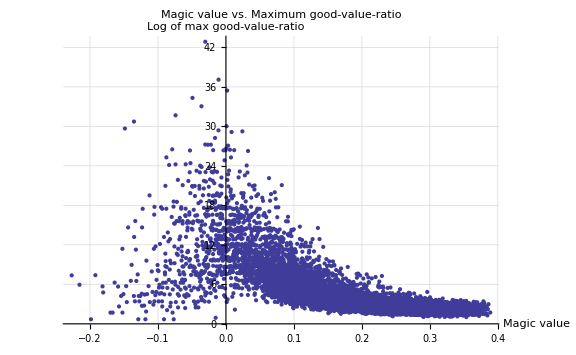

```mathematica
ListPlot[
Sort[

Table[

{magicGraham[a],
With[{solutions = GoodForTuple[a,10^20]},
PrintTemporary[ToString[a] <> " " <> ToString[Length[solutions]]];
Max[Table[N[Log[solutions[[i]]+1]- Log[solutions[[i-1]]+1]], {i,2, Min[5000,Length[solutions]]}]]
]}
, {a, Subsets[Table[Prime[p],{p,2,25}], {4}]}
]
, #1[[1]] > #2[[1]]&
],
GridLines->Automatic,
PlotRange->{All,All},
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
Ticks->{All,All,All},  
PerformanceGoal->"Quality", 
Method->"QuasiNewton",
ImageSize->Large,
PlotLabel->"Magic value vs. Maximum good-value-ratio",
AxesLabel->{"Magic value", "Log of max good-value-ratio"},
Axes->True
]
```

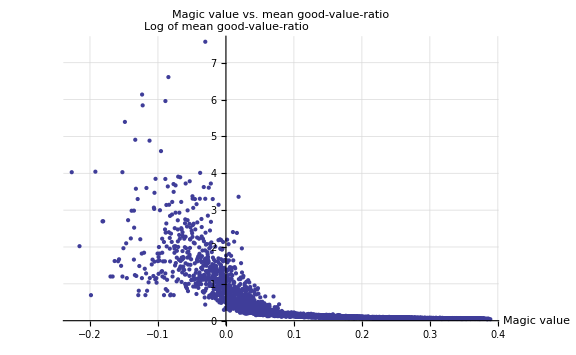

```mathematica
ListPlot[
Sort[

Table[

{magicGraham[a],
With[{solutions = GoodForTuple[a,10^20]},
PrintTemporary[ToString[a] <> " " <> ToString[Length[solutions]]];
Mean[Table[N[Log[solutions[[i]]+1]- Log[solutions[[i-1]]+1]], {i,2, Min[5000,Length[solutions]]}]]
]}
, {a, Subsets[Table[Prime[p],{p,2,25}], {4}]}
]
, #1[[1]] > #2[[1]]&
],
GridLines->Automatic,
PlotRange->{All,All},
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
Ticks->{All,All,All},  
PerformanceGoal->"Quality", 
Method->"QuasiNewton",
ImageSize->Large,
PlotLabel->"Magic value vs. mean good-value-ratio",
AxesLabel->{"Magic value", "Log of mean good-value-ratio"},
Axes->True
]
```

```mathematica
With [
{range=10^20},
Show[
Table [
ListLogPlot[
Table[
{a[[1]], a[[2]]},
{a,Select[Table[{N[magicGraham[tuple]],n,Table[Last[IntegerDigits [n,tuplePrime]],{tuplePrime,tuple}]}, {n,GoodForTuple[tuple,range]}], #[[3]][[1]]==0 || #[[3]][[2]]==0|| #[[3]][[3]]==0|| #[[3]][[4]]==0&]}
], Joined->True,
PlotMarkers->Automatic,
PlotRange->All
],
{tuple,Subsets[Table[Prime[p],{p,2,12}], {4}]}
]
]
]
```

```mathematica
With[{tuple = {7,11,13,17}, range=10^20},
Select[Table[{N[magicGraham[tuple]],n,Table[Last[IntegerDigits [n,tuplePrime]],{tuplePrime,tuple}]}, {n,GoodForTuple[tuple,range]}], #[[3]][[1]]==0 || #[[3]][[2]]==0|| #[[3]][[3]]==0|| #[[3]][[4]]==0&]
]
```

{{-0.00618561,0,{0,0,0,0}},{-0.00618561,56,{0,1,4,5}},{-0.00618561,364,{0,1,0,7}},{-0.00618561,408,{2,1,5,0}},{-0.00618561,5491,{3,2,5,0}},{-0.00618561,36179,{3,0,0,3}},{-0.00618561,36183,{0,4,4,7}},{-0.00618561,6033811,{0,3,4,1}},{-0.00618561,6033833,{1,3,0,6}},{-0.00618561,900190515,{0,4,3,4}},{-0.00618561,900190566,{2,0,2,4}},{-0.00618561,2594285750,{0,1,4,2}},{-0.00618561,2594285765,{1,5,6,0}},{-0.00618561,712139413975,{3,0,2,4}},{-0.00618561,712139413979,{0,4,6,8}},{-0.00618561,712139413988,{2,2,2,0}},{-0.00618561,712139414470,{1,0,3,6}},{-0.00618561,712139414483,{0,2,3,2}},{-0.00618561,10955278810686,{0,1,2,8}},{-0.00618561,10955280445011,{0,1,6,4}},{-0.00618561,10955280445032,{0,0,1,8}},{-0.00618561,1933946779751779,{2,1,0,7}},{-0.00618561,1933946779771413,{1,0,4,6}},{-0.00618561,1933946779771426,{0,2,4,2}},{-0.00618561,1933946779771765,{3,0,5,1}},{-0.00618561,1967849470514788,{0,3,3,4}},{-0.00618561,1967849470514840,{3,0,3,5}}}

```mathematica
Primaries[tuple_, range_] := Select[Table[{N[magicGraham[tuple]],n,Table[Last[IntegerDigits [n,tuplePrime]],{tuplePrime,tuple}]}, {n,GoodForTuple[tuple,range]}], #[[3]][[1]]==0 || #[[3]][[2]]==0|| #[[3]][[3]]==0|| #[[3]][[4]]==0&]
```

```mathematica
Primaries[{7,11,13,17},10^20]
```

{{-0.00618561,0,{0,0,0,0}},{-0.00618561,56,{0,1,4,5}},{-0.00618561,364,{0,1,0,7}},{-0.00618561,408,{2,1,5,0}},{-0.00618561,5491,{3,2,5,0}},{-0.00618561,36179,{3,0,0,3}},{-0.00618561,36183,{0,4,4,7}},{-0.00618561,6033811,{0,3,4,1}},{-0.00618561,6033833,{1,3,0,6}},{-0.00618561,900190515,{0,4,3,4}},{-0.00618561,900190566,{2,0,2,4}},{-0.00618561,2594285750,{0,1,4,2}},{-0.00618561,2594285765,{1,5,6,0}},{-0.00618561,712139413975,{3,0,2,4}},{-0.00618561,712139413979,{0,4,6,8}},{-0.00618561,712139413988,{2,2,2,0}},{-0.00618561,712139414470,{1,0,3,6}},{-0.00618561,712139414483,{0,2,3,2}},{-0.00618561,10955278810686,{0,1,2,8}},{-0.00618561,10955280445011,{0,1,6,4}},{-0.00618561,10955280445032,{0,0,1,8}},{-0.00618561,1933946779751779,{2,1,0,7}},{-0.00618561,1933946779771413,{1,0,4,6}},{-0.00618561,1933946779771426,{0,2,4,2}},{-0.00618561,1933946779771765,{3,0,5,1}},{-0.00618561,1967849470514788,{0,3,3,4}},{-0.00618561,1967849470514840,{3,0,3,5}}}

```mathematica
Primaries2[tuple_, range_] := Table[{N[magicGraham[tuple]],n,Table[Last[IntegerDigits [n,tuplePrime]],{tuplePrime,tuple}]}, {n,GoodForTuple[tuple,range]}]
```

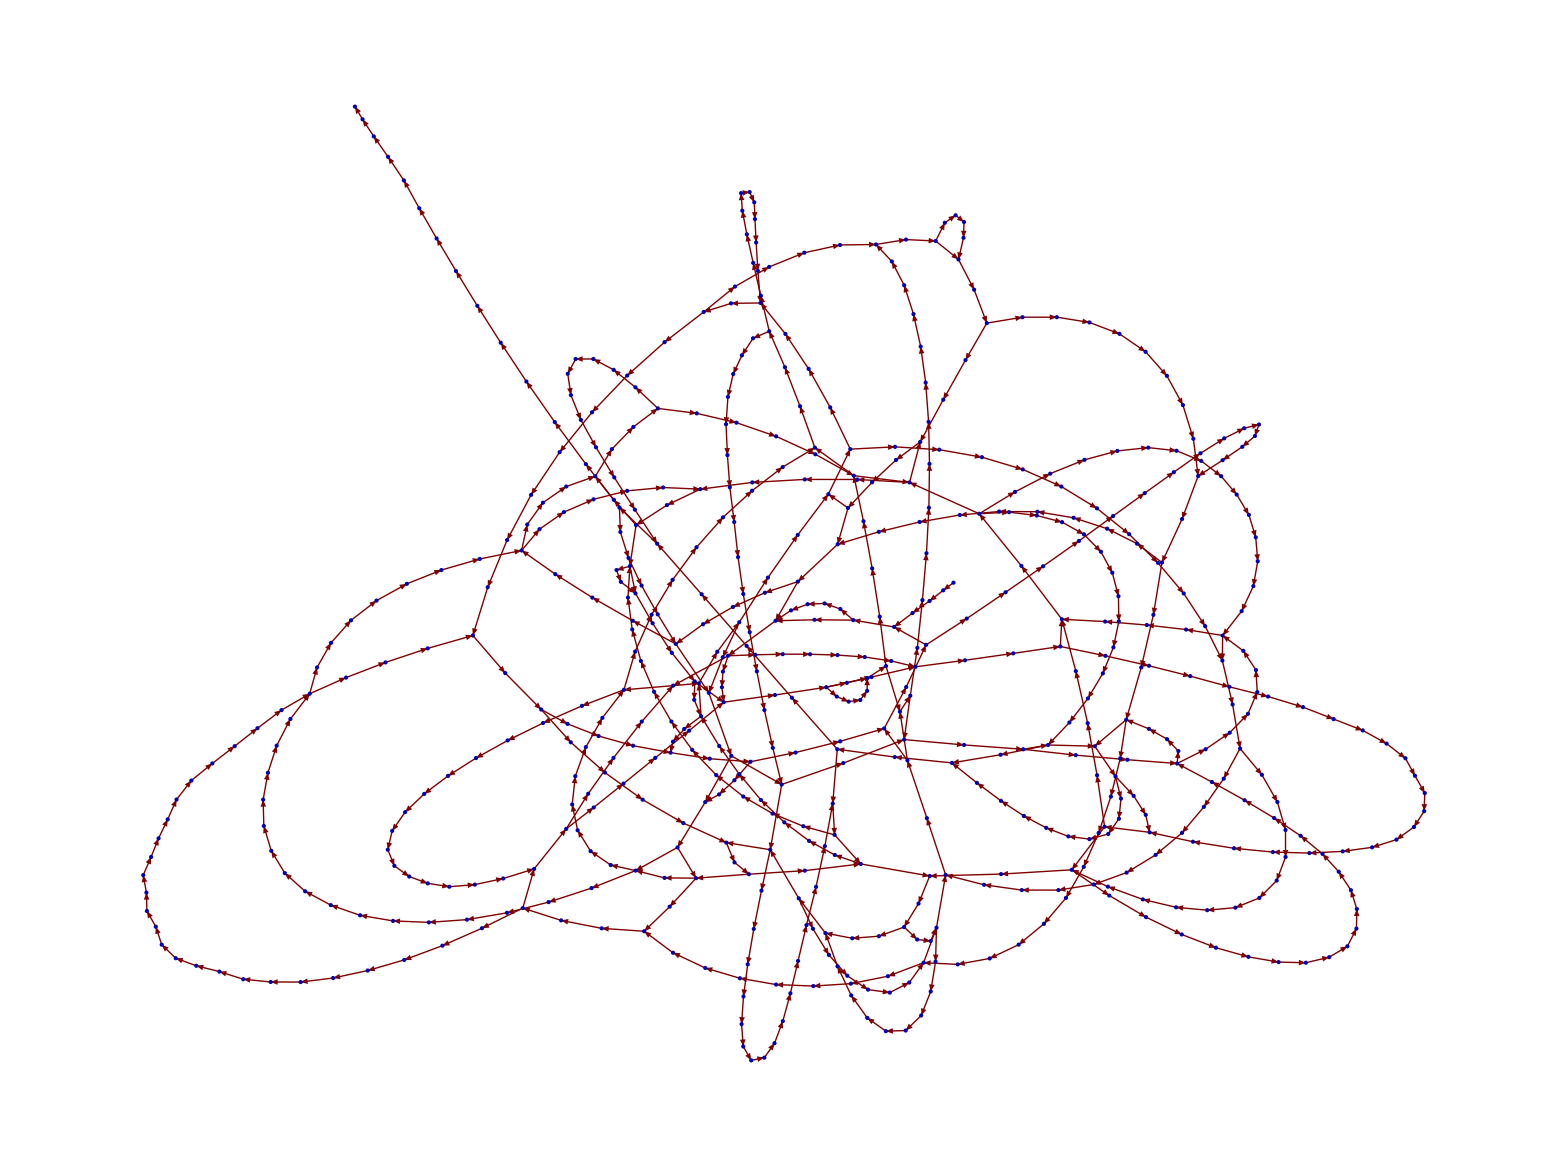

```mathematica
With[{tuple= {7,11,13,19}, range=10^200},
GraphPlot[
With[{ok=Primaries2[tuple,range]},
With[{highestPrime= 7*11*13*19},
Table[{FromDigits[ok[[i-1]][[3]],highestPrime]->FromDigits[ok[[i]][[3]], highestPrime],i}, {i,2, Length[ok]}]
]
],
DirectedEdges->False,
VertexLabeling->False,
SelfLoopStyle->None,
MultiedgeStyle->None,
EdgeLabeling->True]
]
```

```mathematica
With[{tuple= {7,11,13,19}, range=10^20},

With[{ok=Primaries[tuple,range]},
With[{highestPrime= Last[tuple]},
Print[ok];Table[{FromDigits[ok[[i-1]][[3]],highestPrime]->FromDigits[ok[[i]][[3]], highestPrime]}, {i,2, Length[ok]}]
]
]
]
```

{{0.000302007,0,{0,0,0,0}},{0.000302007,57,{1,2,5,0}},{0.000302007,364,{0,1,0,3}},{0.000302007,407,{1,0,4,8}},{0.000302007,2915,{3,0,3,8}},{0.000302007,36179,{3,0,0,3}},{0.000302007,36183,{0,4,4,7}},{0.000302007,13336039029618452,{0,4,4,2}},{0.000302007,13336039029618474,{1,4,0,5}},{0.000302007,13336039266698746,{3,4,0,6}},{0.000302007,13336039266787527,{3,4,4,0}}}

{{0→7676},{7676→364},{364→6943},{6943→20642},{20642→20580},{20580→1527},{1527→1522},{1522→8308},{8308→22027},{22027→22097}}

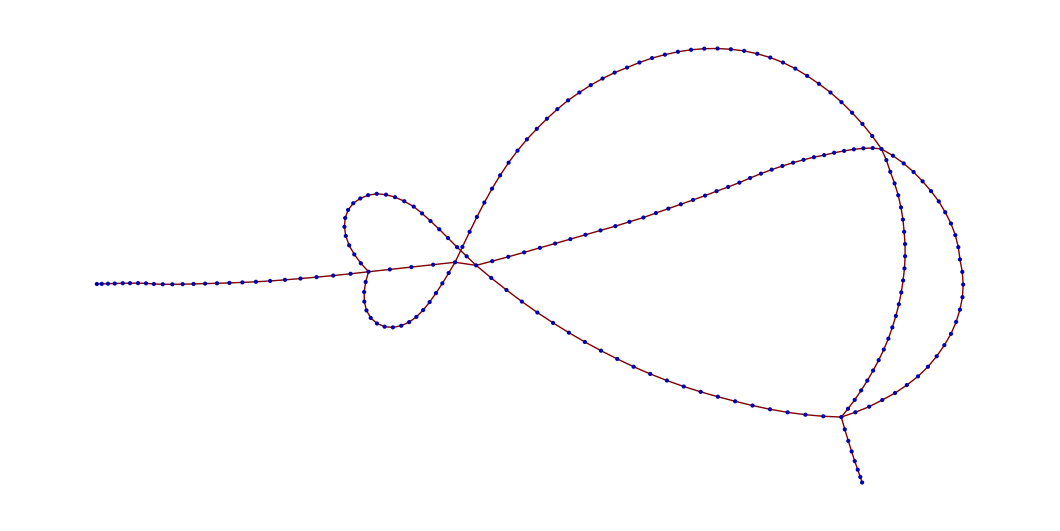

```mathematica
With[{tuple= {7,11,13,23}, range=10^200},
GraphPlot[
With[{ok=Primaries2[tuple,range]},
With[{highestPrime= 13},
Table[{FromDigits[ok[[i-1]][[3]],highestPrime]->FromDigits[ok[[i]][[3]], highestPrime],i}, {i,2, Length[ok]}]
]
],
DirectedEdges->False,
VertexLabeling->False,
SelfLoopStyle->None,
MultiedgeStyle->None,
EdgeLabeling->False]
]
```